# Obligate cross-feeding expands the metabolic niche of bacteria

## Data & functions

```mathematica
niche=Import["/Users/xxx.xlsx"];
```

```mathematica
convLis2[x_]:={Flatten[niche[[2]][[x[[1]];;x[[1]]+7,#]]&/@Range[x[[2]],x[[2]]+3]],
Flatten[niche[[2]][[x[[1]];;x[[1]]+7,#]]&/@Range[x[[2]]+14,x[[2]]+3+14]],
Flatten[niche[[2]][[x[[1]];;x[[1]]+7,#]]&/@Range[x[[2]]+14+14,x[[2]]+3+14+14]]
}
```

```mathematica
pop5Pos=Partition[Flatten[{{#,90},{#,94},{#,98}}&/@Accumulate[Prepend[ConstantArray[11,48],4]]],{2}];
```

```mathematica
pop5=convLis2/@pop5Pos;
```

```mathematica
(*Monocultures with AA 5*)
```

```mathematica
ABR5=pop5[[18]];
```

```mathematica
ABH5=pop5[[19]];
```

```mathematica
ABW5=pop5[[20]];
```

```mathematica
ABL5=pop5[[21]];
```

```mathematica
BSR5=pop5[[22]];
```

```mathematica
BSH5=pop5[[23]];
```

```mathematica
BSL5=pop5[[24]];
```

```mathematica
ECR5=pop5[[25]];
```

```mathematica
ECH5=pop5[[26]];
```

```mathematica
ECW5=pop5[[27]];
```

```mathematica
ECL5=pop5[[28]];
```

```mathematica
SOR5=pop5[[29]];
```

```mathematica
SOH5=pop5[[30]];
```

```mathematica
SOW5=pop5[[31]];
```

```mathematica
SOL5=pop5[[32]];
```

```mathematica
PFW5=pop5[[33]];
```

```mathematica
PFL5=pop5[[34]];
```

```mathematica
comType=niche[[2]][[#[[1]]]][[#[[2]]]]&/@Partition[Flatten[{{#,2},{#,6},{#,10}}&/@Accumulate[Prepend[ConstantArray[11,48],2]]],{2}]
```

{AB R,AB H,AB W ,AB L,BS R,BS H,BS L,EC R,EC H,EC W,EC L,SO R,SO H,SO W,SO L,PF W,PF L,AB R,AB H,AB W ,AB L,BS R,BS H,BS L,EC R,EC H,EC W,EC L,SO R,SO H,SO W,SO L,PF W,PF L,AB,BS,EC,SO ,PF,AB R - AB H ,AB R - BS H ,AB R - EC H,AB R - SO H,BS R - AB H,BS R - BS H,BS R - EC H,BS R - SO H,EC R - AB H,EC R - BS H,EC R - EC H ,EC R - SO H ,SO R - AB H,SO R - BS H,SO R - EC H,SO R - SO H,AB H - AB W ,AB H - EC W,AB H - SO W,AB H - PF W,BS H - AB W,BS H - EC W ,BS H - SO W,BS H - PF W,EC H - AB W,EC H - EC W ,EC H - SO W ,EC H - PF W,SO H - AB W,SO H - EC W,SO H - SO W ,SO H - PF W,AB W - AB R,AB W - BS R,AB W - EC R,AB W - SO R,EC W - AB R,EC W - BS R,EC W - EC R,EC W - SO R,SO W - AB R,SO W - BS R,SO W - EC R,SO W - SO R,PF W - AB R,PF W - BS R,PF W - EC R,PF W - SO R,AB W - AB L,AB W - BS L,AB W - EC L,AB W - SO L,AB W - PF L ,EC W - AB L,EC W - BS L,EC W - EC L,EC W - SO L,EC W - PF L,SO W - AB L,SO W - BS L,SO W - EC L,SO W - SO L,SO W - PF L ,PF W - AB L,PF W - BS L,PF W - EC L,PF W - SO L,PF W - PF L,AB L - AB R,AB L - BS R,AB L - EC R,AB L - SO R,BS L - AB R,BS L - BS R,BS L - EC R,BS L - SO R,EC L - AB R,EC L - BS R,EC L - EC R,EC L - SO R,SO L - AB R,SO L - BS R,SO L - EC R,SO L - SO R,PF L - AB R,PF L - BS R,PF L - EC R,PF L - SO R,AB H - AB L ,AB H - BS L ,AB H - EC L,AB H - SO L,AB H - PF L,BS H - AB L,BS H - BS - L,BS H - EC L ,BS H - SO L,BS H - PF L,EC H - AB L,EC H - BS L,EC H - EC L ,EC H - SO L ,EC H - PF L,SO H - AB L,SO H - BS L,SO H - EC L,SO H - SO L ,SO H - PF L}

```mathematica
th[x_]:=If[x≥ 0.08,1,0]
```

```mathematica
bit[x_]:=If[x≥ 1,1,0]
```

```mathematica
poSting5=StringReplace[#,{"-"->""," "-> ""}]&/@comType[[40;;147]]
```

{ABRABH,ABRBSH,ABRECH,ABRSOH,BSRABH,BSRBSH,BSRECH,BSRSOH,ECRABH,ECRBSH,ECRECH,ECRSOH,SORABH,SORBSH,SORECH,SORSOH,ABHABW,ABHECW,ABHSOW,ABHPFW,BSHABW,BSHECW,BSHSOW,BSHPFW,ECHABW,ECHECW,ECHSOW,ECHPFW,SOHABW,SOHECW,SOHSOW,SOHPFW,ABWABR,ABWBSR,ABWECR,ABWSOR,ECWABR,ECWBSR,ECWECR,ECWSOR,SOWABR,SOWBSR,SOWECR,SOWSOR,PFWABR,PFWBSR,PFWECR,PFWSOR,ABWABL,ABWBSL,ABWECL,ABWSOL,ABWPFL,ECWABL,ECWBSL,ECWECL,ECWSOL,ECWPFL,SOWABL,SOWBSL,SOWECL,SOWSOL,SOWPFL,PFWABL,PFWBSL,PFWECL,PFWSOL,PFWPFL,ABLABR,ABLBSR,ABLECR,ABLSOR,BSLABR,BSLBSR,BSLECR,BSLSOR,ECLABR,ECLBSR,ECLECR,ECLSOR,SOLABR,SOLBSR,SOLECR,SOLSOR,PFLABR,PFLBSR,PFLECR,PFLSOR,ABHABL,ABHBSL,ABHECL,ABHSOL,ABHPFL,BSHABL,BSHBSL,BSHECL,BSHSOL,BSHPFL,ECHABL,ECHBSL,ECHECL,ECHSOL,ECHPFL,SOHABL,SOHBSL,SOHECL,SOHSOL,SOHPFL}

```mathematica
poStingHour5=#<>"5"&/@poSting5
```

{ABRABH5,ABRBSH5,ABRECH5,ABRSOH5,BSRABH5,BSRBSH5,BSRECH5,BSRSOH5,ECRABH5,ECRBSH5,ECRECH5,ECRSOH5,SORABH5,SORBSH5,SORECH5,SORSOH5,ABHABW5,ABHECW5,ABHSOW5,ABHPFW5,BSHABW5,BSHECW5,BSHSOW5,BSHPFW5,ECHABW5,ECHECW5,ECHSOW5,ECHPFW5,SOHABW5,SOHECW5,SOHSOW5,SOHPFW5,ABWABR5,ABWBSR5,ABWECR5,ABWSOR5,ECWABR5,ECWBSR5,ECWECR5,ECWSOR5,SOWABR5,SOWBSR5,SOWECR5,SOWSOR5,PFWABR5,PFWBSR5,PFWECR5,PFWSOR5,ABWABL5,ABWBSL5,ABWECL5,ABWSOL5,ABWPFL5,ECWABL5,ECWBSL5,ECWECL5,ECWSOL5,ECWPFL5,SOWABL5,SOWBSL5,SOWECL5,SOWSOL5,SOWPFL5,PFWABL5,PFWBSL5,PFWECL5,PFWSOL5,PFWPFL5,ABLABR5,ABLBSR5,ABLECR5,ABLSOR5,BSLABR5,BSLBSR5,BSLECR5,BSLSOR5,ECLABR5,ECLBSR5,ECLECR5,ECLSOR5,SOLABR5,SOLBSR5,SOLECR5,SOLSOR5,PFLABR5,PFLBSR5,PFLECR5,PFLSOR5,ABHABL5,ABHBSL5,ABHECL5,ABHSOL5,ABHPFL5,BSHABL5,BSHBSL5,BSHECL5,BSHSOL5,BSHPFL5,ECHABL5,ECHBSL5,ECHECL5,ECHSOL5,ECHPFL5,SOHABL5,SOHBSL5,SOHECL5,SOHSOL5,SOHPFL5}

```mathematica
co5=ToExpression/@poStingHour5
```

{ABRABH5,ABRBSH5,ABRECH5,ABRSOH5,BSRABH5,BSRBSH5,BSRECH5,BSRSOH5,ECRABH5,ECRBSH5,ECRECH5,ECRSOH5,SORABH5,SORBSH5,SORECH5,SORSOH5,ABHABW5,ABHECW5,ABHSOW5,ABHPFW5,BSHABW5,BSHECW5,BSHSOW5,BSHPFW5,ECHABW5,ECHECW5,ECHSOW5,ECHPFW5,SOHABW5,SOHECW5,SOHSOW5,SOHPFW5,ABWABR5,ABWBSR5,ABWECR5,ABWSOR5,ECWABR5,ECWBSR5,ECWECR5,ECWSOR5,SOWABR5,SOWBSR5,SOWECR5,SOWSOR5,PFWABR5,PFWBSR5,PFWECR5,PFWSOR5,ABWABL5,ABWBSL5,ABWECL5,ABWSOL5,ABWPFL5,ECWABL5,ECWBSL5,ECWECL5,ECWSOL5,ECWPFL5,SOWABL5,SOWBSL5,SOWECL5,SOWSOL5,SOWPFL5,PFWABL5,PFWBSL5,PFWECL5,PFWSOL5,PFWPFL5,ABLABR5,ABLBSR5,ABLECR5,ABLSOR5,BSLABR5,BSLBSR5,BSLECR5,BSLSOR5,ECLABR5,ECLBSR5,ECLECR5,ECLSOR5,SOLABR5,SOLBSR5,SOLECR5,SOLSOR5,PFLABR5,PFLBSR5,PFLECR5,PFLSOR5,ABHABL5,ABHBSL5,ABHECL5,ABHSOL5,ABHPFL5,BSHABL5,BSHBSL5,BSHECL5,BSHSOL5,BSHPFL5,ECHABL5,ECHBSL5,ECHECL5,ECHSOL5,ECHPFL5,SOHABL5,SOHBSL5,SOHECL5,SOHSOL5,SOHPFL5}

```mathematica
co5
```

{{{0.0056,0.6609,0.0049,0.,0.,0.0243,0.,0.0005,0.0944,0.2308,0.,0.13,1.3621,0.0334,0.9223,0.2752,0.7982,1.0814,0.,0.0132,0.,0.,0.,0.8444,0.0553,0.2131,0.0262,0.3508,0.0489,0.1222,0.0538,0.0218},{0.,1.199,0.,0.,0.,0.0227,0.,0.,0.2352,0.1025,0.,0.2445,1.3634,0.0458,1.2273,0.96,0.7909,0.9286,0.,0.,0.,0.,0.,0.4847,0.,0.1501,0.,0.7405,0.,0.4477,0.2477,0.},{0.,0.4919,0.,0.0098,0.0174,0.1083,0.0256,0.0167,0.2629,0.2311,0.,0.5108,1.0792,0.0358,0.8067,0.7046,0.8935,0.8587,0.,1.38778×10^-17,0.0701,0.,0.,1.1164,0.0234,0.2925,0.0098,0.5508,0.0349,0.2484,0.0878,0.0429}},{{0.,0.0083,0.,0.,0.,0.,0.,0.,0.,0.0246,0.,0.0321,0.,0.,0.,0.,0.,0.,0.,0.001,0.,0.,0.,0.,0.2171,0.,0.0052,0.0704,0.,0.0277,0.,0.},{0.,0.,0.0165,0.0062,0.0043,0.0472,0.0253,0.,0.0068,0.0308,0.,0.,0.0168,0.0193,0.0168,0.0096,0.0151,0.0186,0.,0.,0.021,0.,0.,0.0106,0.0725,0.0449,0.004,0.0226,0.0188,0.018,0.01,0.},{0.,0.,0.,0.0154,0.0094,0.0295,0.0281,0.0085,0.,0.03,0.,0.0115,0.0187,0.0189,0.0244,0.0161,0.0053,0.0036,0.0045,0.0053,0.0244,0.0136,0.0197,0.0221,0.1524,0.0155,0.0204,0.0241,0.0296,0.0249,0.0196,0.0271}},{{0.0228,0.66,0.,0.0012,0.045,0.0782,0.0256,0.0199,0.3102,0.5512,0.,0.295,1.2424,0.0789,0.8509,0.1936,0.5879,0.9377,0.,0.0179,0.,0.,0.,0.8396,0.1057,0.6911,0.119,0.7186,0.1393,0.4562,0.,0.0916},{0.,0.67,0.,0.034,0.0504,0.1946,0.0109,0.,0.2615,0.047,0.,0.5198,1.1636,0.0304,0.9168,0.0229,0.8267,0.9202,0.,0.,0.0746,0.,0.,0.852,0.,0.2333,0.0608,0.6019,0.0687,0.7184,0.171,0.0506},{0.,0.4199,0.,0.0176,0.0157,0.0824,0.0201,0.,0.4153,0.4215,0.,0.7751,1.1318,0.054,0.9679,0.3315,1.1463,0.9971,0.,0.,0.0312,0.,0.,0.7833,0.0192,0.2828,0.0032,0.5405,0.1962,0.2784,0.0444,0.0266}},{{0.,0.760733,1.00853,0.817633,0.,0.142433,0.0665667,0.0577333,0.0201333,0.0903333,0.0225667,0.299533,0.416167,0.0785333,0.788933,0.266333,0.142267,0.556067,0.,0.0707667,0.,0.,0.,0.771533,0.321433,0.715633,0.112067,0.427267,0.185833,0.554867,0.,0.121533},{0.,0.6593,1.0817,1.3773,0.0443,0.1633,0.1084,0.,0.11,0.,0.0583,0.2377,0.6213,0.1101,0.4627,0.1988,0.0519,0.2319,0.,0.,0.0029,0.,0.,0.0499,0.1898,0.6659,0.0881,0.6497,0.,1.2936,0.0432,0.0417},{0.,0.742,0.389,0.8935,0.0174,0.1364,0.022,0.0057,0.,0.,0.0064,0.0522,0.612,0.0993,0.0462,0.0822,0.0259,0.0616,0.0005,0.0209,0.0148,0.0011,0.,0.0293,0.2177,0.2102,0.0304,0.1954,0.029,0.9828,0.0208,0.0231}},{{0.,0.204567,0.,0.,0.,0.0973333,0.,0.,0.,0.0449333,0.,0.0541333,0.212567,0.,0.146133,0.143733,0.491767,0.378133,0.,0.,0.,0.,0.,0.0859667,0.,0.0373667,0.,0.159967,0.,0.0788667,0.,0.00596667},{0.,0.5133,0.,0.,0.04,0.4708,0.0864,0.0096,0.0863,0.0032,0.,0.0879,0.4183,0.0977,0.2315,0.3219,0.0867,0.1353,0.,0.0757,0.0967,0.,0.,0.5783,0.,0.1809,0.0005,0.3014,0.09,0.236,0.2021,0.0646},{0.,0.0222,0.,0.,0.,0.1976,0.,0.,0.2016,0.,0.,0.,0.1002,0.072,0.0685,0.1764,0.211,0.1025,0.,0.,0.0164,0.,0.,0.3117,0.,0.1512,0.,0.1599,0.0537,0.0552,0.0176,0.0408}},{{0.,0.,0.,0.,0.,0.124133,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.0046,0.,0.,0.0233,0.,0.,0.0079,0.,0.0064,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.0163,0.0027,0.,0.,0.0143,0.0241,0.0126,0.,0.0081,0.,0.0095,0.0206,0.0179,0.0184,0.,0.,0.,0.,0.0052,0.024,0.0184,0.0252,0.0059,0.,0.,0.,0.,0.,0.005,0.0186,0.}},{{0.,0.3216,0.0141667,0.,0.,0.0980667,0.,0.,0.1295,0.0601667,0.,0.0828667,0.3363,0.0370667,0.400667,0.205567,0.178,0.501367,0.,0.0102667,0.,0.0135667,0.,0.175667,0.,0.183967,0.0810667,0.190467,0.102967,0.160467,0.,0.0667667},{0.,0.1608,0.0447,0.,0.0662,0.3295,0.0597,0.,0.2547,0.,0.,0.4334,0.3079,0.106,0.2602,0.3464,0.1189,0.2505,0.,0.,0.0205,0.,0.,0.1005,0.,0.2353,0.0597,0.4081,0.0332,0.1172,0.1603,0.0477},{0.,0.3204,0.,0.,0.0585,0.2297,0.,0.,0.3393,0.,0.,0.3403,0.4183,0.0715,0.376,0.4054,0.258,0.4161,0.,0.,0.0342,0.,0.,0.4708,0.,0.4303,0.,0.3391,0.0025,0.0719,0.0758,0.0184}},{{0.,1.4729,0.322167,0.281567,0.0254,0.474667,0.1656,0.0290667,0.,0.0555667,0.0478667,0.653167,0.9378,0.128367,0.402567,0.325267,0.,0.,0.,0.195567,0.,0.,0.00246667,0.345867,0.0095,0.0215,0.126,0.478567,0.0582,0.0142667,0.1062,0.0708667},{0.,0.1416,0.1284,0.,0.,0.0827,0.,0.,0.,0.0368,0.,0.,0.0117,0.,0.,0.,0.,0.0119,0.,0.,0.0251,0.,0.,0.,0.,0.,0.,0.0414,0.,0.0866,0.,0.},{0.,0.157,0.1276,0.,0.,0.0186,0.,0.,0.,0.0119,0.,0.,0.0222,0.0116,0.0434,0.,0.,0.0164,0.,0.,0.0097,0.,0.,0.,0.,0.0189,0.,0.0286,0.,0.1297,0.01,0.}},{{0.,0.745267,0.,0.,0.,0.0158667,0.,0.,0.0683,0.0478667,0.,0.225867,1.5308,0.0341667,0.4669,0.226667,0.893667,1.07657,0.,0.,0.,0.,0.,1.02577,0.0175667,0.137967,0.111867,0.306667,0.0507667,0.237467,0.0140667,0.},{0.,0.6439,0.,0.0149,0.0113,0.1315,0.0231,0.0246,0.0829,0.0959,0.,0.3377,1.3151,0.0302,0.7399,0.0679,0.9389,0.7959,0.,0.,0.0447,0.,0.,0.8402,0.0746,0.2114,0.0776,0.4279,0.0274,0.6622,0.1975,0.0114},{0.,0.3023,0.0027,0.0045,0.0122,0.0546,0.0175,0.0105,0.2099,0.1856,0.,0.5042,1.3628,0.0708,0.8183,0.5621,0.9169,0.833,0.,0.0044,0.0293,0.,0.,1.2254,0.0096,0.1122,0.0062,0.4662,0.0634,0.3453,0.0591,0.0235}},{{0.,0.,0.,0.,0.,0.,0.007,0.,0.,0.0192,0.,0.0144,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.013,0.,0.0049,0.206,0.,0.,0.,0.,0.0134,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.0897,0.,0.,0.,0.,0.,0.,0.,0.9619,0.,0.,0.,0.,0.,0.,0.,0.027,0.,0.,0.,0.,0.,0.,0.},{0.,0.4084,0.0083,0.,0.,0.4778,0.0034,0.,0.,0.1235,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.3466,0.1252,0.,0.,0.2245,0.,0.,0.,0.}},{{0.0091,0.4309,0.,0.,0.0036,0.0663,0.,0.0376,0.1107,0.1828,0.,0.3605,1.27103,0.0150333,0.533633,0.1812,0.7136,1.17133,0.,0.0323,0.,0.,0.,0.574,0.0001,0.1836,0.0427333,0.6752,0.0995333,0.4345,0.0277333,0.085},{0.,0.5072,0.0068,0.0708,0.,0.1045,0.,0.0035,0.1114,0.1032,0.,0.6921,1.4155,0.0301,0.504,0.1499,1.0207,1.2114,0.,0.,0.0579,0.,0.,1.1897,0.0481,0.1932,0.0242,0.505,0.1326,0.733,0.0575,0.0149},{0.,0.6275,0.,0.0401,0.0248,0.0509,0.0134,0.,0.3711,0.3216,0.,1.0155,1.1997,0.0259,0.7186,0.3937,1.1328,1.2315,0.,0.,0.0589,0.,0.,0.9709,0.006,0.5491,0.0287,0.6957,0.1409,0.6585,0.0283,0.0348}},{{0.00123333,0.723133,1.56,1.0619,0.,0.0955,0.,0.0298,0.194833,0.0096,0.,0.0338333,0.611433,0.,0.565433,0.149,0.0358333,0.287033,0.,0.,0.,0.,0.,0.0751,0.249033,0.308933,0.00263333,0.850233,0.0229333,1.0945,0.,0.102533},{0.,0.5073,0.6849,0.9567,0.,0.0134,0.0263,0.0051,0.0638,0.0151,0.,0.0874,0.7508,0.0066,0.0564,0.0429,0.1954,0.0526,0.,0.,0.0183,0.,0.,0.0343,0.084,0.0374,0.0101,0.1964,0.0144,0.7158,0.0102,0.},{0.,0.5171,0.4265,0.8038,0.0132,0.0101,0.0164,0.,0.811,0.,0.,0.0258,0.1841,0.0073,0.098,0.0411,0.0138,0.0324,0.,0.0162,0.0128,0.,0.,0.1346,0.1728,0.2357,0.0048,0.0366,0.0171,0.1443,0.015,0.0087}},{{0.,1.3241,0.171,0.0293,0.1799,0.3196,0.1397,0.1947,0.3052,0.0606,0.1184,0.5577,0.6653,0.212,0.7485,0.3963,0.4032,0.9548,0.0028,0.1354,0.,0.1013,0.0398,0.2548,0.0436,0.2615,0.141,0.3769,0.308,1.076,0.1562,0.1679},{0.,0.4459,0.,0.,0.,0.1079,0.0398,0.0116,0.2102,0.,0.,0.221,0.267,0.,0.1609,0.318,0.3396,0.0121,0.,0.,0.,0.,0.,0.0457,0.,0.1245,0.,0.378,0.,0.1353,0.1281,0.0133},{0.,0.1949,0.,0.,0.0068,0.0651,0.,0.,0.1432,0.,0.,0.2291,0.1459,0.0033,0.1726,0.1669,0.1963,0.0647,0.,0.,0.0354,0.,0.,0.1194,0.,0.1278,0.,0.1842,0.0683,0.0892,0.042,0.0057}},{{0.,0.0171,0.0377,0.,0.,0.0655,0.0203,0.,0.,0.071,0.,0.1116,0.001,0.0262,0.,0.,0.,0.0169,0.,0.0593,0.0023,0.0361,0.0176,0.,0.0645,0.0121,0.,0.0155,0.,0.033,0.,0.},{0.,0.,0.2736,0.,0.,0.,0.,0.,0.,0.0377,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0043,0.,0.,0.0036,0.,0.,0.,0.},{0.,0.0158,0.1053,0.0074,0.,0.0139,0.,0.,0.,0.0364,0.,0.,0.0054,0.0048,0.0014,0.,0.,0.,0.,0.0004,0.,0.,0.,0.,0.0116,0.0038,0.,0.,0.,0.011,0.,0.}},{{0.,0.9877,0.1942,0.0581,0.1724,0.3827,0.1459,0.2039,0.3204,0.0447,0.1256,0.4299,0.7925,0.2815,0.3731,0.2291,0.2413,0.3534,0.0035,0.103,0.,0.1111,0.1382,0.2465,0.2368,0.2851,0.0879,0.4343,0.2396,1.2587,0.1529,0.1737},{0.,0.2255,0.0285,0.,0.,0.1727,0.,0.,0.0416,0.,0.,0.3688,0.3166,0.,0.1495,0.0925,0.1319,0.112,0.,0.,0.,0.,0.,0.032,0.,0.0644,0.,0.0453,0.,0.039,0.0282,0.},{0.,0.397,0.0957,0.,0.0776,0.1809,0.0372,0.,0.1529,0.,0.,0.4292,0.4815,0.09,0.2488,0.1714,0.1154,0.1525,0.,0.,0.0078,0.,0.,0.0347,0.,0.0469,0.,0.1946,0.068,0.0845,0.,0.}},{{0.,0.0623,0.,0.,0.,0.0413667,0.,0.0210667,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0510667,0.2768,0.0971667,0.,0.0731,0.,0.102767,0.,0.0170667},{0.,0.0123,0.5014,0.0172,0.,0.0146,0.0116,0.,0.0061,0.0026,0.,0.,0.0006,0.,0.0026,0.0026,0.0033,0.,0.,0.,0.,0.0313,0.,0.,0.0071,0.0007,0.,0.,0.,0.0305,0.,0.},{0.,0.,0.0438,0.0125,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.1209,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.047,0.,0.,0.0722,0.,0.1905,0.,0.}},{{0.0270667,0.836767,0.,0.,0.,0.0883667,0.,0.,0.0524667,0.0987667,0.,0.892367,0.8542,0.0253667,0.683567,0.133667,1.39127,0.942467,0.,0.0548667,0.,0.,0.,0.376267,0.,0.245667,0.0214667,0.215467,0.2078,0.148967,0.,0.0759667},{0.,0.5897,0.,0.,0.002,0.0129,0.,0.,0.3196,0.08,0.,0.4157,0.9232,0.,0.6052,0.4139,1.1844,0.7064,0.,0.,0.0028,0.,0.,0.4018,0.,0.2602,0.0473,0.2081,0.0472,0.3413,0.1227,0.0217},{0.,0.3221,0.,0.,0.,0.,0.,0.,0.1859,0.0808,0.,0.436,0.619,0.,0.376,0.364,0.9238,0.4939,0.,0.,0.,0.,0.,0.4418,0.0254,0.,0.,0.,0.0013,0.1881,0.,0.}},{{0.,0.922867,0.,0.,0.,0.,0.,0.,0.0635667,0.0983667,0.,0.323467,0.713467,0.0987667,0.949367,0.289067,0.9933,0.583467,0.,0.,0.,0.,0.,0.428367,0.,0.280467,0.0361667,0.944,0.160667,0.246567,0.,0.0183667},{0.,1.0325,0.,0.,0.,0.,0.,0.,0.2033,0.1009,0.,0.3988,0.763,0.,0.917,0.1952,0.9839,0.5462,0.,0.,0.,0.,0.,0.4455,0.,0.2595,0.0077,0.7106,0.1075,0.3155,0.1239,0.},{0.,0.3472,0.,0.,0.,0.,0.,0.0123,0.2101,0.1671,0.,0.5533,0.7702,0.,0.425,0.4841,0.3728,0.5202,0.,0.,0.0229,0.,0.,0.4433,0.036,0.3464,0.034,0.9031,0.1787,0.286,0.0671,0.0378}},{{0.168267,0.521267,0.312467,0.1178,0.167467,0.374367,0.113867,0.1871,0.0616667,0.,0.,0.386567,0.959867,0.134867,0.206967,0.259367,0.0897667,0.804967,0.,0.,0.,0.0194667,0.,0.1656,0.,0.163967,0.,0.0512667,0.,0.255667,0.,0.0100667},{0.,0.3443,0.,0.,0.,0.0634,0.0283,0.,0.1041,0.,0.,0.1896,0.206,0.0365,0.3613,0.3267,0.0834,0.0616,0.,0.0031,0.0251,0.,0.,0.0247,0.,0.0734,0.,0.275,0.,0.1712,0.0671,0.},{0.,0.2518,0.0137,0.,0.0759,0.0218,0.0426,0.,0.1297,0.,0.,0.1047,0.0582,0.0445,0.0895,0.3363,0.2803,0.083,0.,0.,0.,0.,0.,0.2297,0.,0.1687,0.,0.2124,0.0057,0.1013,0.1089,0.02}},{{0.,0.8156,0.1759,0.,0.0797,0.155867,0.0317667,1.464,0.152667,0.5162,0.,0.856167,1.17517,0.0908667,0.127367,0.278,1.09907,0.875767,0.,0.165567,0.,0.000666667,0.00246667,0.306067,0.,0.805267,0.,1.72567,0.208367,0.645,0.,0.1276},{0.,0.6937,0.,0.,0.0155,0.0966,0.0169,0.6678,0.0569,0.5712,0.,1.702,1.0396,0.0362,0.7265,0.3276,0.8159,1.1473,0.,0.,0.1701,0.0597,0.,0.2708,0.,0.9646,0.0135,1.0961,0.4568,0.6318,0.027,0.0437},{0.,0.8804,0.,0.1725,0.,0.,0.,0.6268,0.4253,0.3806,0.,1.1729,0.9487,0.,0.5672,0.5851,1.0877,1.1457,0.,0.,0.2695,0.,0.,0.8406,0.4903,1.1791,0.0541,1.2661,0.3606,0.9884,0.4327,0.}},{{0.,0.0127,0.,0.,0.,1.06,0.,0.,0.,0.0396,0.,0.,1.12787,0.,0.682167,0.171667,0.,0.,0.,0.,0.,0.,0.,0.535167,0.,0.,0.,0.,0.,0.155467,0.,0.},{0.,0.017,0.,0.0342,0.,0.0116,0.,0.,0.0172,0.0416,0.,0.0074,0.,0.,0.,0.,0.0124,0.016,0.,0.,0.001,0.,0.0007,0.,0.0034,0.0109,0.0505,0.0157,0.0325,0.0125,0.,0.},{0.,0.0165,0.,0.,0.,0.0201,0.0147,0.,0.0677,0.0292,0.,0.0058,0.0133,0.0127,0.0181,0.0067,0.0156,0.0239,0.,0.0034,0.0074,0.,0.,0.0591,0.,0.013,0.023,0.027,0.0373,0.,0.,0.}},{{0.0317333,0.725233,0.0413,0.,0.,0.0202333,0.0229,0.,0.136933,0.107233,0.,0.0120333,0.6631,0.0557333,0.448,0.382533,0.4874,0.837533,0.0076,0.141933,0.00323333,0.0920333,0.0046,0.523533,0.00563333,0.437033,0.0218,0.2041,0.0465,0.1409,0.0528,0.0885333},{0.,0.0098,0.,0.0815,0.,0.2659,0.0134,0.,0.1524,0.0499,0.,0.071,0.0534,0.0071,0.0075,0.,0.,0.0458,0.,0.,0.,0.,0.,0.,0.,0.0113,0.0596,0.0629,0.0122,0.0319,0.,0.},{0.,0.0175,0.,0.,0.0014,0.0159,0.0131,0.0025,0.0876,0.0565,0.,0.0429,0.0284,0.0088,0.0133,0.0032,0.0086,0.0468,0.,0.0187,0.0085,0.,0.,0.0111,0.0027,0.0219,0.072,0.0471,0.0235,0.0433,0.,0.0088}},{{0.,0.115133,0.0422,0.,0.,0.0643333,0.,0.,0.,0.123933,0.0181,0.0071,0.,0.,0.,0.,0.0096,0.0490333,0.,0.0458,0.195833,0.036,0.,0.0207333,0.,0.0795,0.,0.,0.,0.2596,0.,0.0803333},{0.,0.0462,0.1282,0.0278,0.0021,0.0356,0.0196,0.0056,0.,0.0231,0.,0.0342,0.0134,0.0078,0.0082,0.,0.0102,0.0073,0.,0.,0.0144,0.0056,0.,0.,0.,0.0134,0.0192,0.0243,0.0036,0.,0.,0.},{0.,0.0975,0.1847,0.0221,0.,0.0354,0.001,0.,0.,0.0081,0.0024,0.,0.0033,0.,0.0028,0.,0.,0.0005,0.,0.,0.,0.0038,0.,0.,0.0048,0.0034,0.0039,0.0179,0.0598,0.1029,0.,0.}},{{0.,0.0451,0.,0.,0.,0.,0.0407333,0.00403333,0.0194,0.238933,0.,0.,0.0320333,0.0802333,0.0063,0.0229333,0.,0.0568333,0.0265,0.0444,0.00603333,0.0619333,0.,0.,0.,0.1857,0.,0.0888333,0.,0.021,0.,0.00393333},{0.,0.0108,0.0167,0.0014,0.0166,0.0232,0.0102,0.,0.0105,0.0585,0.,0.0016,0.0186,0.,0.0157,0.,0.,0.016,0.,0.0017,0.012,0.009,0.0029,0.,0.,0.0436,0.0053,0.0161,0.0056,0.,0.0053,0.},{0.,0.0272,0.,0.,0.,0.0186,0.0185,0.0036,0.014,0.0662,0.0098,0.0037,0.0083,0.0064,0.0142,0.0087,0.0084,0.0313,0.,0.0099,0.0022,0.0027,0.,0.,0.0135,0.0745,0.,0.0016,0.,0.0037,0.0022,0.}},{{0.,0.596167,0.,0.,0.,0.,0.,0.,0.00416667,0.3271,0.,0.707967,0.510067,0.,0.571867,0.2124,0.847767,0.735867,0.,0.,0.,0.,0.,0.176,0.,0.2016,0.0203667,0.254067,0.0775667,0.172267,0.0169667,0.},{0.,0.5885,0.,0.0094,0.,0.,0.,0.,0.1704,0.1999,0.,0.8429,0.7611,0.0128,0.5697,0.3779,0.7655,0.6341,0.,0.,0.0411,0.,0.,0.3154,0.,0.2293,0.,0.3043,0.0058,0.3272,0.1107,0.0104},{0.,0.6179,0.0401,0.0627,0.0047,0.0094,0.0085,0.0014,0.1655,0.2715,0.,0.939,1.226,0.0214,0.6277,0.2961,0.8763,0.8872,0.,0.0201,1.4349,0.,0.,0.4824,0.0027,0.3683,0.0272,0.5125,0.0434,0.286,0.0577,0.0261}},{{0.0755,0.436767,0.,0.,0.,0.0730667,0.0542667,0.,0.0478667,0.3166,0.,0.657767,1.01167,0.,0.571067,0.218867,0.731067,0.886967,0.,0.,0.,0.,0.,0.1475,0.,0.0875667,0.,0.419067,0.0600667,0.0962667,0.,0.},{0.,0.5688,0.0338,0.0484,0.,0.0057,0.,0.,0.2828,0.22,0.,1.0228,1.157,0.0294,0.7279,0.2792,0.9528,1.0291,0.,0.,0.0449,0.,0.,0.576,0.,0.3885,0.,0.3881,0.0875,0.2449,0.0418,0.0259},{0.,0.6527,0.0012,0.95,0.0153,0.0074,0.,0.,0.2384,0.2814,0.,1.5888,1.1178,0.025,0.9698,0.317,0.5975,0.9775,0.,0.,0.0426,0.,0.,0.456,0.,0.3592,0.001,0.5804,0.1738,0.2723,0.0079,0.0031}},{{0.,0.137867,0.,0.,0.0125667,0.1531,0.,0.0153,0.101867,0.0181,0.,0.190667,0.397967,0.0252667,0.142367,0.117067,0.0778667,0.0747667,0.,0.,0.,0.,0.,0.00506667,0.,0.0606667,0.,0.125967,0.0488667,0.0879,0.,0.},{0.,0.1401,0.0297,0.0187,0.,0.0107,0.,0.,0.0012,0.,0.,0.3042,0.3318,0.,0.1986,0.1641,0.1145,0.2294,0.,0.,0.0031,0.,0.,0.0614,0.,0.0758,0.006,0.0786,0.0099,0.0456,0.019,0.},{0.,0.1125,0.,0.0576,0.,0.1081,0.,0.,0.1155,0.,0.,1.0448,0.207,0.,0.2352,0.0403,0.0948,0.2961,0.,0.,0.8976,0.,0.,0.0514,0.,0.1056,0.,0.1808,0.0408,0.0754,0.0153,0.}},{{0.,0.610833,0.,0.,0.,0.0892,0.,0.6605,0.189333,0.405,0.,0.9051,0.949533,0.1002,0.634633,0.3873,0.774833,0.904833,0.,0.0860333,0.,0.1077,0.,0.4113,0.,0.866133,0.0307333,1.24453,0.472833,0.3553,0.0211333,0.},{0.,0.5269,0.0157,0.,0.,0.0079,0.0073,0.6648,0.0203,0.2891,0.,1.4083,1.0139,0.0108,0.7602,0.2491,0.7961,0.8903,0.,0.,0.2076,0.0649,0.,0.1087,0.,0.7947,0.,0.9478,0.2779,0.5899,0.062,0.},{0.,0.4291,0.114,0.073,0.0229,0.0672,0.,0.0608,0.2538,0.1546,0.,1.2296,0.917,0.0215,0.569,0.2058,0.6535,0.9214,0.,0.0177,0.2718,0.1162,0.,0.1616,0.,0.8345,0.,1.0641,0.5939,0.5965,0.,0.}},{{0.0038,0.5015,0.,0.0004,0.,0.107433,0.,0.,0.135133,0.0642,0.,0.130633,0.733033,0.,0.,0.,0.160133,0.105133,0.,0.,0.,0.,0.,0.,0.,0.0357333,0.,0.615133,0.,0.462333,0.,0.},{0.,0.3913,0.111,0.0515,0.0087,0.1029,0.0099,0.0109,0.0548,0.0675,0.0145,0.1221,0.5978,0.0194,0.0353,0.0151,0.0495,0.255,0.,0.0019,0.0276,0.0056,0.,0.0933,0.0019,0.0615,0.0527,0.3155,0.0596,0.2459,0.008,0.0112},{0.,0.3836,0.1654,0.0648,0.0103,0.0183,0.0162,0.,0.0129,0.0332,0.0138,0.0184,0.2837,0.0125,0.0087,0.,0.0057,0.0113,0.,0.0228,0.0159,0.,0.,0.0691,0.0009,0.0334,0.0261,0.6048,0.0511,0.295,0.0039,0.}},{{0.,0.877033,0.,0.,0.,0.0276,0.,0.,0.0838333,0.0416,0.,0.2083,0.342033,0.,0.0713,0.,0.0201,0.112233,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.6029,0.,0.0129,0.,0.},{0.,0.3655,0.2114,0.0543,0.0152,0.1253,0.035,0.0386,0.1051,0.096,0.0198,0.3372,0.5566,0.0194,0.1453,0.0283,0.0504,0.1288,0.,0.0214,0.0362,0.,0.004,0.0832,0.,0.0929,0.0453,0.4224,0.0583,0.1857,0.0076,0.},{0.,0.2624,0.2147,0.0517,0.0187,0.0738,0.0064,0.,0.11,0.0606,0.022,0.0967,0.411,0.019,0.1208,0.,0.0141,0.1311,0.0097,0.0304,0.006,0.0034,0.0009,0.5665,0.,0.0391,0.0188,0.3818,0.0328,0.1292,0.,0.}},{{0.,0.126233,0.0553333,0.0293667,0.,0.0139667,0.,0.,0.,0.,0.,0.,0.0680333,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.120333,0.,0.},{0.,0.0506,0.3458,0.0244,0.,0.0069,0.,0.,0.,0.0256,0.,0.0043,0.0233,0.,0.,0.,0.,0.0101,0.,0.,0.0019,0.0006,0.,0.,0.,0.01,0.,0.0163,0.0145,0.1153,0.,0.},{0.,0.0287,0.366,0.053,0.0206,0.054,0.1176,0.025,0.0065,0.0235,0.0282,0.0253,0.0292,0.0221,0.1316,0.0127,0.0187,0.0383,0.019,0.0398,0.0317,0.1501,0.0263,0.0262,0.1468,0.0261,0.0361,0.0641,0.014,0.0923,0.0293,0.0227}},{{0.0642667,0.815367,0.526367,0.392367,0.0716667,0.137867,0.0821667,0.326567,0.00336667,0.412467,0.00816667,0.308867,0.103633,0.0586333,0.,0.,0.530833,0.367033,0.,0.0229333,0.,0.173133,0.,0.00973333,0.0445333,0.853533,0.,1.36413,0.00453333,0.383167,0.,0.},{0.,0.4377,0.4084,0.264,0.0231,0.1138,0.0338,0.,0.001,0.0815,0.0529,0.2947,0.1463,0.0553,0.0681,0.0623,0.4543,0.3576,0.,0.,0.3165,0.2196,0.,0.0881,0.161,1.166,0.,2.0749,0.0881,0.6135,0.0569,0.0821},{0.,0.3671,0.372,0.2278,0.034,0.1174,0.0927,0.0153,0.008,0.1222,0.1368,0.2393,0.0592,0.0552,0.0865,0.0307,0.4818,0.4114,0.,0.0134,0.3805,0.2426,0.,0.0928,0.2647,0.7502,0.0027,1.927,0.0963,0.6791,0.0221,0.0422}},{{0.0139333,0.414133,0.,0.0219667,0.0108333,0.,0.,0.,0.0663333,0.225367,0.,0.,0.693833,0.0846333,0.413533,0.,0.,0.625667,0.,0.,0.,0.,0.,0.861433,0.0692667,0.248833,0.,0.631933,0.,0.495433,0.0627667,0.},{0.,0.3704,0.0112,0.003,0.0091,0.087,0.0162,0.,0.2187,0.1385,0.,0.1854,0.7956,0.,0.4096,0.016,0.1241,0.257,0.,0.,0.0436,0.,0.,0.9679,0.0544,0.3333,0.0546,0.4386,0.1898,0.8612,0.,0.},{0.,0.0302,0.0016,1.6976,0.0306,0.0303,0.0053,0.,0.1581,0.1094,0.0021,0.5022,0.6773,0.0131,0.3286,0.0086,0.1747,0.3026,0.,0.0116,0.0189,0.,0.,0.5414,0.0219,0.2704,0.0294,1.2999,0.0691,0.6649,0.0218,0.0062}},{{0.,0.0405,0.,0.,0.0162,0.0528667,0.00226667,0.,0.,0.0297667,0.,0.0591,1.0761,0.0482,0.4622,0.165467,0.,0.0263,0.,0.0057,0.,0.0359667,0.,0.3757,0.,0.0541667,0.0711667,0.,0.0728667,0.1353,0.0118,0.},{0.,0.0035,0.,0.,0.,0.,0.0075,0.,0.0432,0.,0.,0.052,0.0817,0.0188,0.0106,0.0087,0.0056,0.0181,0.,0.,0.0383,0.,0.0163,0.,0.0048,0.0289,0.0536,0.1072,0.0286,0.0328,0.053,0.},{0.,0.0036,0.,0.,0.,0.0083,0.0053,0.,0.0975,0.0091,0.,0.0157,0.0211,0.024,0.,0.,0.0102,0.0245,0.,0.0296,0.0251,0.0026,0.,0.0032,0.0008,0.031,0.0427,0.19,0.0426,0.0351,0.0064,0.}},{{0.,0.219667,0.,0.,0.,0.0830667,0.015,0.,0.106267,0.136067,0.00536667,0.118467,0.7304,0.0113,0.0910667,0.,0.0045,0.464267,0.,0.0542,0.00446667,0.,0.,0.1647,0.,0.1364,0.0482,0.2256,0.0754,0.411,0.,0.},{0.,0.4757,0.0102,0.0242,0.0428,0.0583,0.0315,0.,0.1933,0.2096,0.,0.2223,1.0776,0.036,0.5447,0.0543,0.1678,0.3036,0.,0.,0.0555,0.,0.,0.4313,0.0364,0.3117,0.0806,0.5486,0.1215,1.1925,0.1159,0.0005},{0.,0.1696,0.,0.0056,0.0161,0.0086,0.0101,0.,0.107,0.1738,0.,0.2508,1.2079,0.0021,0.4617,0.,0.0515,0.1831,0.,0.0088,0.0322,0.,0.,0.9344,0.,0.2325,0.0504,0.523,0.1225,1.0224,0.,0.}},{{0.,0.0541,0.111067,0.116267,0.0458,0.331667,0.0399667,0.0823667,0.,0.,0.,0.0032,0.0654,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.061,0.,0.,0.,0.},{0.,0.,0.2101,0.0206,0.0151,0.1427,0.,0.,0.0337,0.0308,0.,0.0604,0.1737,0.0022,0.0255,0.0093,0.001,0.0242,0.,0.0257,0.023,0.,0.0067,0.026,0.0536,0.,0.078,0.1931,0.0589,0.0638,0.018,0.},{0.,0.,0.1398,0.0119,0.,0.0514,0.,0.,0.0064,0.0189,0.0022,0.0025,0.0806,0.0075,0.0062,0.,0.0045,0.0408,0.,0.0191,0.,0.,0.,0.,0.,0.0048,0.0366,0.1272,0.0271,0.0649,0.,0.}},{{0.,0.2041,0.,0.,0.,0.,0.,0.,0.1836,0.3544,0.,0.0018,1.4123,0.033,1.1218,0.248,0.3565,0.9374,0.,0.0024,0.,0.,0.,1.2284,0.0155,0.5618,0.0161,0.8451,0.175,0.4215,0.0117,0.},{0.,0.2079,0.,0.,0.,0.0026,0.,0.,0.3709,0.61,0.,0.2552,1.1526,0.0235,1.0935,1.0286,0.2427,0.7297,0.,0.,0.0292,0.,0.,0.7005,0.0096,0.7933,0.0143,0.9276,0.0572,0.6181,0.2226,0.0014},{0.,0.1506,0.,0.,0.0133,0.0091,0.,0.,0.2998,0.6439,0.,0.2774,1.0239,0.0209,0.9823,0.364,0.3131,0.6912,0.,0.0016,0.0272,0.,0.,0.5659,0.0004,0.9744,0.0345,0.8887,0.0486,0.4371,0.0087,0.}},{{0.,0.5351,0.0071,0.,0.0108,0.,0.,0.,0.0722,0.0552,0.,0.0636,0.6505,0.,0.3187,0.,0.,0.6254,0.,0.,0.,0.,0.,0.0674,0.,0.,0.,0.0648,0.0236,0.,0.,0.},{0.,0.1043,0.,0.2034,0.0223,0.4075,0.016,0.0105,0.1494,0.0834,0.,0.6924,0.32,0.0518,0.6343,0.016,0.0203,0.1562,0.,0.,0.0533,0.,0.,0.0763,0.0063,0.0663,0.0563,0.4634,0.0527,0.5268,0.0605,0.0022},{0.,0.0748,0.,0.,0.0268,0.1507,0.0401,0.,0.046,0.0372,0.,0.0203,0.1502,0.025,0.0397,0.,0.,0.0161,0.,0.0158,0.0215,0.,0.,0.0411,0.,0.013,0.0363,0.1364,0.0736,0.1102,0.007,0.}},{{0.,0.3576,0.,0.,0.,0.0144,0.,0.,0.0589,0.3119,0.,0.044,1.2458,0.,1.1066,0.,0.,0.6817,0.,0.,0.,0.,0.,0.6667,0.,0.1073,0.,0.539,0.,0.2858,0.,0.},{0.,0.5164,0.,0.0142,0.027,0.0261,0.0026,0.,0.3758,0.3959,0.,0.6126,1.3214,0.0221,1.1829,0.0078,0.2356,0.8189,0.,0.,0.036,0.,0.,1.015,0.,0.4526,0.0167,0.7696,0.0636,0.3884,0.0505,0.},{0.,0.1511,0.,0.0163,0.0238,0.0327,0.,0.,0.3043,0.5782,0.,0.2566,1.3558,0.0008,1.0431,0.0139,0.1012,0.914,0.,0.,0.0075,0.,0.,0.8534,0.,0.719,0.0148,0.339,0.0414,0.8128,0.,0.}},{{0.,0.1267,0.,0.,0.,0.0519,0.,0.,0.0791,0.,0.,0.2856,0.1102,0.,0.0155,0.,0.0432,0.1704,0.,0.0022,0.,0.,0.,0.0349,0.1474,0.2691,0.,0.7558,0.1305,1.0649,0.,0.},{0.,0.0166,0.2149,0.,0.,0.0984,0.01,0.,0.1117,0.0323,0.,0.2267,0.3103,0.,0.0316,0.0019,0.,0.2694,0.,0.,0.,0.,0.,0.0073,0.0195,0.1314,0.0462,0.4107,0.0227,0.2316,0.,0.0013},{0.,0.1133,0.2021,0.,0.,0.0309,0.,0.,0.0073,0.0392,0.,0.1814,0.1424,0.018,0.,0.,0.,0.0042,0.,0.,0.,0.,0.,0.,0.0023,0.3271,0.014,0.4813,0.,0.2092,0.,0.}},{{0.,0.2335,0.0927,0.0621,0.,0.1947,0.,0.,0.,0.,0.,0.0492,1.0639,0.,0.,0.1392,0.,0.0299,0.,0.,0.,0.,0.,0.,0.,0.0807,0.,0.1807,0.,0.8332,0.,0.},{0.,0.2651,0.0673,0.0618,0.001,0.0989,0.0286,0.,0.1956,0.,0.,0.1759,0.334,0.0026,0.1366,0.2742,0.0178,0.0339,0.,0.,0.0057,0.,0.,0.0893,0.1273,0.4257,0.,0.0873,0.,1.0052,0.0285,0.},{0.,0.4601,0.0302,1.0593,0.0108,0.0878,0.,0.,0.0156,0.0739,0.,0.4823,1.3882,0.0013,0.4767,0.0878,0.6615,1.4932,0.,0.,0.0058,0.,0.,0.1398,0.084,1.3722,0.0095,0.1386,0.0507,0.2579,0.0005,0.}},{{0.,0.0848,0.5518,0.4924,0.5497,0.9762,0.1303,0.1948,0.,0.0772,0.0597,0.1176,0.6114,0.,0.1595,0.,0.,0.0021,0.,0.026,0.,0.028,0.,0.,0.,0.,0.0483,0.6436,0.044,0.4902,0.1852,0.1722},{0.,0.02,0.177,0.,0.,0.0396,0.,0.,0.,0.031,0.,0.,0.0024,0.,0.,0.0209,0.,0.,0.1672,0.,0.0028,0.,0.,0.,0.,0.,0.,0.,0.,0.2259,0.,0.},{0.,0.0369,0.208,0.0194,0.,0.0895,0.,0.,0.,0.0115,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2501,0.,0.}},{{0.,0.2374,0.0757,0.0452,0.,0.1056,0.,0.,0.,0.,0.,0.113467,0.910167,0.0316,0.0965667,0.0323667,0.,0.0314667,0.,0.0734,0.,0.,0.,0.0603667,0.184367,0.228667,0.,0.1739,0.,0.380867,0.,0.068},{0.,0.11,0.,0.,0.,0.,0.,0.,0.1132,0.,0.,0.,0.,0.,0.,0.,0.9229,0.,0.,0.,0.,0.,0.,0.,0.0842,0.0748,0.,0.,0.,0.4823,0.,0.},{0.,0.1395,0.0446,0.0927,0.0399,0.0448,0.0532,0.0839,0.0184,0.,0.,0.0289,0.06,0.0279,0.0624,0.6361,0.5985,0.6174,0.,0.6098,0.0276,0.,0.,0.0662,0.1457,0.2953,0.0057,0.02,0.0035,0.2627,0.0236,0.0284}},{{0.,0.0947667,0.1567,0.0645,0.,0.0655667,0.,0.,0.,0.0243667,0.0418,0.1157,1.4151,0.,0.,0.,0.0194,0.,0.,0.0511,0.,0.0159,0.,0.,0.,0.,0.,0.124067,0.,0.400367,0.,0.},{0.,0.,0.1235,0.0231,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0261,0.,0.,0.,0.,0.,0.,0.,0.0226,0.,0.,0.0231,0.,0.5299,0.,0.},{0.,0.0199,1.5191,1.5438,0.0371,0.0586,0.045,0.0547,0.,0.2407,0.,0.0505,0.1421,0.0332,0.0498,0.0423,0.0198,0.,0.0116,0.0027,0.0221,0.,0.0115,0.0901,0.0663,0.,0.,0.0796,0.0359,0.4908,0.0247,0.}},{{0.,1.045,0.2579,0.5063,0.,0.0200667,0.,0.570667,0.2248,0.473467,0.,0.703667,0.904267,0.0497,0.838267,0.354767,1.2898,1.1343,0.,0.,0.,0.0779,0.,0.9528,0.216567,1.00947,0.,0.873467,0.2669,0.509267,0.1811,0.},{0.,0.8301,0.2213,0.1122,0.0629,0.096,0.0736,0.8351,0.2901,0.4022,0.0492,0.8715,1.1771,0.0809,0.9732,0.327,1.1072,1.0034,0.,0.,0.4117,0.1899,0.,0.7489,0.2575,1.772,0.,1.6727,0.4948,1.3061,0.1127,0.0771},{0.,0.9306,0.0897,0.0515,0.,0.1247,0.,0.3951,0.2939,0.3733,0.,0.6922,1.0172,0.,0.8527,0.0965,1.2663,1.1606,0.,0.,0.3192,0.1234,0.,0.4378,0.4777,1.4807,0.,1.4413,0.2727,1.2171,0.5005,0.}},{{0.,0.0805667,0.,0.,0.,0.0327667,0.,0.,0.,0.154367,0.,0.0992667,0.,0.0332,0.,0.0110667,0.0092,0.1065,0.0304,0.0998,0.,0.0644667,0.,0.,0.,1.6054,0.0584,1.0213,0.,0.0547,0.0022,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.0112,0.0258,0.,0.,0.0087,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0007,0.163,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.012,0.,0.,0.,0.,0.,0.}},{{0.,1.11287,0.0944667,0.,0.,0.0342667,0.,0.498667,0.314767,0.263867,0.,0.528367,0.9974,0.0479667,0.858,0.553167,1.37587,1.15217,0.,0.191267,0.,0.057,0.,0.240467,0.209567,1.36567,0.,1.31697,0.206767,0.804967,0.3478,0.},{0.,1.2144,0.2884,0.0628,0.0681,0.1538,0.1077,0.6919,0.0485,0.675,0.,1.1564,1.2444,0.1599,1.2507,0.6223,1.2179,1.3562,0.,0.0119,0.37,0.2341,0.,0.9224,0.2997,1.5957,0.,1.7109,0.4788,1.2575,0.6573,0.0894},{0.,1.368,0.2244,0.4551,0.2079,0.2574,0.1893,0.3515,0.0452,0.7065,0.1328,0.7022,1.2756,0.091,1.0776,0.4081,1.3796,1.236,0.,0.0637,0.4955,0.2384,0.,0.611,0.5316,1.5418,0.,1.7196,0.7158,1.0877,0.485,0.0148}},{{0.,0.117767,0.0600667,0.,0.,0.0488667,0.,0.,0.,0.223267,0.,0.0437667,0.0017,0.0112,0.,0.,0.0594667,0.0277667,0.,0.,0.,0.0114,0.,0.,0.0528667,0.6576,0.,0.688367,0.,0.365467,0.00336667,0.},{0.,0.0516,0.0603,0.0192,0.0047,0.0685,0.0134,0.0067,0.0067,0.0327,0.0215,0.,0.0216,0.0234,0.0184,0.027,0.0536,0.0067,0.,0.,0.0175,0.,0.,0.,0.0451,0.5001,0.,0.7967,0.0198,0.1456,0.0444,0.0062},{0.,0.0142,0.0345,1.4606,0.,0.0674,0.0146,0.,0.,0.0101,0.0223,0.5955,0.0001,0.,0.0051,0.,0.0023,0.0434,0.,0.,0.,0.,0.,0.,0.1263,0.6093,0.,0.7545,0.,0.0263,0.,0.0012}},{{0.,0.71,0.,0.,0.0078,0.0619,0.0084,0.,0.110267,0.0218667,0.,0.6212,1.2692,0.0575667,0.6373,0.0936667,0.0074,1.22667,0.,0.0434,0.,0.0525667,0.,0.124567,0.,0.169167,0.0289,0.3341,0.0442,0.2169,0.,0.0671667},{0.,0.9286,0.,0.0041,0.,0.024,0.0165,0.,0.3767,0.0157,0.,1.0242,1.1833,0.0064,0.9751,0.0187,0.0279,1.1211,0.,0.,0.0276,0.,0.,0.4741,0.,0.3558,0.0425,0.2882,0.0561,0.5826,0.0558,0.0123},{0.,0.7712,0.0206,0.0237,0.0114,0.0432,0.0024,0.,0.0344,0.,0.,0.9446,1.4275,0.0107,0.2421,0.,0.,1.291,0.,0.0091,0.0195,0.,0.,0.0586,0.,0.0238,0.0593,0.1926,0.035,0.1103,0.,0.}},{{0.,0.0475,0.,0.,0.0012,0.101267,0.0004,0.,0.0231,0.0684667,0.0293,0.0942,0.8578,0.0635,0.236167,0.1861,0.0164,0.0354,0.,0.1095,0.,0.,0.,0.0598667,0.,0.0487,0.022,0.0973,0.0637,0.1756,0.,0.},{0.,0.,0.,0.,0.,0.0367,0.0229,0.0025,0.0331,0.0338,0.0064,0.0039,0.0752,0.035,0.,0.0288,0.0044,0.0395,0.,0.,0.0304,0.0015,0.,0.0567,0.0023,0.0068,0.1155,0.0578,0.0943,0.0535,0.0026,0.0078},{0.,0.032,0.,0.,0.0198,0.0213,0.0163,0.,0.,0.0131,0.0138,0.,0.0316,0.0216,0.0079,0.,0.014,0.,0.,0.0094,0.0264,0.,0.,0.0174,0.,0.0199,0.0834,0.0732,0.1228,0.0538,0.,0.}},{{0.,0.2074,0.,0.,0.,0.,0.,0.,0.0238,0.0933667,0.,0.333267,0.4685,0.00116667,0.0785667,0.,0.0242,0.2847,0.,0.0311,0.,0.,0.,1.2624,0.,0.,0.0107,0.3221,0.0398,0.,0.0012,0.},{0.,0.1208,0.0074,0.0057,0.,0.0118,0.0125,0.0192,0.0816,0.1881,0.011,0.6661,0.6997,0.0456,0.3306,0.0379,0.1062,0.2256,0.,0.,0.0407,0.,0.,1.8162,0.0029,0.1936,0.0189,0.5276,0.068,0.1758,0.0621,0.0094},{0.,0.0547,0.,0.0048,0.0045,0.,0.,0.,0.441,0.0654,0.,0.4256,0.5553,0.0078,0.2428,0.,0.0035,0.2111,0.,0.0098,0.0217,0.,0.,1.9431,0.0036,0.047,0.0345,0.4858,0.0439,0.1293,0.0211,0.0017}},{{0.,0.1728,0.,0.,0.,0.061,0.,0.0315,0.0533,0.,0.,0.2279,0.1077,0.,0.,0.,0.0339,0.0688,0.,0.0608,0.,0.,0.,0.0193,0.,0.,0.,0.0772,0.0694,0.0883,0.,0.},{0.,0.,0.0067,0.,0.0039,0.013,0.,0.0037,0.0919,0.0383,0.,0.1435,0.1549,0.0104,0.0883,0.0995,0.,0.0131,0.,0.,0.0131,0.,0.,0.0528,0.,0.0206,0.0773,0.1525,0.0359,0.0364,0.1006,0.0111},{0.,0.0891,0.0321,1.1198,0.,0.,0.,0.,0.0038,0.,0.,0.,0.0445,0.,0.,0.0627,0.0042,0.005,0.,0.,0.3648,0.,0.,0.,0.,0.0089,0.,0.0624,0.078,0.0081,0.,0.}},{{0.,0.0385,0.,0.,0.,0.,0.,0.,0.,0.0533,0.,0.0709,0.6964,0.,0.,0.,0.,0.,0.,0.0303,0.,0.,0.,0.0092,0.,0.,0.,0.,0.,0.0188,0.0375,0.},{0.,0.0926,0.0077,0.,0.0279,0.0173,0.038,0.0232,0.0489,0.0422,0.0043,0.0268,0.0865,0.0325,0.02,0.0334,0.0121,0.0233,0.,0.,0.0204,0.,0.,0.0725,0.,0.0675,0.0443,0.0851,0.097,0.0607,0.073,0.0514},{0.,0.,0.,0.,0.0086,0.,0.,0.,0.0059,0.0171,0.,0.,0.0158,0.0258,0.,0.,0.0049,0.,0.,0.,0.,0.0402,0.,0.,0.0041,0.1063,0.0053,0.,0.0808,0.0274,0.,0.}},{{0.,1.0231,0.,0.0283,0.,0.0556,0.,0.,0.2632,0.,0.,0.3446,1.1094,0.0015,1.0949,0.1198,0.4027,1.1295,0.,0.,0.,0.,0.,0.0812,0.,0.,0.,0.1511,0.,0.,0.,0.},{0.,0.7806,0.0099,0.0169,0.0264,0.0725,0.0175,0.,0.7264,0.2294,0.,1.0884,1.16,0.002,1.3871,0.3607,1.0887,1.1146,0.,0.,0.0458,0.,0.0042,0.3202,0.,0.5135,0.0367,0.7633,0.0617,0.479,0.1356,0.0308},{0.,0.9367,0.0023,0.0028,0.,0.,0.,0.,0.4036,0.0191,0.,0.711,1.4237,0.0015,1.5021,0.,0.0239,1.4649,0.,0.,0.0071,0.,0.,0.0848,0.,0.1145,0.0156,0.4414,0.04,0.1254,0.,0.}},{{0.,0.3691,0.,0.,0.0436,0.0482,0.0598,0.0352667,0.,0.0202667,0.0045,0.141,0.4709,0.0394,0.4468,0.176667,0.2941,0.2758,0.,0.,0.,0.0315,0.00846667,0.184967,0.0065,0.0503,0.0002,0.304967,0.0407,0.0146,0.0573,0.},{0.,0.2727,0.,0.,0.0161,0.0195,0.0222,0.,0.1696,0.0467,0.,0.0762,0.0527,0.022,0.0202,0.0228,0.,0.0284,0.0119,0.0089,0.0181,0.0073,0.,0.1117,0.,0.0142,0.0228,0.0488,0.0474,0.1871,0.,0.0075},{0.,0.3021,0.,0.,0.,0.,0.0144,0.,0.0052,0.0227,0.,0.0016,0.0194,0.0004,0.0051,0.,0.0036,0.4069,0.,0.0052,0.,0.,0.0098,0.0045,0.0032,0.0089,0.0391,0.0702,0.0629,0.0066,0.,0.}},{{0.,0.167067,0.,0.0200667,0.,0.0142,0.052,0.,0.0414667,0.324767,0.,0.280967,0.6214,0.,0.3493,0.,0.321,0.5622,0.,0.0048,0.00536667,0.006,0.,1.55197,0.,0.05,0.0083,0.7546,0.0533,0.123967,0.0176,0.},{0.,0.1772,0.,0.0017,0.0128,0.0045,0.0038,0.,0.0817,0.2502,0.,0.9675,0.743,0.0177,0.,0.054,0.031,0.1446,0.,0.0008,0.0213,0.,0.,1.6706,0.,0.1166,0.0077,0.4973,0.0302,0.0965,0.0152,0.0286},{0.,0.2019,0.,0.0135,0.,0.0214,0.0048,0.,0.0692,0.275,0.,0.7223,0.6595,0.0049,0.2313,0.0159,0.4526,0.6437,0.,0.,0.,0.0421,0.,1.4227,0.0003,0.0367,0.0024,0.8253,0.0232,0.0336,0.,0.0028}},{{0.,0.1285,0.0858,0.00666667,0.0469,0.0324667,0.0616,0.0203,0.0948667,0.150067,0.0347,0.1414,0.2585,0.0366,0.1173,0.0343667,0.0817,0.2007,0.0111,0.036,0.0201667,0.0641667,0.0434,0.0599,0.00686667,0.114867,0.1283,0.3982,0.151,0.1321,0.125867,0.0264667},{0.,0.0678,0.0569,0.0442,0.0531,0.0691,0.0441,0.03,0.0336,0.077,0.0221,0.2684,0.2551,0.0428,0.084,0.0357,0.0217,0.1111,0.0177,0.0248,0.043,0.0113,0.0329,0.1481,0.0277,0.0509,0.0768,0.2674,0.0831,0.1248,0.027,0.0265},{0.,0.2018,0.0422,0.,0.,0.034,0.05,0.,0.3166,0.0298,0.,0.0705,0.1237,0.,0.0143,0.0636,0.0081,0.0389,0.,0.5293,0.,0.1006,0.,0.,0.,0.,0.,0.099,0.0336,0.009,0.,0.}},{{0.,0.3151,0.0279,0.,0.,0.0332,0.0748,0.,0.0241,0.0864333,0.,0.0127,0.1873,0.0217,1.0572,0.124333,0.0088,0.4176,0.,0.0494,0.,0.0205,0.,0.160633,0.,0.2083,0.,0.2487,0.053,0.0699,0.1673,0.},{0.,0.1256,0.0107,0.,0.0138,0.0155,0.0331,0.0052,0.0705,0.0631,0.,0.2651,0.5097,0.0226,0.0828,0.0278,0.0192,0.0174,0.,0.,0.0436,0.0048,0.,0.0326,0.,0.0701,0.0144,0.1131,0.0296,0.0984,0.0144,0.0002},{0.,0.0079,0.,0.,0.0101,0.0214,0.,0.,0.0323,0.047,0.,0.0293,0.2706,0.0337,0.0082,0.,0.0154,0.0207,0.,0.0047,0.0068,0.0908,0.,0.,0.,0.0484,0.0202,0.1103,0.0786,0.1101,0.,0.}},{{0.,0.7895,0.,0.,0.,0.,0.,0.,0.,0.241033,0.,0.3424,0.7874,0.,0.4067,0.,0.6265,0.725,0.,0.,0.,0.,0.,0.426933,0.,0.257,0.,0.6471,0.,0.414533,0.,0.},{0.,0.7131,0.0464,0.,0.,0.2515,0.,0.,0.0192,0.,0.003,0.0954,0.4641,0.,0.0326,0.,0.,0.,0.,0.,0.0405,0.,0.,0.,0.,0.,0.,0.0402,0.,0.2395,0.,0.},{0.,0.9967,0.0894,0.,0.,0.1832,0.,0.,0.0094,0.0379,0.1036,0.1944,0.2942,0.0082,0.,0.,0.0253,0.,0.,0.3853,0.0004,0.,0.,0.,0.0171,0.0057,0.0012,0.0659,0.,0.2109,0.0117,0.}},{{0.,0.1405,0.1614,0.0967333,0.0452,0.0858333,0.0109,0.0263,0.0146,0.0944333,0.0205,0.0236,0.051,0.0436,0.0253,0.0184,0.0288,0.1238,0.0279,0.0143,0.0399,0.0996333,0.0412,0.0513,0.0283,0.0367,0.0523,0.0505,0.0128,0.183133,0.0208,0.005},{0.,0.0387,0.3401,0.5734,0.0016,0.0321,0.002,0.,0.1289,0.0235,0.0196,0.3369,0.0242,0.0075,0.0109,0.,0.0044,0.0216,0.,0.,0.0216,0.0132,0.0064,0.,0.,0.0015,0.0207,0.2244,0.0063,0.1053,0.,0.0081},{0.,0.4411,0.078,0.0257,0.0013,0.0068,0.,0.,0.,0.0024,0.,0.,0.3822,0.0086,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0361,0.,0.0841,0.,0.}},{{0.,0.2623,0.0476667,0.,0.,0.0177667,0.,0.,0.0113,0.0372667,0.0086,0.155567,0.0807,0.,0.,0.,0.,0.0704,0.,0.,0.,0.0332667,0.,1.60107,0.,0.115067,0.0068,0.1022,0.,0.1697,0.,0.0490667},{0.,0.2452,0.2542,0.0356,0.0089,0.,0.0348,0.,0.,0.0089,0.,0.1217,0.2071,0.0156,0.008,0.4926,0.,0.,0.,0.,0.0231,0.,0.0026,1.2561,0.,0.0128,0.0016,0.0062,0.008,0.0585,0.0075,0.},{0.,0.1072,0.0848,1.5802,0.,0.0096,0.0075,0.,0.0115,0.0404,0.0122,0.9671,0.0754,0.043,0.0154,0.0043,0.0218,0.0345,0.0557,0.3216,0.0319,0.0327,0.,1.7215,0.021,0.0375,0.0335,0.1321,0.0343,0.3224,0.0235,0.0055}},{{0.,0.0506667,0.0831667,0.0183667,0.,0.0619667,0.0208,0.,0.,0.0891667,0.,0.0617667,0.0122,0.,0.,0.,0.,0.,0.,0.051,0.0163667,0.,0.,0.127167,0.,0.0339667,0.0024,0.0368667,0.,0.,0.,0.},{0.,0.0127,0.1079,0.0421,0.0111,0.0257,0.0021,0.,0.,0.002,0.0142,0.,0.0196,0.,0.,0.,0.0058,0.,0.,0.0149,0.0108,0.,0.,0.,0.,0.0137,0.0092,0.0076,0.0038,0.0865,0.,0.},{0.,0.0333,1.5086,0.0473,0.013,0.0244,0.,0.,0.0095,0.0186,0.,0.0212,0.0161,0.,0.,0.,0.0156,0.0242,0.,0.,0.0491,0.1551,0.,0.0025,0.,0.0495,0.0136,0.1663,0.0084,0.4949,0.0378,0.1229}},{{0.,0.0831667,0.0853667,0.0177667,0.00176667,0.0885667,0.000166667,0.,0.0127,0.,0.0451,0.,0.0532,0.,0.000866667,0.,0.0145,0.00596667,0.,0.0051,0.,0.,0.,0.,0.,0.0265,0.0068,0.,0.0003,0.,0.,0.},{0.,0.0322,0.1004,0.0045,0.,0.0254,0.0031,0.,0.,0.0086,0.0063,0.,0.0354,0.,0.,0.,0.,0.,0.,0.,0.0066,0.,0.,0.,0.,0.0014,0.,0.,0.,0.0399,0.,0.},{0.,0.0885,0.0731,0.0294,0.,0.0744,0.,0.,0.0315,0.0215,0.0216,0.,0.0193,0.1189,0.,0.,0.0066,0.,0.,0.,0.,0.0998,0.,0.,0.,0.,0.,0.,0.,0.2527,0.,0.}},{{0.,1.0557,0.,0.,0.,0.0148,0.,1.0182,0.3852,0.017,0.,0.5408,1.1193,0.167,1.056,0.6857,1.0411,1.0305,0.,0.,0.1483,0.0572,0.,1.1301,0.1217,1.3326,0.,1.2273,0.1921,0.5956,0.0326,0.0023},{0.,0.7661,0.1499,0.,0.,0.0519,0.,0.4837,0.6225,0.3724,0.,0.8648,1.0412,0.0313,1.1354,0.4598,1.1774,0.9999,0.,0.,0.3326,0.,0.,0.4568,0.0562,1.1773,0.,1.0421,0.2155,0.5638,0.,0.0359},{0.,1.0533,0.0105,0.,0.0049,0.,0.,0.7441,0.3793,0.,0.,0.4939,1.1227,0.2275,1.1502,0.7244,1.356,1.2119,0.,0.,0.1405,0.,0.,0.9573,0.061,1.2132,0.,1.2205,0.2955,0.578,0.262,0.}},{{0.,0.0593,0.,0.,0.,0.0243,0.,0.,0.0024,0.1711,0.,0.0194,0.,0.,0.,0.,0.,0.0082,0.0537,0.1071,0.,0.,0.,0.,0.,0.1957,0.,0.0838,0.,0.0035,0.,0.},{0.,0.0139,0.0089,0.,0.0096,0.0185,0.0283,0.,0.,0.0407,0.0127,0.,0.0197,0.0121,0.0196,0.0071,0.0033,0.013,0.0017,0.,0.0074,0.0013,0.0003,0.,0.,0.0667,0.01,0.0075,0.0117,0.013,0.0148,0.},{0.,0.0141,0.0005,0.0007,0.0019,0.0212,0.,0.,0.,0.0467,0.0009,0.,0.0043,0.007,0.,0.,0.,0.4288,0.,0.0109,0.0197,0.,0.,0.,0.,0.6583,0.,0.018,0.0019,0.,0.,0.}},{{0.,0.6893,0.0055,0.,0.,0.0443,0.,0.2143,0.093,0.2681,0.0504,0.7475,0.7438,0.0502,0.2933,0.,0.5241,0.7341,0.,0.0041,0.,0.0858,0.,1.5721,0.0424,0.9672,0.,1.1729,0.432,0.3871,0.0266,0.},{0.,0.8851,0.1239,0.0423,0.0563,0.0642,0.0519,0.4667,0.0769,0.1482,0.0529,0.6465,1.3735,0.0809,0.823,0.0785,0.6945,0.9792,0.,0.0382,0.3272,0.2197,0.,1.6397,0.1222,1.2581,0.,1.4564,0.622,0.6695,0.1354,0.0613},{0.,0.8065,0.071,0.0167,0.,0.0237,0.0041,0.4097,0.125,0.0834,0.0005,0.9178,1.0858,0.0654,0.6055,0.0907,0.4407,0.9453,0.,0.2049,0.1211,0.1408,0.,1.6657,0.0489,0.9422,0.,1.0042,0.7372,0.5652,0.0011,0.0149}},{{0.,0.138067,0.0215667,0.,0.,0.,0.,0.0230667,0.0041,0.223367,0.,0.112367,0.,0.0323667,0.,0.,0.0937667,0.0604,0.,0.0099,0.,0.00436667,0.,0.,0.0203,0.7795,0.,1.2394,0.0459,0.449767,0.,0.},{0.,0.0829,0.5547,0.1154,0.,0.0177,0.0064,0.,0.,0.0062,0.,0.,0.,0.,0.,0.0315,0.0339,0.,0.,0.,0.0091,0.,0.,0.,0.0055,0.3258,0.,0.9113,0.0015,0.6246,0.0026,0.0119},{0.,1.6416,0.9175,0.1307,0.0093,0.0212,0.0004,0.,0.,0.0473,0.0022,0.0897,0.0153,0.0176,0.0018,0.,0.0788,0.0366,0.,0.,0.,0.0356,0.,0.0163,0.0508,1.7829,0.,0.9943,0.0625,0.2753,0.,0.0073}},{{0.,0.,0.325267,0.0534667,0.,0.,0.,0.448467,0.,0.119567,0.,0.248867,0.,0.269967,0.,0.,0.0818,0.579567,0.,0.0393,0.,0.6025,0.,0.,0.,0.7574,0.,0.855567,0.2805,0.566267,0.0342,0.},{0.,0.0966,0.1192,0.1651,0.0114,0.0728,0.009,0.2098,0.,0.,0.,0.1175,0.019,0.1035,0.0158,0.0721,0.0974,0.1225,0.,0.,0.6339,0.2874,0.,0.1023,0.,0.676,0.,1.3301,0.172,0.6447,0.0425,0.0283},{0.,0.0653,0.2287,0.182,0.0261,0.0269,0.,0.4268,0.,0.0581,0.,0.0674,0.0033,0.1434,0.,0.0136,0.0253,0.0784,0.,0.,0.,0.1139,0.,0.,0.,0.5944,0.,0.785,0.0529,0.437,0.0301,0.}},{{0.,1.04637,0.,0.,0.,0.0230667,0.,0.,0.597767,0.824267,0.,0.476767,1.2829,0.,1.1048,0.0045,0.9543,1.265,0.,0.,0.,0.,0.,0.4485,0.,0.1341,0.,0.3625,0.,0.172467,0.,0.},{0.,1.1031,0.2011,0.0692,0.0043,0.0771,0.0227,0.,1.1441,0.9729,0.,1.231,1.3242,0.0118,1.7835,1.4184,1.1672,1.3897,0.,0.,0.222,0.,0.,1.3059,0.1315,0.8425,0.0287,1.0039,0.4938,0.9976,0.0667,0.0173},{0.,1.1457,0.2198,0.1234,0.,0.0114,0.0419,0.0334,0.3851,1.083,0.,0.9479,1.5511,0.012,1.6092,0.3851,1.2239,1.609,0.,0.,0.,0.,0.,0.336,0.0774,0.5332,0.,1.3623,0.0238,0.8445,0.,0.}},{{0.,0.960767,0.,0.,0.,0.,0.,0.,0.,0.552567,0.,0.2465,1.20417,0.,0.787967,0.,0.762267,1.0222,0.,0.,0.,0.,0.,0.449167,0.,0.,0.,0.282867,0.,0.1623,0.,0.},{0.,0.0209,0.,0.,0.0347,0.1001,0.0864,0.0327,0.019,0.0261,0.,0.0399,0.0518,0.0389,0.0476,0.0608,0.,0.0178,0.,0.0234,0.1181,0.,0.0293,0.0176,0.,0.022,0.0173,0.0474,0.0002,0.0187,0.004,0.0141},{0.,0.,0.0084,0.,0.,0.0111,0.,0.,0.,0.0109,0.,0.,0.,0.,0.,0.,0.014,0.,0.,0.,0.,0.,0.,0.,0.0014,0.,0.,0.,0.,0.,0.,0.}},{{0.,1.0566,0.,0.,0.,0.0267667,0.,0.,0.434467,0.832367,0.,0.495667,1.28637,0.,1.40237,0.3608,1.0529,1.3663,0.,0.,0.,0.,0.,0.7328,0.0043,0.1157,0.,0.3015,0.,0.423767,0.,0.},{0.,1.4364,0.,0.0225,0.,0.,0.,0.,0.8242,1.0366,0.,1.2429,1.2512,0.,1.3167,0.8831,1.382,1.3904,0.,0.,0.,0.,0.,0.64,0.1285,0.4603,0.,0.9152,0.,0.6816,0.,0.},{0.,1.4295,0.,0.0839,0.0175,0.0192,0.0265,0.,0.4315,0.3908,0.,0.8993,1.5239,0.,1.0595,0.6762,1.3693,1.494,0.,0.,0.,0.,0.,0.2727,0.2327,0.2095,0.0689,0.1627,0.0627,0.1456,0.0353,0.1084}},{{0.2432,0.8588,0.9643,1.19017,0.353267,0.713167,0.189167,0.1447,0.3901,0.179867,0.,0.2689,1.2197,0.0513,0.9274,0.1505,0.8456,1.03257,0.,0.0151,0.,0.,0.00456667,0.818067,0.181567,0.349167,0.,0.6209,0.038,0.234,0.,0.0989},{0.,0.1672,0.2017,0.,0.,0.3449,0.,0.,0.,0.,0.,0.2265,0.7417,0.,0.,0.,0.,0.0316,0.,0.,0.,0.,0.,0.0089,0.112,0.0117,0.,0.0653,0.,0.3652,0.024,0.},{0.,0.6241,0.2013,0.0374,0.,0.2021,0.0049,0.0055,0.,0.,0.,0.1924,0.8562,0.002,0.0178,0.02,0.0651,0.,0.,0.,0.,0.,0.0208,0.0776,0.0613,0.0671,0.,0.0934,0.0364,0.2173,0.0199,0.129}},{{0.,0.0761,0.0262,0.0094,0.,0.0497,0.00653333,0.0131,0.,0.04,0.,0.0678,0.0182333,0.0651,0.,0.0392,0.00393333,0.0509,0.,0.0100333,0.00773333,0.0885333,0.,0.011,0.2155,0.0125333,0.,0.,0.0132333,0.0200333,0.,0.0744},{0.,0.,0.,0.,0.,0.03,0.0246,0.0017,0.,0.0125,0.,0.02,0.0141,0.0112,0.0065,0.,0.,0.,0.,0.,0.0023,0.,0.,0.,0.1482,0.5698,0.0058,0.,0.,0.,0.0064,0.},{0.,0.5999,0.0013,0.0092,0.0093,0.0048,0.0064,0.,0.,0.8625,0.,0.2313,1.1768,0.0262,0.6325,0.1543,0.9665,1.6634,0.,0.0108,0.012,0.,0.,1.2478,0.047,0.0347,0.0102,0.1182,0.0468,0.223,0.,0.}},{{0.011,0.0334333,0.0108333,0.0128,0.,0.2524,0.0401,0.,0.,0.0569,0.,0.0976333,0.0673333,0.033,0.0141,0.0196333,0.00553333,0.0242333,0.,0.0841333,0.0360333,0.0781333,0.0242,0.0901,0.,0.,0.0333333,0.1018,0.00943333,0.0507,0.0327333,0.0303},{0.,0.,0.,0.,0.,0.,0.002,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0695,0.,0.,0.,0.},{0.,0.0852,0.0368,0.0082,0.0181,0.0116,0.0046,0.,0.0079,0.0525,0.0059,0.0277,0.0166,0.,0.0005,0.,0.0148,0.0601,0.,0.,0.0128,0.0105,0.,0.,0.003,0.049,0.0101,0.,0.006,0.,0.,0.}},{{0.,0.00953333,0.0104333,0.0116,0.0052,0.0369,0.000533333,0.0417,0.,0.0863,0.,0.0747,0.0417,0.1013,0.0592,0.0265,0.,0.,0.,0.0110333,0.1287,0.,0.,0.0337333,0.179433,0.029,0.,0.0184333,0.0163333,0.0241,0.0138333,0.0650333},{0.,0.,0.,0.,0.,0.,0.,0.,0.0355,0.,0.,0.,0.,0.,0.,0.,0.7211,0.,0.,0.,0.,0.,0.,0.,0.063,0.,0.,0.,0.,0.,0.,0.},{0.,0.2535,0.,0.0731,0.,0.0137,0.,0.,0.12,0.6196,0.,0.5899,1.205,0.,0.,0.,0.9499,1.1481,0.,0.,0.0053,0.,0.,0.,0.0981,0.0412,0.0304,0.,0.,0.,0.,0.}},{{0.0141333,0.0434667,0.0686333,0.0234333,0.0141667,0.0481667,0.,0.,0.0417667,0.0520667,0.0408333,0.,0.,0.0361667,0.0143667,0.,0.0257667,0.0510667,0.00603333,0.0514667,0.162667,0.0325667,0.0154667,0.,0.245933,0.0703667,0.0236333,0.,0.,0.0712667,0.,0.0265667},{0.,0.,0.299,0.0332,0.0041,0.0292,0.,0.,0.,0.0453,0.0087,0.0038,0.,0.,0.,0.,0.,0.0158,0.,0.0105,0.0326,0.072,0.015,0.0046,0.0917,0.0024,0.0211,0.0199,0.0195,0.0244,0.0143,0.014},{0.,0.0064,0.1034,0.0065,0.0035,0.02,0.0053,0.,0.,0.0071,0.,0.0082,0.0091,0.0048,0.002,0.,0.0018,0.0218,0.,0.0087,0.0184,0.0007,0.,0.,0.0915,0.0145,0.0094,0.,0.0053,0.0153,0.0066,0.}},{{0.00146667,0.946767,0.103033,0.0703667,0.000266667,0.0475667,0.0396333,0.0110667,0.0969667,1.02647,0.,0.745467,1.34677,0.0623667,0.873467,0.333967,0.0602667,1.34887,0.0471667,0.114567,0.0404667,0.0267667,0.,1.87277,0.0557333,0.00686667,0.,0.,0.,0.00776667,0.00266667,0.},{0.,1.1673,0.0213,0.0055,0.027,0.0261,0.0161,0.,0.1689,1.2716,0.,0.8693,1.7963,0.036,0.9793,0.3297,0.029,1.2239,0.,0.,0.0717,0.,0.,1.8505,0.0299,0.1601,0.0181,0.7141,0.0629,1.0327,0.099,0.0113},{0.,0.5372,0.,0.,0.,0.,0.,0.,0.9607,0.9767,0.,0.6873,1.3194,0.,0.2865,0.,1.1668,1.1045,0.,0.,0.,0.,0.,1.4987,0.,0.,0.,0.193,0.,0.0753,0.,0.}},{{0.,0.0229667,0.,0.,0.,0.0110667,0.,0.0182667,0.00213333,0.0481667,0.,0.0303667,0.,0.00666667,0.164033,0.,0.0133333,0.,0.,0.0211333,0.0354333,0.00876667,0.,1.80463,0.0176333,0.0182667,0.0230333,0.0302333,0.00833333,0.0137667,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.727,0.,0.0037,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.8318,0.,0.2901,0.,0.,0.,0.,0.,0.},{0.,0.,0.,1.2416,0.,0.,0.,0.,0.,0.,0.,0.6924,0.,0.,0.,0.,0.,0.,0.,0.0997,0.,0.,0.,1.3151,0.0124,0.,0.,0.8794,0.,0.,0.,0.}},{{0.,0.8344,0.,0.,0.,0.,0.,0.,0.0005,0.608,0.,0.69,1.0906,0.,0.7314,0.2296,0.,1.128,0.,0.,0.,0.,0.,1.5045,0.,0.,0.,0.1531,0.,0.3499,0.,0.},{0.,0.9887,0.,0.,0.,0.,0.0034,0.0133,0.0584,0.9295,0.,0.9797,1.768,0.0131,1.7648,0.8455,0.1616,1.1745,0.,0.,0.,0.,0.,2.515,0.,0.0459,0.0035,0.3936,0.0266,0.4791,0.0174,0.},{0.,1.1642,0.0167,0.,0.0035,0.,0.0027,0.,0.1181,0.7414,0.,0.8195,1.7181,0.0109,0.6664,0.0574,0.0703,0.9935,0.,0.0015,0.0091,0.,0.,1.399,0.0039,0.0204,0.002,0.6002,0.0234,0.0789,0.0046,0.}},{{0.0762,0.1217,0.,0.,0.,0.1457,0.,0.,0.,0.,0.,0.0811,0.1462,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.0833,0.,0.,0.,0.0503,0.,0.6452,0.,0.},{0.,0.5071,0.1339,0.0428,0.0172,0.084,0.0094,0.0014,0.0262,0.2416,0.011,0.1216,0.3981,0.0197,0.0119,0.0018,0.009,0.7871,0.,0.0031,0.0771,0.0041,0.,1.5416,0.0376,0.1068,0.0305,0.0372,0.0296,0.5439,0.0156,0.0123},{0.,0.214,0.096,0.0379,0.0173,0.1752,0.0163,0.0025,0.0067,0.1561,0.0704,0.0429,0.1776,0.0118,0.0089,0.043,0.0319,0.0077,0.008,0.0037,0.0186,0.0053,0.0017,1.4788,0.0065,1.6391,0.024,0.0226,0.0159,0.1871,0.,0.}},{{0.0654,0.5206,0.6364,0.4319,0.,0.0233,0.,0.0045,0.0173,0.,0.,0.4297,0.7148,0.,0.7965,0.,0.,0.3959,0.,0.,0.,0.,0.,0.2279,0.,0.2255,0.,0.2074,0.,0.2865,0.,0.},{0.,0.3567,0.2964,0.4901,0.,0.1765,0.006,0.,0.0614,0.,0.,0.1823,0.547,0.,0.5761,0.3132,0.2692,0.3541,0.,0.,0.0098,0.,0.,1.0513,0.1586,1.189,0.,0.3591,0.,0.7886,0.032,0.0193},{0.,0.3513,1.3093,0.0852,0.0644,0.,0.,0.,0.0952,0.06,0.0043,0.8018,1.049,0.0075,0.386,0.3135,0.2603,0.4787,0.,0.,0.003,0.,0.,1.2174,0.0874,0.2314,0.,0.3651,0.0042,0.5124,0.0182,0.}},{{0.,0.,0.210167,0.0397667,0.,0.0494667,0.,0.,0.,0.,0.,0.392367,1.21117,0.0248667,0.438167,0.342967,0.,0.0865667,0.,0.0105667,0.,0.,0.,0.0300667,0.,0.,0.122967,0.691867,0.0300667,0.668867,0.00816667,0.0740667},{0.,0.,0.1115,0.,0.,0.,0.,0.,0.,0.,0.,0.0085,0.1832,0.,0.,0.,0.,0.,0.,0.,0.0297,0.,0.,0.,0.,0.0347,0.,0.0133,0.,0.0188,0.,0.},{0.,1.5936,0.1279,1.6678,0.0968,0.012,0.,0.0324,0.0012,0.0271,0.,0.0096,0.0201,0.0053,0.0042,0.,0.0584,0.0266,0.,0.,1.4311,0.1809,0.,0.0095,0.0057,0.0343,0.1267,0.3424,0.0507,0.0454,0.0508,0.}},{{0.0107,0.0988667,0.345867,0.373667,0.,0.,0.,0.,0.0245667,0.1696,0.,0.2228,0.368967,0.,0.523167,0.437867,0.0160667,0.504967,0.,0.0204667,0.0320667,0.,0.,0.124367,0.137267,0.318067,0.,0.183767,0.,0.219167,0.323267,0.},{0.,0.0668,0.1455,0.4141,0.,0.,0.0124,0.,0.2501,0.0059,0.,0.1398,0.7604,0.0099,0.3832,0.6741,0.856,0.2691,0.,0.,0.0508,0.,0.,0.2348,0.1103,0.5496,0.,0.1558,0.0032,0.619,0.6079,0.0128},{0.,0.0605,1.5093,0.3302,0.,0.004,0.,0.0178,0.0194,0.,0.,0.0513,1.7138,0.0098,0.0807,0.0483,1.0675,1.0638,0.,0.3961,0.017,0.1198,0.,0.3297,0.1251,0.0795,0.0063,0.1594,0.0434,0.4524,0.0734,0.0117}},{{0.,0.,0.0939667,0.0260667,0.,0.,0.,0.,0.,0.,0.,0.,0.120267,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0193667,0.,0.},{0.,0.,0.3547,0.0519,0.,0.0591,0.,0.,0.,0.0177,0.0106,0.013,0.0676,0.,0.0019,0.,0.,0.,0.,0.,0.0151,0.,0.,0.0044,0.0278,0.0497,0.,0.,0.,0.1195,0.,0.},{0.,1.7018,1.7649,0.0202,0.,0.,0.0539,0.,0.,0.,0.,0.,0.,0.,0.,0.1138,0.,0.,0.,0.,0.,0.,0.,0.,0.0271,0.,0.,0.,0.,0.,0.,0.}},{{0.0311333,0.190133,0.,0.,0.0221333,0.0752333,0.374333,0.0965333,0.0330333,0.00503333,0.0232667,0.178333,0.268367,0.127833,0.226533,0.131833,0.0231667,0.613733,0.,0.0730333,0.0255667,0.,0.,0.0984333,0.0949333,0.548833,0.,0.0517333,0.0380667,0.996233,0.799267,0.0369333},{0.,1.0506,0.0114,0.,0.0085,0.0254,0.0743,0.0161,0.1404,0.0653,0.,0.1516,1.0706,0.0745,1.2036,1.2961,1.1716,1.1612,0.,0.,0.3143,0.,0.,1.3344,0.1455,1.1142,0.,0.8466,0.,1.2438,0.188,0.0182},{0.,0.7022,0.022,0.0359,0.0075,0.1725,0.0252,0.0017,0.0354,0.1812,0.,0.2486,0.6133,0.123,0.4049,0.0775,0.7103,0.7515,0.,0.0174,0.031,0.0197,0.,0.0928,0.0348,0.5591,0.0191,0.3743,0.0438,0.5074,0.0196,0.0079}},{{0.,0.0970333,0.,0.0599333,0.,0.100533,0.371667,0.,0.,0.0136333,0.0325667,0.,0.00793333,0.,1.28223,0.,0.,0.,0.,0.,0.0182667,0.0204333,0.,0.,0.,0.,0.00763333,0.627133,0.,0.,0.463067,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0152,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0148,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.0769,0.0016,0.,0.,0.,0.,0.,0.,0.0989,0.,0.,0.,0.,0.,0.,0.,0.0753,0.,0.,0.,0.,0.,0.,0.,0.2804,0.,0.}},{{0.,0.196833,0.,0.,0.,0.00403333,0.124833,0.0531333,0.,0.0471333,0.,0.0889333,0.296533,0.0542333,1.37797,0.0378333,0.,0.115533,0.,0.,0.,0.,0.,0.,0.,0.270233,0.,0.0660333,0.,0.148633,0.,0.},{0.,0.5578,0.,0.,0.,0.0022,0.,0.009,0.0794,0.0229,0.,0.0852,0.5773,0.0291,0.3989,0.7669,0.6408,0.8155,0.,0.,0.0515,0.,0.,0.2216,0.0353,1.2542,0.,0.3128,0.0131,0.4986,0.0763,0.019},{0.,0.0248,0.0345,0.018,0.0047,0.2196,0.0147,0.,0.0205,0.1499,0.001,0.0321,0.4166,0.0499,0.3567,0.0512,0.1484,0.0274,0.,0.0127,0.0237,0.1072,0.,0.,0.0256,0.0447,0.,0.0174,0.0027,0.0479,0.,0.}},{{0.,0.1062,0.0212333,0.,0.,0.0652,0.,0.,0.0109,0.,0.,0.0312,0.0243333,0.0024,0.,0.,0.,0.0427,0.,0.0131,0.,0.00613333,0.,0.0019,0.183333,0.0837,0.,0.,0.,0.1726,0.366033,0.},{0.,0.0272,0.3098,0.0343,0.0164,0.0389,0.0122,0.,0.009,0.0621,0.027,0.0501,0.0527,0.0536,0.0251,0.,0.0173,0.0392,0.021,0.0919,0.0515,0.035,0.0053,0.0127,0.0985,0.0561,0.0387,0.0439,0.0325,0.2473,0.0328,0.0126},{0.,0.0346,0.0844,0.0369,0.0147,0.1073,0.0152,0.0061,0.0082,0.0309,0.014,0.0196,0.0315,0.1573,0.0219,0.01,0.0121,0.022,0.0184,0.0268,0.0285,0.2126,0.0097,0.0182,0.0401,0.035,0.0268,0.0339,0.0315,0.4774,0.019,0.0111}},{{0.,0.712633,0.,0.,0.,0.0957,0.0165333,0.00623333,0.238733,0.1096,0.,0.7764,1.0944,0.0792,0.995,0.2071,1.04253,1.3863,0.0108,0.0804,0.04,0.0264,0.,0.281533,0.,0.1533,0.00643333,0.1829,0.0499333,0.1961,0.0206333,0.0284},{0.,0.7367,0.0061,0.001,0.0056,0.0961,0.0529,0.0369,0.5652,0.2667,0.,1.1075,1.2511,0.03,0.,0.318,0.7946,1.1648,0.,0.,0.0829,0.,0.,0.2343,0.0124,0.2216,0.0267,0.3863,0.0616,0.1575,0.1925,0.1599},{0.,0.8029,0.028,0.0379,0.0401,0.0827,0.001,0.,0.1786,0.0625,0.,0.9798,1.3791,0.0147,0.6339,0.1241,1.2828,1.4125,0.,0.,0.,0.,0.,0.0688,0.,0.0522,0.,0.1548,0.0221,0.0538,0.,0.}},{{0.0395333,0.8449,0.,0.,0.,0.2071,0.0459333,0.0587,0.,0.0173,0.,0.1599,0.250233,0.127333,0.313733,0.1526,0.0184333,0.2362,0.,0.,0.,0.0149333,0.,0.131533,0.,0.1029,0.,0.1682,0.0603333,0.1095,0.,0.0632},{0.,0.4282,0.0322,0.0148,0.0294,0.2071,0.032,0.0212,0.0652,0.0226,0.,0.2528,0.2346,0.,0.5093,0.2585,0.2776,0.1872,0.,0.,0.0488,0.,0.,0.4024,0.,0.1183,0.0138,0.2732,0.0532,0.2513,0.1612,0.042},{0.,0.3151,0.0122,0.0075,0.0084,0.0566,0.,0.,0.0514,0.0331,0.,0.1358,0.1315,0.0186,0.1507,0.0785,0.5599,0.2412,0.,0.,0.,0.,0.,0.1043,0.,0.0937,0.,0.2087,0.0353,0.0716,0.,0.}},{{0.,0.673533,0.,0.,0.,0.,0.,0.,0.0451333,0.122533,0.,0.636333,0.899733,0.0233333,0.798133,0.141133,0.712333,0.891633,0.,0.0440333,0.00143333,0.0459333,0.,2.13113,0.,0.224833,0.,0.204033,0.,0.156033,0.,0.},{0.,0.5438,0.,0.,0.0056,0.0091,0.0227,0.,0.194,0.1494,0.,0.688,1.2934,0.0414,1.1376,0.4904,1.5366,0.9521,0.,0.003,0.0356,0.,0.,1.7391,0.0047,0.273,0.,0.4722,0.0323,0.2464,0.0428,0.},{0.,0.5925,0.011,1.3338,0.,0.0155,0.,0.,0.0928,0.3587,0.,0.7099,0.8914,0.0199,0.542,0.1521,0.8386,1.0118,0.,0.0256,0.0185,0.0806,0.,2.0333,0.,0.2379,0.013,0.1855,0.0516,0.1229,0.0252,0.0081}},{{0.00663333,0.368533,0.0147333,0.,0.,0.131833,0.00813333,0.,0.185133,0.197433,0.0631333,0.203533,0.0963333,0.0878333,0.456633,0.227433,0.165733,0.999433,0.00813333,0.139233,0.0294333,0.,0.,0.210633,0.,0.354933,0.,0.300133,0.103033,0.251733,0.,0.0320333},{0.,0.4627,0.,0.,0.0417,0.1199,0.0088,0.,0.2991,0.,0.,0.3109,0.5663,0.0399,0.298,0.3955,0.3462,0.0992,0.,0.0354,0.0678,0.,0.,0.1642,0.,0.1559,0.0022,0.3872,0.0847,0.1754,0.0298,0.},{0.,1.1239,0.0326,0.0452,0.0325,0.0983,0.,0.0116,0.0635,0.0757,0.,0.083,0.1991,0.0178,0.0983,0.1731,0.4601,0.2688,0.,0.4517,0.,0.0133,0.,0.0969,0.,0.1183,0.0622,0.1464,0.0712,0.0711,0.,0.0453}},{{0.,0.336333,0.,0.,0.,0.0677333,0.0693333,0.0548333,0.0668333,0.120333,0.,0.376733,0.551733,0.121933,0.599833,0.161033,0.0961333,0.869333,0.,0.0228333,0.,0.,0.,0.202033,0.,0.194733,0.,0.301133,0.0752333,0.176533,0.272533,0.0382333},{0.,0.2228,0.,0.0225,0.0107,0.055,0.0667,0.0454,0.1643,0.0688,0.,0.2036,0.5236,0.0658,0.5979,0.1029,0.3004,0.3529,0.,0.,0.0821,0.0014,0.0375,0.3863,0.,0.403,0.,0.4578,0.0866,0.2253,0.0978,0.0403},{0.,0.4442,0.0188,0.0348,0.0007,0.0321,0.,0.,0.0343,0.0463,0.,0.1582,0.3151,0.0415,0.2064,0.0763,0.6277,0.2407,0.,0.,0.0136,0.0958,0.,0.2008,0.,0.4352,0.,0.1818,0.0451,0.0631,0.,0.}},{{0.0766,1.2286,0.1385,0.1406,0.,1.0904,0.,0.0212,0.1751,0.1026,0.,0.4242,1.4039,0.0326,1.1214,0.0372,0.9631,1.3105,0.,0.0362,0.0289,0.,0.0053,0.4355,0.0476,0.3522,0.,0.7465,0.1241,0.3531,0.,0.0387},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.0678,0.,0.,0.,0.0273,0.0044,0.,0.,0.,0.,0.0215,0.0115,0.0025,0.,0.,0.,0.0183,0.,0.0068,0.,0.0045,0.,0.0083,0.,0.0217,0.0028,0.0395,0.,0.0182,0.,0.}},{{0.,0.,0.0483,0.0862,0.,0.,0.,0.,0.,0.0376,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0837,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.0081,0.,0.,0.,0.0273,0.,0.0003,0.0015,0.,0.,0.0002,0.,0.,0.,0.,0.,0.0101,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.1702,0.,0.,0.002,0.0115,0.0162,0.,0.,0.0508,0.,0.,0.0017,0.0024,0.0028,0.,0.,0.0398,0.,0.0167,0.0028,0.0053,0.,0.,0.0011,0.025,0.,0.0017,0.,0.,0.,0.}},{{0.,0.0783,0.0207,0.0336,0.,0.,0.,0.,0.,0.0862,0.,0.0307,0.0311,0.0022,0.0016,0.,0.0053,0.0496,0.,0.,0.065,0.046,0.0135,1.9983,0.0256,0.0687,0.0301,0.0597,0.,0.0304,0.0511,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.0096,0.019,0.,0.,0.4922,0.,0.0168,0.,0.,0.,0.,0.,0.,0.,0.,1.7589,0.,0.,0.,0.,0.,0.,0.,0.0547},{0.,0.0153,0.,0.,0.0018,0.0148,0.0029,0.,0.0092,0.0299,0.,0.014,0.0144,0.,0.0014,0.0018,0.0009,0.0056,0.1023,0.,0.,0.,0.,1.7467,0.,0.,0.0041,0.0035,0.,0.3325,0.0661,0.}},{{0.,0.0767667,0.,0.,0.,0.,0.,0.00846667,0.,0.0717667,0.,0.,0.,0.0432667,0.,0.0334667,0.0232,0.0520667,0.,0.0710667,0.,0.101767,0.00456667,0.035,0.,0.0127667,0.,0.0235667,0.00746667,0.124267,0.0051,0.0552667},{0.,0.0199,0.0234,0.,0.0024,0.0283,0.0381,0.0314,0.0334,0.0461,0.,0.,0.,0.0055,0.0203,0.0173,0.0295,0.0043,0.,0.,0.,0.,0.002,0.0091,0.0093,0.0005,0.,0.,0.,0.0134,0.,0.},{0.,0.,0.0141,0.0322,0.0105,0.0001,0.0119,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0086,0.,0.,0.,0.0007,0.,0.0093,0.2833,0.0077,0.,0.0971,0.1839,0.0562,0.,0.,0.}},{{0.00726667,0.0995667,0.,0.,0.,0.118667,0.,0.0413667,0.,0.117767,0.,0.,0.0897667,0.0532667,0.191467,0.,0.,0.0481667,0.0102667,0.0680667,0.0895,0.0711,0.,0.0506667,0.000366667,0.0644667,0.,0.0000666667,0.0341667,0.0464667,0.181767,0.0212667},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0022,0.0014,0.,0.,0.,0.,0.,0.,0.,0.0009,0.,0.,0.,0.,0.,0.,0.0018},{0.,0.,0.0343,0.0045,0.0038,0.0872,0.,0.,0.,0.,0.,0.,0.,0.,0.0026,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.1702,0.,0.}},{{0.,0.655,0.1264,0.0381,0.,0.197567,0.021,0.124,0.2047,0.117867,0.0023,1.193,1.4445,0.0819667,1.0687,0.1277,1.1129,1.34457,0.,0.0575,0.,0.0418,0.,0.1517,0.,0.2166,0.,0.3911,0.,0.1587,0.0516667,0.0456},{0.,0.5192,0.,0.,0.,0.1397,0.,0.,0.5158,0.,0.,1.0459,1.2856,0.,0.8624,0.,0.7332,1.0767,0.,0.,0.,0.,0.,0.0888,0.,0.0329,0.0096,0.3134,0.0288,0.0808,0.0457,0.},{0.,0.8432,0.,0.0603,0.0045,0.0038,0.0163,0.,0.2242,0.003,0.,1.2951,1.2881,0.0213,0.8895,0.1697,0.9068,1.2437,0.,0.,0.0521,0.,0.,1.2922,0.,0.1528,0.0663,0.2578,0.1632,0.1676,0.0389,0.}},{{0.0522333,0.263633,0.,0.,0.,0.0690333,0.,0.0392333,0.138033,0.0298333,0.,0.0478333,0.266533,0.0362333,0.209933,0.149233,0.0998333,0.294733,0.,0.0403333,0.,0.0258333,0.,0.185233,0.,0.166833,0.,0.108033,0.0978333,0.153433,0.115433,0.0927333},{0.,0.166,0.,0.0283,0.0205,0.0676,0.0708,0.,0.0922,0.0165,0.,0.2149,0.3706,0.0311,0.6732,0.4666,0.0858,0.188,0.0248,0.0184,0.0468,0.0196,0.,0.0611,0.0033,0.133,0.0541,0.2319,0.1037,0.1212,0.1,0.1266},{0.,0.3091,0.0268,0.0357,0.0276,0.0885,0.0312,0.0376,0.0152,0.009,0.,0.0949,0.1809,0.0079,0.1534,0.,0.1932,1.3141,0.,0.0103,0.,0.,0.,0.0055,0.,0.0182,0.0408,0.1713,0.0775,0.0546,0.079,0.}},{{0.,0.575233,0.,0.795233,0.,0.0760333,0.,0.0572333,0.0833333,0.192433,0.,0.740733,1.06693,0.,0.730733,0.181433,0.981033,1.07983,0.,0.,0.0276333,0.,0.,1.81143,0.,0.108233,0.,0.292533,0.0913333,0.176433,0.0454333,0.0484333},{0.,0.3814,0.0144,0.0256,0.0293,0.0226,0.0305,0.,0.0613,0.0969,0.,1.1715,1.0725,0.0166,0.518,0.3001,0.9436,0.6547,0.0083,0.0095,0.0308,0.,0.,1.8003,0.,0.1327,0.0071,0.4904,0.0548,0.2182,0.0891,0.1618},{0.,0.3861,0.,0.0311,0.016,0.0166,0.0117,0.,0.0042,0.5683,0.,1.0687,0.9071,0.,0.2246,0.0261,1.1179,0.9344,0.,0.0026,0.0579,0.,0.,1.052,0.,0.0465,0.0017,0.3038,0.0406,0.1214,0.009,0.}},{{0.,0.321833,0.,0.,0.,0.0898333,0.,0.0465333,0.125233,0.0721333,0.,0.330233,0.408733,0.118133,0.245233,0.234633,0.150733,0.669133,0.,0.0384333,0.,0.,0.,0.116033,0.,0.179933,0.,0.238433,0.0876333,0.150533,0.,0.},{0.,0.1341,0.0401,0.0078,0.0606,0.2128,0.0081,0.,0.0827,0.0088,0.0075,0.3721,0.3811,0.,0.3253,0.5022,0.0774,0.3134,0.,0.0065,0.0571,0.,0.,0.256,0.,0.0709,0.,0.1652,0.028,0.0848,0.,0.},{0.,0.6081,1.4949,0.,0.,0.,0.,0.,0.,0.,0.,0.6957,0.234,0.,0.0754,0.,0.,0.1931,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0978,0.,0.,0.,0.}},{{0.00716667,0.486567,0.,0.,0.0190333,0.0441667,0.,0.,0.208133,0.0885667,0.0254333,0.174167,0.282533,0.0885667,0.268933,0.198567,0.210033,0.826767,0.,0.0656667,0.,0.0185667,0.,0.191333,0.00103333,0.293467,0.00483333,0.363767,0.0823333,0.174267,0.00433333,0.0377667},{0.,0.1441,0.,0.0226,0.0248,0.0376,0.0333,0.0086,0.0956,0.0503,0.,0.5961,0.4153,0.0552,0.4793,0.2571,0.117,0.4539,0.0088,0.0184,0.0591,0.0359,0.0334,0.0812,0.0121,0.2681,0.0227,0.3968,0.0867,0.1881,0.0671,0.},{0.,0.5077,0.,0.0095,0.0187,0.0276,0.0042,0.,0.102,0.0111,0.,0.3825,0.4801,0.0113,0.4908,0.3168,0.0805,0.4628,0.,0.0048,0.0111,0.0785,0.005,1.2542,0.,0.2867,0.,0.2126,0.1277,0.3492,0.0085,0.}},{{0.0443333,1.03083,0.0111333,0.,0.,0.268533,0.,0.0685667,0.298433,0.437067,0.,0.692867,0.770733,0.0652333,0.999433,0.0670667,1.08553,1.07247,0.,0.141167,0.0461333,0.0344667,0.,0.733633,0.156233,0.664733,0.0940333,0.699667,0.156533,0.742167,0.,0.0629667},{0.,0.7317,0.1022,0.,0.,0.1869,0.,0.,0.,0.,0.,0.309,0.6795,0.,0.0339,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.1327,0.,0.949,0.,0.015},{0.,0.8398,0.0518,1.4512,0.0262,0.0625,0.0147,0.,0.0485,0.027,0.,2.0904,0.9393,0.0342,0.018,0.,0.0035,0.0921,0.,0.0242,0.0302,0.0016,0.,0.,0.0004,0.0202,0.0211,0.2309,0.0256,0.2806,0.0028,0.}},{{0.,0.0257333,0.0180333,0.0131333,0.,0.0119667,0.,0.,0.,0.0391667,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0203333,0.,0.0375333,0.,0.},{0.,0.0244,0.301,0.0428,0.,0.0395,0.,0.,0.,0.0276,0.0066,0.0089,0.0143,0.0012,0.,0.,0.,0.0021,0.,0.,0.0072,0.,0.,0.,0.,0.,0.,0.,0.,0.0367,0.,0.},{0.,0.0708,0.1018,0.0177,0.0265,0.0255,0.0115,0.,0.,0.046,0.0058,0.0153,0.0166,0.0171,0.0046,0.,0.,0.,0.,0.0009,0.0027,0.0005,0.,0.,0.,0.0005,0.,0.,0.,0.039,0.,0.}},{{0.0358,0.7907,0.0480667,0.0186667,0.,0.0325,0.,0.0187,0.0617,0.,0.,0.192,0.2208,0.0244,0.,0.0067,0.0540667,0.0288,0.0168,0.03,0.0276,0.0177,0.,1.9913,0.0273667,0.0385,0.,0.1406,0.0212,0.229,0.0179,0.0139},{0.,0.3592,0.146,0.0285,0.,0.,0.,0.,0.,0.,0.,0.1051,0.1851,0.,0.,0.3455,0.,0.,0.,0.,0.,0.,0.,2.5458,0.,0.0113,0.,0.0241,0.,0.0616,0.,0.},{0.,0.4186,0.0725,0.,0.,0.0269,0.,0.,0.0416,0.,0.,0.1998,0.7469,0.0038,0.0092,0.,0.,0.0621,0.,0.0005,0.,0.,0.,1.5309,0.,0.0441,0.,0.1319,0.0211,0.0939,0.,0.}},{{0.,0.0921,0.0579667,0.,0.,0.0947,0.,0.0159,0.,0.,0.,0.,0.,0.,0.,0.0098,0.00196667,0.0301,0.0287,0.,0.0989,0.0229,0.,0.0522,0.,0.,0.,0.,0.,0.0467,0.,0.0113},{0.,0.0108,0.1284,0.,0.,0.0106,0.,0.,0.,0.0157,0.,0.,0.0072,0.,0.,0.0032,0.0015,0.,0.,0.,0.,0.,0.,0.,0.0001,0.0035,0.,0.0081,0.,0.0724,0.,0.0141},{0.,0.0113,0.0563,1.2923,0.0668,0.0424,0.0041,0.,0.0677,0.0256,0.0763,0.0361,0.,0.,0.,0.,0.0144,0.1576,0.,0.461,0.,0.0955,0.,0.,0.0089,0.0199,0.0026,0.1106,0.0019,0.081,0.0356,0.}},{{0.,0.1465,0.0357667,0.0303667,0.,0.0599,0.,0.0222,0.,0.,0.,0.,0.0729,0.0243,0.0743667,0.0022,0.00606667,0.019,0.,0.00866667,0.,0.0122,0.,0.0149,0.0650667,0.0984,0.,0.1118,0.,0.0902,0.0705667,0.0122},{0.,0.0331,0.2702,0.0285,0.,0.0145,0.,0.,0.,0.0241,0.,0.0026,0.0077,0.,0.,0.0007,0.,0.,0.,0.,0.0122,0.,0.,0.,0.0018,0.0052,0.,0.0287,0.,0.0307,0.,0.0006},{0.,0.0017,0.017,0.,0.,0.0262,0.,0.,0.0533,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.3068,0.,0.}}}

```mathematica
{ABRABH5,ABRBSH5,ABRECH5,ABRSOH5,BSRABH5,BSRBSH5,BSRECH5,BSRSOH5,ECRABH5,ECRBSH5,ECRECH5,ECRSOH5,SORABH5,SORBSH5,SORECH5,SORSOH5,ABHABW5,ABHECW5,ABHSOW5,ABHPFW5,BSHABW5,BSHECW5,BSHSOW5,BSHPFW5,ECHABW5,ECHECW5,ECHSOW5,ECHPFW5,SOHABW5,SOHECW5,SOHSOW5,SOHPFW5,ABWABR5,ABWBSR5,ABWECR5,ABWSOR5,ECWABR5,ECWBSR5,ECWECR5,ECWSOR5,SOWABR5,SOWBSR5,SOWECR5,SOWSOR5,PFWABR5,PFWBSR5,PFWECR5,PFWSOR5,ABWABL5,ABWBSL5,ABWECL5,ABWSOL5,ABWPFL5,ECWABL5,ECWBSL5,ECWECL5,ECWSOL5,ECWPFL5,SOWABL5,SOWBSL5,SOWECL5,SOWSOL5,SOWPFL5,PFWABL5,PFWBSL5,PFWECL5,PFWSOL5,PFWPFL5,ABLABR5,ABLBSR5,ABLECR5,ABLSOR5,BSLABR5,BSLBSR5,BSLECR5,BSLSOR5,ECLABR5,ECLBSR5,ECLECR5,ECLSOR5,SOLABR5,SOLBSR5,SOLECR5,SOLSOR5,PFLABR5,PFLBSR5,PFLECR5,PFLSOR5,ABHABL5,ABHBSL5,ABHECL5,ABHSOL5,ABHPFL5,BSHABL5,BSHBSL5,BSHECL5,BSHSOL5,BSHPFL5,ECHABL5,ECHBSL5,ECHECL5,ECHSOL5,ECHPFL5,SOHABL5,SOHBSL5,SOHECL5,SOHSOL5,SOHPFL5}=pop5[[40;;147]];
```

```mathematica
funNe[x_]:=If[x>0,x,0]
```

```mathematica
(*Total P1, Total P2, MonoIntersection, TotalCo, MoICoIntersection, contract, expans*)
```

```mathematica
Clear[th1,bit1,qf1,v1,qf2,v2,overlapMono,qfcocul,vcocul,MoICoIntersection,contractxk,expandxk,contract,expans]
```

```mathematica
nicheOverlap[par1_,par2_,coul_,threashold_]:=(
th1=If[#≥ threashold,1,0]&;
bit1=If[#≥ 1,1,0]&;

qf1=Map[th1,par1,{2}];
v1=bit1/@Total[qf1];

qf2=Map[th1,par2,{2}];
v2=bit1/@Total[qf2];

overlapMono=v1 v2;

qfcocul=Map[th1,coul,{2}];
vcocul=bit1/@Total[qfcocul];

MoICoIntersection=overlapMono vcocul;

contractxk=Total[overlapMono]-Total[MoICoIntersection];
expandxk=Total[vcocul]-Total[MoICoIntersection];

contract=funNe[contractxk];
expans=funNe[expandxk];

{Total[v1],Total[v2],Total[overlapMono],Total[vcocul],Total[MoICoIntersection],contract,expans}


)
```

```mathematica
ki5=StringReplace[#,{"-"->" ", " "-> ""}]&/@comType[[40;;147]]
```

{ABR ABH,ABR BSH,ABR ECH,ABR SOH,BSR ABH,BSR BSH,BSR ECH,BSR SOH,ECR ABH,ECR BSH,ECR ECH,ECR SOH,SOR ABH,SOR BSH,SOR ECH,SOR SOH,ABH ABW,ABH ECW,ABH SOW,ABH PFW,BSH ABW,BSH ECW,BSH SOW,BSH PFW,ECH ABW,ECH ECW,ECH SOW,ECH PFW,SOH ABW,SOH ECW,SOH SOW,SOH PFW,ABW ABR,ABW BSR,ABW ECR,ABW SOR,ECW ABR,ECW BSR,ECW ECR,ECW SOR,SOW ABR,SOW BSR,SOW ECR,SOW SOR,PFW ABR,PFW BSR,PFW ECR,PFW SOR,ABW ABL,ABW BSL,ABW ECL,ABW SOL,ABW PFL,ECW ABL,ECW BSL,ECW ECL,ECW SOL,ECW PFL,SOW ABL,SOW BSL,SOW ECL,SOW SOL,SOW PFL,PFW ABL,PFW BSL,PFW ECL,PFW SOL,PFW PFL,ABL ABR,ABL BSR,ABL ECR,ABL SOR,BSL ABR,BSL BSR,BSL ECR,BSL SOR,ECL ABR,ECL BSR,ECL ECR,ECL SOR,SOL ABR,SOL BSR,SOL ECR,SOL SOR,PFL ABR,PFL BSR,PFL ECR,PFL SOR,ABH ABL,ABH BSL,ABH ECL,ABH SOL,ABH PFL,BSH ABL,BSH BS L,BSH ECL,BSH SOL,BSH PFL,ECH ABL,ECH BSL,ECH ECL,ECH SOL,ECH PFL,SOH ABL,SOH BSL,SOH ECL,SOH SOL,SOH PFL}

```mathematica
pai5=StringSplit/@ki5
```

{{ABR,ABH},{ABR,BSH},{ABR,ECH},{ABR,SOH},{BSR,ABH},{BSR,BSH},{BSR,ECH},{BSR,SOH},{ECR,ABH},{ECR,BSH},{ECR,ECH},{ECR,SOH},{SOR,ABH},{SOR,BSH},{SOR,ECH},{SOR,SOH},{ABH,ABW},{ABH,ECW},{ABH,SOW},{ABH,PFW},{BSH,ABW},{BSH,ECW},{BSH,SOW},{BSH,PFW},{ECH,ABW},{ECH,ECW},{ECH,SOW},{ECH,PFW},{SOH,ABW},{SOH,ECW},{SOH,SOW},{SOH,PFW},{ABW,ABR},{ABW,BSR},{ABW,ECR},{ABW,SOR},{ECW,ABR},{ECW,BSR},{ECW,ECR},{ECW,SOR},{SOW,ABR},{SOW,BSR},{SOW,ECR},{SOW,SOR},{PFW,ABR},{PFW,BSR},{PFW,ECR},{PFW,SOR},{ABW,ABL},{ABW,BSL},{ABW,ECL},{ABW,SOL},{ABW,PFL},{ECW,ABL},{ECW,BSL},{ECW,ECL},{ECW,SOL},{ECW,PFL},{SOW,ABL},{SOW,BSL},{SOW,ECL},{SOW,SOL},{SOW,PFL},{PFW,ABL},{PFW,BSL},{PFW,ECL},{PFW,SOL},{PFW,PFL},{ABL,ABR},{ABL,BSR},{ABL,ECR},{ABL,SOR},{BSL,ABR},{BSL,BSR},{BSL,ECR},{BSL,SOR},{ECL,ABR},{ECL,BSR},{ECL,ECR},{ECL,SOR},{SOL,ABR},{SOL,BSR},{SOL,ECR},{SOL,SOR},{PFL,ABR},{PFL,BSR},{PFL,ECR},{PFL,SOR},{ABH,ABL},{ABH,BSL},{ABH,ECL},{ABH,SOL},{ABH,PFL},{BSH,ABL},{BSH,BS,L},{BSH,ECL},{BSH,SOL},{BSH,PFL},{ECH,ABL},{ECH,BSL},{ECH,ECL},{ECH,SOL},{ECH,PFL},{SOH,ABL},{SOH,BSL},{SOH,ECL},{SOH,SOL},{SOH,PFL}}

```mathematica
qz5=MapAt[(#<>"5"&),pai5,{All,All}]
```

{{ABR5,ABH5},{ABR5,BSH5},{ABR5,ECH5},{ABR5,SOH5},{BSR5,ABH5},{BSR5,BSH5},{BSR5,ECH5},{BSR5,SOH5},{ECR5,ABH5},{ECR5,BSH5},{ECR5,ECH5},{ECR5,SOH5},{SOR5,ABH5},{SOR5,BSH5},{SOR5,ECH5},{SOR5,SOH5},{ABH5,ABW5},{ABH5,ECW5},{ABH5,SOW5},{ABH5,PFW5},{BSH5,ABW5},{BSH5,ECW5},{BSH5,SOW5},{BSH5,PFW5},{ECH5,ABW5},{ECH5,ECW5},{ECH5,SOW5},{ECH5,PFW5},{SOH5,ABW5},{SOH5,ECW5},{SOH5,SOW5},{SOH5,PFW5},{ABW5,ABR5},{ABW5,BSR5},{ABW5,ECR5},{ABW5,SOR5},{ECW5,ABR5},{ECW5,BSR5},{ECW5,ECR5},{ECW5,SOR5},{SOW5,ABR5},{SOW5,BSR5},{SOW5,ECR5},{SOW5,SOR5},{PFW5,ABR5},{PFW5,BSR5},{PFW5,ECR5},{PFW5,SOR5},{ABW5,ABL5},{ABW5,BSL5},{ABW5,ECL5},{ABW5,SOL5},{ABW5,PFL5},{ECW5,ABL5},{ECW5,BSL5},{ECW5,ECL5},{ECW5,SOL5},{ECW5,PFL5},{SOW5,ABL5},{SOW5,BSL5},{SOW5,ECL5},{SOW5,SOL5},{SOW5,PFL5},{PFW5,ABL5},{PFW5,BSL5},{PFW5,ECL5},{PFW5,SOL5},{PFW5,PFL5},{ABL5,ABR5},{ABL5,BSR5},{ABL5,ECR5},{ABL5,SOR5},{BSL5,ABR5},{BSL5,BSR5},{BSL5,ECR5},{BSL5,SOR5},{ECL5,ABR5},{ECL5,BSR5},{ECL5,ECR5},{ECL5,SOR5},{SOL5,ABR5},{SOL5,BSR5},{SOL5,ECR5},{SOL5,SOR5},{PFL5,ABR5},{PFL5,BSR5},{PFL5,ECR5},{PFL5,SOR5},{ABH5,ABL5},{ABH5,BSL5},{ABH5,ECL5},{ABH5,SOL5},{ABH5,PFL5},{BSH5,ABL5},{BSH5,BS5,L5},{BSH5,ECL5},{BSH5,SOL5},{BSH5,PFL5},{ECH5,ABL5},{ECH5,BSL5},{ECH5,ECL5},{ECH5,SOL5},{ECH5,PFL5},{SOH5,ABL5},{SOH5,BSL5},{SOH5,ECL5},{SOH5,SOL5},{SOH5,PFL5}}

```mathematica
qzK5={{"ABR5","ABH5"},{"ABR5","BSH5"},{"ABR5","ECH5"},{"ABR5","SOH5"},{"BSR5","ABH5"},{"BSR5","BSH5"},{"BSR5","ECH5"},{"BSR5","SOH5"},{"ECR5","ABH5"},{"ECR5","BSH5"},{"ECR5","ECH5"},{"ECR5","SOH5"},{"SOR5","ABH5"},{"SOR5","BSH5"},{"SOR5","ECH5"},{"SOR5","SOH5"},{"ABH5","ABW5"},{"ABH5","ECW5"},{"ABH5","SOW5"},{"ABH5","PFW5"},{"BSH5","ABW5"},{"BSH5","ECW5"},{"BSH5","SOW5"},{"BSH5","PFW5"},{"ECH5","ABW5"},{"ECH5","ECW5"},{"ECH5","SOW5"},{"ECH5","PFW5"},{"SOH5","ABW5"},{"SOH5","ECW5"},{"SOH5","SOW5"},{"SOH5","PFW5"},{"ABW5","ABR5"},{"ABW5","BSR5"},{"ABW5","ECR5"},{"ABW5","SOR5"},{"ECW5","ABR5"},{"ECW5","BSR5"},{"ECW5","ECR5"},{"ECW5","SOR5"},{"SOW5","ABR5"},{"SOW5","BSR5"},{"SOW5","ECR5"},{"SOW5","SOR5"},{"PFW5","ABR5"},{"PFW5","BSR5"},{"PFW5","ECR5"},{"PFW5","SOR5"},{"ABW5","ABL5"},{"ABW5","BSL5"},{"ABW5","ECL5"},{"ABW5","SOL5"},{"ABW5","PFL5"},{"ECW5","ABL5"},{"ECW5","BSL5"},{"ECW5","ECL5"},{"ECW5","SOL5"},{"ECW5","PFL5"},{"SOW5","ABL5"},{"SOW5","BSL5"},{"SOW5","ECL5"},{"SOW5","SOL5"},{"SOW5","PFL5"},{"PFW5","ABL5"},{"PFW5","BSL5"},{"PFW5","ECL5"},{"PFW5","SOL5"},{"PFW5","PFL5"},{"ABL5","ABR5"},{"ABL5","BSR5"},{"ABL5","ECR5"},{"ABL5","SOR5"},{"BSL5","ABR5"},{"BSL5","BSR5"},{"BSL5","ECR5"},{"BSL5","SOR5"},{"ECL5","ABR5"},{"ECL5","BSR5"},{"ECL5","ECR5"},{"ECL5","SOR5"},{"SOL5","ABR5"},{"SOL5","BSR5"},{"SOL5","ECR5"},{"SOL5","SOR5"},{"PFL5","ABR5"},{"PFL5","BSR5"},{"PFL5","ECR5"},{"PFL5","SOR5"},{"ABH5","ABL5"},{"ABH5","BSL5"},{"ABH5","ECL5"},{"ABH5","SOL5"},{"ABH5","PFL5"},{"BSH5","ABL5"},{"BSH5","BSL5"},{"BSH5","ECL5"},{"BSH5","SOL5"},{"BSH5","PFL5"},{"ECH5","ABL5"},{"ECH5","BSL5"},{"ECH5","ECL5"},{"ECH5","SOL5"},{"ECH5","PFL5"},{"SOH5","ABL5"},{"SOH5","BSL5"},{"SOH5","ECL5"},{"SOH5","SOL5"},{"SOH5","PFL5"}};
```

```mathematica
Length/@qzK5
```

{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}

```mathematica
mondef5=MapAt[ToExpression,qzK5,{All,All}];
```

```mathematica
jop5=Table[Join[pai5[[i]],{poSting5[[i]]}],{i,1,Length[poSting5]}]
```

{{ABR,ABH,ABRABH},{ABR,BSH,ABRBSH},{ABR,ECH,ABRECH},{ABR,SOH,ABRSOH},{BSR,ABH,BSRABH},{BSR,BSH,BSRBSH},{BSR,ECH,BSRECH},{BSR,SOH,BSRSOH},{ECR,ABH,ECRABH},{ECR,BSH,ECRBSH},{ECR,ECH,ECRECH},{ECR,SOH,ECRSOH},{SOR,ABH,SORABH},{SOR,BSH,SORBSH},{SOR,ECH,SORECH},{SOR,SOH,SORSOH},{ABH,ABW,ABHABW},{ABH,ECW,ABHECW},{ABH,SOW,ABHSOW},{ABH,PFW,ABHPFW},{BSH,ABW,BSHABW},{BSH,ECW,BSHECW},{BSH,SOW,BSHSOW},{BSH,PFW,BSHPFW},{ECH,ABW,ECHABW},{ECH,ECW,ECHECW},{ECH,SOW,ECHSOW},{ECH,PFW,ECHPFW},{SOH,ABW,SOHABW},{SOH,ECW,SOHECW},{SOH,SOW,SOHSOW},{SOH,PFW,SOHPFW},{ABW,ABR,ABWABR},{ABW,BSR,ABWBSR},{ABW,ECR,ABWECR},{ABW,SOR,ABWSOR},{ECW,ABR,ECWABR},{ECW,BSR,ECWBSR},{ECW,ECR,ECWECR},{ECW,SOR,ECWSOR},{SOW,ABR,SOWABR},{SOW,BSR,SOWBSR},{SOW,ECR,SOWECR},{SOW,SOR,SOWSOR},{PFW,ABR,PFWABR},{PFW,BSR,PFWBSR},{PFW,ECR,PFWECR},{PFW,SOR,PFWSOR},{ABW,ABL,ABWABL},{ABW,BSL,ABWBSL},{ABW,ECL,ABWECL},{ABW,SOL,ABWSOL},{ABW,PFL,ABWPFL},{ECW,ABL,ECWABL},{ECW,BSL,ECWBSL},{ECW,ECL,ECWECL},{ECW,SOL,ECWSOL},{ECW,PFL,ECWPFL},{SOW,ABL,SOWABL},{SOW,BSL,SOWBSL},{SOW,ECL,SOWECL},{SOW,SOL,SOWSOL},{SOW,PFL,SOWPFL},{PFW,ABL,PFWABL},{PFW,BSL,PFWBSL},{PFW,ECL,PFWECL},{PFW,SOL,PFWSOL},{PFW,PFL,PFWPFL},{ABL,ABR,ABLABR},{ABL,BSR,ABLBSR},{ABL,ECR,ABLECR},{ABL,SOR,ABLSOR},{BSL,ABR,BSLABR},{BSL,BSR,BSLBSR},{BSL,ECR,BSLECR},{BSL,SOR,BSLSOR},{ECL,ABR,ECLABR},{ECL,BSR,ECLBSR},{ECL,ECR,ECLECR},{ECL,SOR,ECLSOR},{SOL,ABR,SOLABR},{SOL,BSR,SOLBSR},{SOL,ECR,SOLECR},{SOL,SOR,SOLSOR},{PFL,ABR,PFLABR},{PFL,BSR,PFLBSR},{PFL,ECR,PFLECR},{PFL,SOR,PFLSOR},{ABH,ABL,ABHABL},{ABH,BSL,ABHBSL},{ABH,ECL,ABHECL},{ABH,SOL,ABHSOL},{ABH,PFL,ABHPFL},{BSH,ABL,BSHABL},{BSH,BS,L,BSHBSL},{BSH,ECL,BSHECL},{BSH,SOL,BSHSOL},{BSH,PFL,BSHPFL},{ECH,ABL,ECHABL},{ECH,BSL,ECHBSL},{ECH,ECL,ECHECL},{ECH,SOL,ECHSOL},{ECH,PFL,ECHPFL},{SOH,ABL,SOHABL},{SOH,BSL,SOHBSL},{SOH,ECL,SOHECL},{SOH,SOL,SOHSOL},{SOH,PFL,SOHPFL}}

```mathematica
Length/@jop5
```

{3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,3,3,3,3,3,3,3,3,3,3,3,3,3}

```mathematica
jop5={{"ABR","ABH","ABRABH"},{"ABR","BSH","ABRBSH"},{"ABR","ECH","ABRECH"},{"ABR","SOH","ABRSOH"},{"BSR","ABH","BSRABH"},{"BSR","BSH","BSRBSH"},{"BSR","ECH","BSRECH"},{"BSR","SOH","BSRSOH"},{"ECR","ABH","ECRABH"},{"ECR","BSH","ECRBSH"},{"ECR","ECH","ECRECH"},{"ECR","SOH","ECRSOH"},{"SOR","ABH","SORABH"},{"SOR","BSH","SORBSH"},{"SOR","ECH","SORECH"},{"SOR","SOH","SORSOH"},{"ABH","ABW","ABHABW"},{"ABH","ECW","ABHECW"},{"ABH","SOW","ABHSOW"},{"ABH","PFW","ABHPFW"},{"BSH","ABW","BSHABW"},{"BSH","ECW","BSHECW"},{"BSH","SOW","BSHSOW"},{"BSH","PFW","BSHPFW"},{"ECH","ABW","ECHABW"},{"ECH","ECW","ECHECW"},{"ECH","SOW","ECHSOW"},{"ECH","PFW","ECHPFW"},{"SOH","ABW","SOHABW"},{"SOH","ECW","SOHECW"},{"SOH","SOW","SOHSOW"},{"SOH","PFW","SOHPFW"},{"ABW","ABR","ABWABR"},{"ABW","BSR","ABWBSR"},{"ABW","ECR","ABWECR"},{"ABW","SOR","ABWSOR"},{"ECW","ABR","ECWABR"},{"ECW","BSR","ECWBSR"},{"ECW","ECR","ECWECR"},{"ECW","SOR","ECWSOR"},{"SOW","ABR","SOWABR"},{"SOW","BSR","SOWBSR"},{"SOW","ECR","SOWECR"},{"SOW","SOR","SOWSOR"},{"PFW","ABR","PFWABR"},{"PFW","BSR","PFWBSR"},{"PFW","ECR","PFWECR"},{"PFW","SOR","PFWSOR"},{"ABW","ABL","ABWABL"},{"ABW","BSL","ABWBSL"},{"ABW","ECL","ABWECL"},{"ABW","SOL","ABWSOL"},{"ABW","PFL","ABWPFL"},{"ECW","ABL","ECWABL"},{"ECW","BSL","ECWBSL"},{"ECW","ECL","ECWECL"},{"ECW","SOL","ECWSOL"},{"ECW","PFL","ECWPFL"},{"SOW","ABL","SOWABL"},{"SOW","BSL","SOWBSL"},{"SOW","ECL","SOWECL"},{"SOW","SOL","SOWSOL"},{"SOW","PFL","SOWPFL"},{"PFW","ABL","PFWABL"},{"PFW","BSL","PFWBSL"},{"PFW","ECL","PFWECL"},{"PFW","SOL","PFWSOL"},{"PFW","PFL","PFWPFL"},{"ABL","ABR","ABLABR"},{"ABL","BSR","ABLBSR"},{"ABL","ECR","ABLECR"},{"ABL","SOR","ABLSOR"},{"BSL","ABR","BSLABR"},{"BSL","BSR","BSLBSR"},{"BSL","ECR","BSLECR"},{"BSL","SOR","BSLSOR"},{"ECL","ABR","ECLABR"},{"ECL","BSR","ECLBSR"},{"ECL","ECR","ECLECR"},{"ECL","SOR","ECLSOR"},{"SOL","ABR","SOLABR"},{"SOL","BSR","SOLBSR"},{"SOL","ECR","SOLECR"},{"SOL","SOR","SOLSOR"},{"PFL","ABR","PFLABR"},{"PFL","BSR","PFLBSR"},{"PFL","ECR","PFLECR"},{"PFL","SOR","PFLSOR"},{"ABH","ABL","ABHABL"},{"ABH","BSL","ABHBSL"},{"ABH","ECL","ABHECL"},{"ABH","SOL","ABHSOL"},{"ABH","PFL","ABHPFL"},{"BSH","ABL","BSHABL"},{"BSH","BSL","BSHBSL"},{"BSH","ECL","BSHECL"},{"BSH","SOL","BSHSOL"},{"BSH","PFL","BSHPFL"},{"ECH","ABL","ECHABL"},{"ECH","BSL","ECHBSL"},{"ECH","ECL","ECHECL"},{"ECH","SOL","ECHSOL"},{"ECH","PFL","ECHPFL"},{"SOH","ABL","SOHABL"},{"SOH","BSL","SOHBSL"},{"SOH","ECL","SOHECL"},{"SOH","SOL","SOHSOL"},{"SOH","PFL","SOHPFL"}};
```

```mathematica
jopNum5=Table[Join[mondef5[[i]],{co5[[i]]}],{i,1,Length[co5]}];
```

```mathematica
cases5=Join[#,{0.08}]&/@jopNum5;
```

```mathematica
cases5[[1]]
```

{{{0.,1.45213,0.0558333,0.0275333,0.00563333,0.,0.332033,0.,1.54763,1.38923,0.,1.09573,1.68953,0.111533,1.71103,0.472933,1.52293,1.72973,0.,0.0663333,0.,0.,0.,1.24703,0.,1.19643,0.,1.3985,0.,0.249433,0.,0.101733},{0.,1.3554,0.,0.,0.0568,0.2042,0.1008,0.2193,1.0904,1.2501,0.,0.7716,1.2029,0.3542,1.4165,1.2416,1.2154,1.4971,0.,0.2854,0.1213,0.,0.,1.465,0.1043,1.1002,0.3987,1.0308,0.6452,1.4225,0.579,0.5922},{0.,1.4649,0.,0.1804,0.,0.1812,0.,0.0349,1.4533,1.7979,0.,0.9161,1.5431,0.1288,1.3499,0.4616,1.5108,1.7813,0.,0.133,0.0432,0.,0.,1.3831,0.0128,1.1756,0.211,0.9946,0.2435,0.8526,0.2072,0.0072}},{{0.,1.249,0.,0.0308,0.,0.,0.,0.,2.028,1.7448,0.,1.2377,1.8368,0.,1.5429,0.5805,1.6243,1.8364,0.,0.,0.,0.0049,0.,1.6348,0.,1.2044,0.0073,1.0032,0.,0.2871,0.0161,0.0641},{0.,2.0203,0.,0.1249,0.,0.0045,0.0121,0.,1.8791,1.767,0.,1.3343,1.7034,0.0165,1.8711,1.4107,1.6443,2.1555,0.,0.,0.0231,0.,0.,2.3431,0.,1.5422,0.0239,1.0968,0.0483,0.4767,0.2905,0.0553},{0.,1.8164,0.0565,0.0724,0.,0.0145,0.0043,0.,2.064,1.909,0.,1.405,1.8286,0.,1.7039,0.773,1.91,1.9312,0.,0.,0.0098,0.,0.,1.4047,0.,1.2185,0.0006,0.8932,0.0087,0.2027,0.,0.}},{{0.0056,0.6609,0.0049,0.,0.,0.0243,0.,0.0005,0.0944,0.2308,0.,0.13,1.3621,0.0334,0.9223,0.2752,0.7982,1.0814,0.,0.0132,0.,0.,0.,0.8444,0.0553,0.2131,0.0262,0.3508,0.0489,0.1222,0.0538,0.0218},{0.,1.199,0.,0.,0.,0.0227,0.,0.,0.2352,0.1025,0.,0.2445,1.3634,0.0458,1.2273,0.96,0.7909,0.9286,0.,0.,0.,0.,0.,0.4847,0.,0.1501,0.,0.7405,0.,0.4477,0.2477,0.},{0.,0.4919,0.,0.0098,0.0174,0.1083,0.0256,0.0167,0.2629,0.2311,0.,0.5108,1.0792,0.0358,0.8067,0.7046,0.8935,0.8587,0.,1.38778×10^-17,0.0701,0.,0.,1.1164,0.0234,0.2925,0.0098,0.5508,0.0349,0.2484,0.0878,0.0429}},0.08}

```mathematica
nicheOverlap[ECR5,SOH5,ECRSOH5,0.08]
```

{24,12,9,17,7,2,10}

```mathematica
nicheOverlap[ABR5,ABH5,ABRABH5,0.08]
```

{25,15,15,15,14,1,1}

```mathematica
nicheOverlap[{par1_,par2_,coul_,threashold_}]:=(
th1=If[#≥ threashold,1,0]&;
bit1=If[#≥ 1,1,0]&;

qf1=Map[th1,par1,{2}];
v1=bit1/@Total[qf1];

qf2=Map[th1,par2,{2}];
v2=bit1/@Total[qf2];

overlapMono=v1 v2;

qfcocul=Map[th1,coul,{2}];
vcocul=bit1/@Total[qfcocul];

MoICoIntersection=overlapMono vcocul;

contractxk=Total[overlapMono]-Total[MoICoIntersection];
expandxk=Total[vcocul]-Total[MoICoIntersection];

contract=funNe[contractxk];
expans=funNe[expandxk];

{Total[v1],Total[v2],Total[overlapMono],Total[vcocul],Total[MoICoIntersection],contract,expans}


)
```

```mathematica
(*Total P1,       Total P2,       MonoIntersection,    TotalCo,     MoICoIntersection,    contract,  expans*)
```

```mathematica
(*   1,             2,                     3,              4,                5,               6,        7*)
```

```mathematica
gk5=Map[nicheOverlap,cases5,{1}]
```

{{25,15,15,15,14,1,1},{25,1,1,1,0,1,1},{25,23,21,19,18,3,1},{25,12,10,22,10,0,12},{1,15,1,18,1,0,17},{1,1,0,1,0,0,1},{1,23,1,17,1,0,16},{1,12,0,16,0,0,16},{24,15,15,16,14,1,2},{24,1,1,8,1,0,7},{24,23,21,16,16,5,0},{24,12,9,17,7,2,10},{25,15,12,25,10,2,15},{25,1,1,2,0,1,2},{25,23,20,27,17,3,10},{25,12,12,5,5,7,0},{15,17,14,16,14,0,2},{15,21,15,16,14,1,2},{15,11,7,21,7,0,14},{15,28,14,24,14,0,10},{1,17,1,6,0,1,6},{1,21,1,17,1,0,16},{1,11,0,6,0,0,6},{1,28,1,4,1,0,3},{23,17,17,15,15,2,0},{23,21,19,15,15,4,0},{23,11,9,13,6,3,7},{23,28,21,21,16,5,5},{12,17,7,11,4,3,7},{12,21,9,13,5,4,8},{12,11,8,7,3,5,4},{12,28,11,22,9,2,13},{17,25,17,16,13,4,3},{17,1,1,7,1,0,6},{17,24,17,16,14,3,2},{17,25,14,6,2,12,4},{21,25,21,15,15,6,0},{21,1,1,11,1,0,10},{21,24,21,12,12,9,0},{21,25,18,12,8,10,4},{11,25,9,16,7,2,9},{11,1,0,15,0,0,15},{11,24,9,16,8,1,8},{11,25,11,9,6,5,3},{28,25,23,23,19,4,4},{28,1,1,7,0,1,7},{28,24,22,28,21,1,7},{28,25,24,8,8,16,0},{17,13,12,11,10,2,1},{17,4,4,10,0,4,10},{17,19,16,12,12,4,0},{17,21,13,11,8,5,3},{17,30,17,5,5,12,0},{21,13,12,14,11,1,3},{21,4,4,11,2,2,9},{21,19,17,12,12,5,0},{21,21,15,18,10,5,8},{21,30,21,13,12,9,1},{11,13,6,15,5,1,10},{11,4,2,12,1,1,11},{11,19,8,11,8,0,3},{11,21,11,7,4,7,3},{11,30,11,6,4,7,2},{28,13,12,20,11,1,9},{28,4,4,5,3,1,2},{28,19,18,22,15,3,7},{28,21,19,9,6,13,3},{28,30,28,16,15,13,1},{13,25,13,18,12,1,6},{13,1,1,13,1,0,12},{13,24,13,16,11,2,5},{13,25,11,22,10,1,12},{4,25,4,14,4,0,10},{4,1,0,6,0,0,6},{4,24,4,10,3,1,7},{4,25,4,3,0,4,3},{19,25,18,16,14,4,2},{19,1,1,7,1,0,6},{19,24,18,12,12,6,0},{19,25,16,10,10,6,0},{21,25,17,16,12,5,4},{21,1,1,14,1,0,13},{21,24,17,19,11,6,8},{21,25,18,5,5,13,0},{30,25,25,20,20,5,0},{30,1,1,8,1,0,7},{30,24,24,15,14,10,1},{30,25,25,10,8,17,2},{15,13,11,18,11,0,7},{15,4,4,14,3,1,11},{15,19,15,15,14,1,1},{15,21,11,17,10,1,7},{15,30,15,18,14,1,4},{1,13,0,16,0,0,16},{1,4,1,3,0,1,3},{1,19,1,5,1,0,4},{1,21,0,5,0,0,5},{1,30,1,8,1,0,7},{23,13,13,18,13,0,5},{23,4,4,16,3,1,13},{23,19,19,17,16,3,1},{23,21,18,16,13,5,3},{23,30,23,15,14,9,1},{12,13,6,19,6,0,13},{12,4,2,1,0,2,1},{12,19,8,8,5,3,3},{12,21,10,10,5,5,5},{12,30,12,5,5,7,0}}

```mathematica
nicheOverlapDistances[{par1_,par2_,coul_,threashold_}]:=(
th1=If[#≥ threashold,1,0]&;
bit1=If[#≥ 1,1,0]&;
UnionFunTwoToOne=If[#== 2,1,#]&;  (*NewNewNewNewNewNewNewNewNewNew*)

qf1=Map[th1,par1,{2}];
v1=bit1/@Total[qf1];

qf2=Map[th1,par2,{2}];
v2=bit1/@Total[qf2];

overlapMono=v1 v2;

UnionP1P2 = Map[UnionFunTwoToOne ,(v1+v2),{1}];    (*NewNewNewNewNewNewNewNewNewNew*)

qfcocul=Map[th1,coul,{2}];
vcocul=bit1/@Total[qfcocul];

MoICoIntersection=overlapMono vcocul;

contractxk=Total[overlapMono]-Total[MoICoIntersection];
expandxk=Total[vcocul]-Total[MoICoIntersection];

contract=funNe[contractxk];
expans=funNe[expandxk];

(*
 SuperNEvector= vcocul + UnionP1P2 ; (*NewNewNewNewNewNewNewNewNewNew*)    
SuperNEnumber=Count[SuperNEvector,1]; (*NewNewNewNewNewNewNewNewNewNew*)  
*)

SuperNEnumber=Count[Partition[Riffle[vcocul,UnionP1P2],{2}],{1,0}];


{Total[v1],Total[v2],Total[overlapMono],Total[vcocul],Total[MoICoIntersection],contract,expans,SuperNEnumber}


)
```

```mathematica
(*Total P1,       Total P2,       MonoIntersection,    TotalCo,     MoICoIntersection,    contract,  expans*)
```

```mathematica
(*   1,             2,                     3,              4,                5,               6,        7*)
```

```mathematica
gk5KK=Map[nicheOverlapDistances,cases5,{1}]
```

{{25,15,15,15,14,1,1,0},{25,1,1,1,0,1,1,0},{25,23,21,19,18,3,1,0},{25,12,10,22,10,0,12,0},{1,15,1,18,1,0,17,5},{1,1,0,1,0,0,1,1},{1,23,1,17,1,0,16,1},{1,12,0,16,0,0,16,8},{24,15,15,16,14,1,2,0},{24,1,1,8,1,0,7,1},{24,23,21,16,16,5,0,0},{24,12,9,17,7,2,10,0},{25,15,12,25,10,2,15,1},{25,1,1,2,0,1,2,0},{25,23,20,27,17,3,10,2},{25,12,12,5,5,7,0,0},{15,17,14,16,14,0,2,1},{15,21,15,16,14,1,2,0},{15,11,7,21,7,0,14,5},{15,28,14,24,14,0,10,1},{1,17,1,6,0,1,6,1},{1,21,1,17,1,0,16,3},{1,11,0,6,0,0,6,2},{1,28,1,4,1,0,3,0},{23,17,17,15,15,2,0,0},{23,21,19,15,15,4,0,0},{23,11,9,13,6,3,7,0},{23,28,21,21,16,5,5,0},{12,17,7,11,4,3,7,1},{12,21,9,13,5,4,8,1},{12,11,8,7,3,5,4,2},{12,28,11,22,9,2,13,0},{17,25,17,16,13,4,3,0},{17,1,1,7,1,0,6,0},{17,24,17,16,14,3,2,0},{17,25,14,6,2,12,4,0},{21,25,21,15,15,6,0,0},{21,1,1,11,1,0,10,1},{21,24,21,12,12,9,0,0},{21,25,18,12,8,10,4,0},{11,25,9,16,7,2,9,0},{11,1,0,15,0,0,15,7},{11,24,9,16,8,1,8,1},{11,25,11,9,6,5,3,0},{28,25,23,23,19,4,4,0},{28,1,1,7,0,1,7,0},{28,24,22,28,21,1,7,0},{28,25,24,8,8,16,0,0},{17,13,12,11,10,2,1,0},{17,4,4,10,0,4,10,3},{17,19,16,12,12,4,0,0},{17,21,13,11,8,5,3,0},{17,30,17,5,5,12,0,0},{21,13,12,14,11,1,3,0},{21,4,4,11,2,2,9,0},{21,19,17,12,12,5,0,0},{21,21,15,18,10,5,8,1},{21,30,21,13,12,9,1,0},{11,13,6,15,5,1,10,3},{11,4,2,12,1,1,11,3},{11,19,8,11,8,0,3,1},{11,21,11,7,4,7,3,1},{11,30,11,6,4,7,2,0},{28,13,12,20,11,1,9,1},{28,4,4,5,3,1,2,0},{28,19,18,22,15,3,7,1},{28,21,19,9,6,13,3,0},{28,30,28,16,15,13,1,0},{13,25,13,18,12,1,6,1},{13,1,1,13,1,0,12,3},{13,24,13,16,11,2,5,1},{13,25,11,22,10,1,12,1},{4,25,4,14,4,0,10,1},{4,1,0,6,0,0,6,5},{4,24,4,10,3,1,7,1},{4,25,4,3,0,4,3,0},{19,25,18,16,14,4,2,0},{19,1,1,7,1,0,6,1},{19,24,18,12,12,6,0,0},{19,25,16,10,10,6,0,0},{21,25,17,16,12,5,4,0},{21,1,1,14,1,0,13,2},{21,24,17,19,11,6,8,1},{21,25,18,5,5,13,0,0},{30,25,25,20,20,5,0,0},{30,1,1,8,1,0,7,0},{30,24,24,15,14,10,1,0},{30,25,25,10,8,17,2,0},{15,13,11,18,11,0,7,3},{15,4,4,14,3,1,11,2},{15,19,15,15,14,1,1,1},{15,21,11,17,10,1,7,2},{15,30,15,18,14,1,4,0},{1,13,0,16,0,0,16,2},{1,4,1,3,0,1,3,2},{1,19,1,5,1,0,4,1},{1,21,0,5,0,0,5,1},{1,30,1,8,1,0,7,0},{23,13,13,18,13,0,5,2},{23,4,4,16,3,1,13,0},{23,19,19,17,16,3,1,0},{23,21,18,16,13,5,3,1},{23,30,23,15,14,9,1,0},{12,13,6,19,6,0,13,3},{12,4,2,1,0,2,1,0},{12,19,8,8,5,3,3,0},{12,21,10,10,5,5,5,1},{12,30,12,5,5,7,0,0}}

## Quantifying Niche Expansion and Contraction

#### Expansion vs. Contraction

```mathematica
fuk[x_]:={Table[{x[[1]][[i]],Style[x[[1]][[i]],FontFamily->x[[3]],Black,x[[4]],x[[5]]],{0,x[[6]]},GrayLevel[0]},{i,1,Length[x[[1]]]}],

Table[{x[[2]][[i]],Style[x[[2]][[i]],FontFamily->x[[3]],Black,x[[4]],x[[5]]],{0,x[[6]]},GrayLevel[0]},{i,1,Length[x[[2]]]}]

}
```

```mathematica
{cf=Graphics[{EdgeForm[{Black}],FaceForm[White],Disk[]}],
cO=Graphics[{EdgeForm[{Black}],FaceForm[Gray],Disk[]}],
tp=Graphics[{FaceForm[White],EdgeForm[Directive[Black]],Triangle[{{0,0},{1,2},{2,0}}]}],
tpO=Graphics[{FaceForm[Gray],EdgeForm[Directive[Black]],Triangle[{{0,0},{1,2},{2,0}}]}]};
```

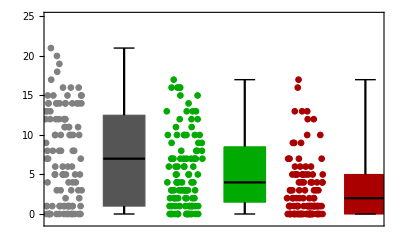

```mathematica
a1=BoxWhiskerChart[{#[[5]]&/@gk5,#[[7]]&/@gk5,#[[6]]&/@gk5},{{"MedianMarker",1,Thickness[0.004]},{"Whiskers",Thickness[0.004]},{"Fences", Thick}},ChartBaseStyle->EdgeForm[Dashing[0.99]],ChartStyle->{{Darker[Gray],Darker[Green],Darker[Red]}},Frame-> True,FrameTicks-> {None,{5,10,20},None,None},BarSpacing->1.9,PlotRange-> {{0.39,3.1},{-1,25}}];

wq1:=RandomReal[{-0.15,0.15}]
jj1=Table[0.5+wq1,Length[#[[5]]&/@gk5]];
jj2=Table[1.5+wq1,Length[#[[7]]&/@gk5]];
jj3=Table[2.5+wq1,Length[#[[6]]&/@gk5]];

a2=ListPlot[Partition[Riffle[jj1,#[[5]]&/@gk5],{2}],PlotMarkers->{Graphics[{EdgeForm[{Gray}],FaceForm[Gray],Disk[]}],Scaled[0.035]},PlotStyle-> Black,PlotRange-> {{0,4},{0,25}}];
a3=ListPlot[Partition[Riffle[jj2,#[[7]]&/@gk5],{2}],PlotMarkers->{Graphics[{EdgeForm[{Darker[Green]}],FaceForm[Darker[Green]],Disk[]}],Scaled[0.035]},PlotStyle-> Black,PlotRange-> {{0,4},{0,25}}];
a4=ListPlot[Partition[Riffle[jj3,#[[6]]&/@gk5],{2}],PlotMarkers->{Graphics[{EdgeForm[{Darker[Red]}],FaceForm[Darker[Red]],Disk[]}],Scaled[0.035]},PlotStyle-> Black,PlotRange-> {{0,4},{0,25}}];
Show[a1,a2,a3,a4]
```

#### Correlation Niche Expansion and Contraction

```mathematica
predictted=#[[5]]&/@gk5;
expanssion=#[[7]]&/@gk5;
contracction=#[[6]]&/@gk5;
```

```mathematica
SpearmanRankTest[contracction,expanssion,"TestDataTable"]
```

| Statistic | P-Value
Spearman Rank | -0.578852 | 5.31132×10^-11

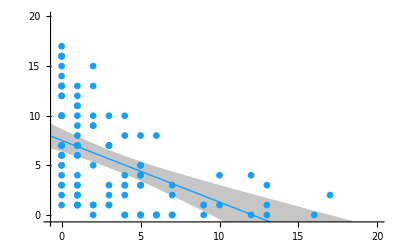

```mathematica
ECPairs5=Partition[Riffle[contracction,expanssion],{2}];
lmEC5=LinearModelFit[ECPairs5,x,x];
bands90EC5[x_]=lmEC5["MeanPredictionBands",ConfidenceLevel->.95];

ExpContr1=Plot[{lmEC5[x],bands90EC5[x]},{x,-0.7,25},PlotStyle-> {Directive[RGBColor[18/(255),160/(255),255/(255)],Thick],Lighter[Lighter[Gray]]},Filling->{2->{{1},Lighter[Lighter[Gray]]}},PlotRange-> {{-0.7,20},{-0.7,20}},Ticks->fuk[{{0,5,10,15,20},{0,5,10,15,20},"Arial",Plain,20,0.02}],TicksStyle->Thickness[0.004],AxesStyle->Thickness[0.004],AxesOrigin->{-0.7,-0.7}];

blN=Graphics[{EdgeForm[{RGBColor[18/(255),160/(255),255/(255)]}],FaceForm[RGBColor[18/(255),160/(255),255/(255)]],Disk[]}];
blG=Graphics[{EdgeForm[{Gray}],FaceForm[RGBColor[18/(255),160/(255),255/(255)]],Disk[]}];
blB=Graphics[{EdgeForm[{Black}],FaceForm[RGBColor[18/(255),160/(255),255/(255)]],Disk[]}];

ExpContr2=ListPlot[ECPairs5,PlotMarkers->{blN,Scaled[0.035]}];
Show[ExpContr1,ExpContr2]
```

## Niche Expansion and contraction as a function of niche (dis)similarity

#### Ecological proxies of Niche Expansion and Contraction: Niche Intersection-Union

```mathematica
(*Total P1,       Total P2,       MonoIntersection,    TotalCo,     MoICoIntersection,    contract,  expans*)
```

```mathematica
(*   1,             2,                     3,              4,                5,               6,        7*)
```

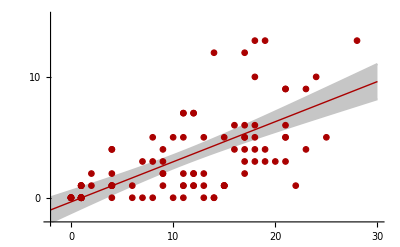

```mathematica
ECIntersContraction5=Partition[Riffle[#[[3]]&/@gk5,#[[6]]&/@gk5],{2}];

lmECIntersContraction5=LinearModelFit[ECIntersContraction5,x,x];

bands90EClmECIntersContraction5[x_]=lmECIntersContraction5["MeanPredictionBands",ConfidenceLevel->.95];


NC1=Plot[{lmECIntersContraction5[x],bands90EClmECIntersContraction5[x]},{x,-2,30},PlotStyle-> {Directive[Darker[Red],Thick],Lighter[Lighter[Gray]]},Filling->{2->{{1},Lighter[Lighter[Gray]]}},PlotRange-> {{-2,30},{-2,15}},
Ticks->fuk[{{0,5,10,15,20,25,30},{0,5,10,15,20,25,30},"Arial",Plain,20,0.02}],TicksStyle->Thickness[0.004],AxesStyle->Thickness[0.004],AxesOrigin->{-2,-2}];

rdN=Graphics[{EdgeForm[{Darker[Red]}],FaceForm[Darker[Red]],Disk[]}];
rdG=Graphics[{EdgeForm[{Gray}],FaceForm[Darker[Red]],Disk[]}];
rdB=Graphics[{EdgeForm[{Black}],FaceForm[Darker[Red]],Disk[]}];

NC2=ListPlot[ECIntersContraction5,PlotMarkers->{rdN,Scaled[0.035]}];
Show[NC1,NC2]
```

```mathematica
(* Union minus Intersection *)
```

```mathematica
umi5=((#[[1]]&/@gk5)+(#[[2]]&/@gk5))-2(#[[3]]&/@gk5)
```

{10,24,6,17,14,2,22,13,9,23,5,18,16,24,8,13,4,6,12,15,16,20,12,27,6,6,16,9,15,15,7,18,8,16,7,14,4,20,3,10,18,12,17,14,7,27,8,5,6,13,4,12,13,10,17,6,12,9,12,11,14,10,19,17,24,11,11,2,12,12,11,16,21,5,20,21,8,18,7,12,12,20,11,10,5,29,6,5,6,11,4,14,15,14,3,18,22,29,10,19,4,8,7,13,12,15,13,18}

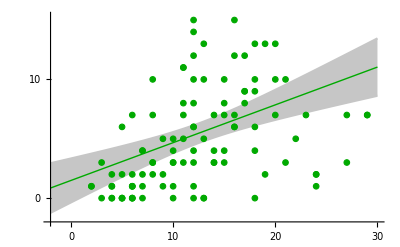

```mathematica
ECUIExpansion5=Partition[Riffle[umi5,#[[7]]&/@gk5],{2}];

lmECUIExpansion5=LinearModelFit[ECUIExpansion5,x,x];

bands90EClmECUIExpansion5[x_]=lmECUIExpansion5["MeanPredictionBands",ConfidenceLevel->.95];

NE1=Plot[{lmECUIExpansion5[x],bands90EClmECUIExpansion5[x]},{x,-2,30},PlotStyle-> {Directive[Darker[Green],Thick],Lighter[Lighter[Gray]]},Filling->{2->{{1},Lighter[Lighter[Gray]]}},PlotRange-> {{-2,30},{-2,15.3}},
Ticks->fuk[{{0,5,10,15,20,25,30},{0,5,10,15,20,25,30},"Arial",Plain,20,0.02}],TicksStyle->Thickness[0.004],AxesStyle->Thickness[0.004],AxesOrigin->{-2,-2}];

grN=Graphics[{EdgeForm[{Darker[Green]}],FaceForm[Darker[Green]],Disk[]}];
grG=Graphics[{EdgeForm[{Gray}],FaceForm[Darker[Green]],Disk[]}];
grB=Graphics[{EdgeForm[{Black}],FaceForm[Darker[Green]],Disk[]}];

NE2=ListPlot[ECUIExpansion5,PlotMarkers->{grN,Scaled[0.035]}];
Show[NE1,NE2]
```

#### Jaccard Distance

```mathematica
nicheOverlapDistancesJac[{par1_,par2_,coul_,threashold_}]:=(
th1=If[#≥ threashold,1,0]&;
bit1=If[#≥ 1,1,0]&;
UnionFunTwoToOne=If[#== 2,1,#]&;  (*NewNewNewNewNewNewNewNewNewNew*)

qf1=Map[th1,par1,{2}];
v1=bit1/@Total[qf1];

qf2=Map[th1,par2,{2}];
v2=bit1/@Total[qf2];

overlapMono=v1 v2;

UnionP1P2 = Map[UnionFunTwoToOne ,(v1+v2),{1}];    (*NewNewNewNewNewNewNewNewNewNew*)

qfcocul=Map[th1,coul,{2}];
vcocul=bit1/@Total[qfcocul];

MoICoIntersection=overlapMono vcocul;

contractxk=Total[overlapMono]-Total[MoICoIntersection];
expandxk=Total[vcocul]-Total[MoICoIntersection];

contract=funNe[contractxk];
expans=funNe[expandxk];

(*
 SuperNEvector= vcocul + UnionP1P2 ; (*NewNewNewNewNewNewNewNewNewNew*)    
SuperNEnumber=Count[SuperNEvector,1]; (*NewNewNewNewNewNewNewNewNewNew*)  
*)

SuperNEnumber=Count[Partition[Riffle[vcocul,UnionP1P2],{2}],{1,0}];

Jac=N[Total[overlapMono]/Total[UnionP1P2]];
InvJac=N[(Total[UnionP1P2]-Total[overlapMono])/Total[UnionP1P2]];


{Total[v1],Total[v2],Total[overlapMono],Total[vcocul],Total[MoICoIntersection],contract,expans,SuperNEnumber,Jac,InvJac}


)
```

```mathematica
(*Total P1,       Total P2,       MonoIntersection,    TotalCo,     MoICoIntersection,    contract,  expans,  SuperExpans,  Jacc,  InvJacc*)
```

```mathematica
(*   1,             2,                     3,              4,                5,               6,        7,        8,          9,      10*)
```

```mathematica
gk5KJaccK=Map[nicheOverlapDistancesJac,cases5,{1}]
```

{{25,15,15,15,14,1,1,0,0.6,0.4},{25,1,1,1,0,1,1,0,0.04,0.96},{25,23,21,19,18,3,1,0,0.777778,0.222222},{25,12,10,22,10,0,12,0,0.37037,0.62963},{1,15,1,18,1,0,17,5,0.0666667,0.933333},{1,1,0,1,0,0,1,1,0.,1.},{1,23,1,17,1,0,16,1,0.0434783,0.956522},{1,12,0,16,0,0,16,8,0.,1.},{24,15,15,16,14,1,2,0,0.625,0.375},{24,1,1,8,1,0,7,1,0.0416667,0.958333},{24,23,21,16,16,5,0,0,0.807692,0.192308},{24,12,9,17,7,2,10,0,0.333333,0.666667},{25,15,12,25,10,2,15,1,0.428571,0.571429},{25,1,1,2,0,1,2,0,0.04,0.96},{25,23,20,27,17,3,10,2,0.714286,0.285714},{25,12,12,5,5,7,0,0,0.48,0.52},{15,17,14,16,14,0,2,1,0.777778,0.222222},{15,21,15,16,14,1,2,0,0.714286,0.285714},{15,11,7,21,7,0,14,5,0.368421,0.631579},{15,28,14,24,14,0,10,1,0.482759,0.517241},{1,17,1,6,0,1,6,1,0.0588235,0.941176},{1,21,1,17,1,0,16,3,0.047619,0.952381},{1,11,0,6,0,0,6,2,0.,1.},{1,28,1,4,1,0,3,0,0.0357143,0.964286},{23,17,17,15,15,2,0,0,0.73913,0.26087},{23,21,19,15,15,4,0,0,0.76,0.24},{23,11,9,13,6,3,7,0,0.36,0.64},{23,28,21,21,16,5,5,0,0.7,0.3},{12,17,7,11,4,3,7,1,0.318182,0.681818},{12,21,9,13,5,4,8,1,0.375,0.625},{12,11,8,7,3,5,4,2,0.533333,0.466667},{12,28,11,22,9,2,13,0,0.37931,0.62069},{17,25,17,16,13,4,3,0,0.68,0.32},{17,1,1,7,1,0,6,0,0.0588235,0.941176},{17,24,17,16,14,3,2,0,0.708333,0.291667},{17,25,14,6,2,12,4,0,0.5,0.5},{21,25,21,15,15,6,0,0,0.84,0.16},{21,1,1,11,1,0,10,1,0.047619,0.952381},{21,24,21,12,12,9,0,0,0.875,0.125},{21,25,18,12,8,10,4,0,0.642857,0.357143},{11,25,9,16,7,2,9,0,0.333333,0.666667},{11,1,0,15,0,0,15,7,0.,1.},{11,24,9,16,8,1,8,1,0.346154,0.653846},{11,25,11,9,6,5,3,0,0.44,0.56},{28,25,23,23,19,4,4,0,0.766667,0.233333},{28,1,1,7,0,1,7,0,0.0357143,0.964286},{28,24,22,28,21,1,7,0,0.733333,0.266667},{28,25,24,8,8,16,0,0,0.827586,0.172414},{17,13,12,11,10,2,1,0,0.666667,0.333333},{17,4,4,10,0,4,10,3,0.235294,0.764706},{17,19,16,12,12,4,0,0,0.8,0.2},{17,21,13,11,8,5,3,0,0.52,0.48},{17,30,17,5,5,12,0,0,0.566667,0.433333},{21,13,12,14,11,1,3,0,0.545455,0.454545},{21,4,4,11,2,2,9,0,0.190476,0.809524},{21,19,17,12,12,5,0,0,0.73913,0.26087},{21,21,15,18,10,5,8,1,0.555556,0.444444},{21,30,21,13,12,9,1,0,0.7,0.3},{11,13,6,15,5,1,10,3,0.333333,0.666667},{11,4,2,12,1,1,11,3,0.153846,0.846154},{11,19,8,11,8,0,3,1,0.363636,0.636364},{11,21,11,7,4,7,3,1,0.52381,0.47619},{11,30,11,6,4,7,2,0,0.366667,0.633333},{28,13,12,20,11,1,9,1,0.413793,0.586207},{28,4,4,5,3,1,2,0,0.142857,0.857143},{28,19,18,22,15,3,7,1,0.62069,0.37931},{28,21,19,9,6,13,3,0,0.633333,0.366667},{28,30,28,16,15,13,1,0,0.933333,0.0666667},{13,25,13,18,12,1,6,1,0.52,0.48},{13,1,1,13,1,0,12,3,0.0769231,0.923077},{13,24,13,16,11,2,5,1,0.541667,0.458333},{13,25,11,22,10,1,12,1,0.407407,0.592593},{4,25,4,14,4,0,10,1,0.16,0.84},{4,1,0,6,0,0,6,5,0.,1.},{4,24,4,10,3,1,7,1,0.166667,0.833333},{4,25,4,3,0,4,3,0,0.16,0.84},{19,25,18,16,14,4,2,0,0.692308,0.307692},{19,1,1,7,1,0,6,1,0.0526316,0.947368},{19,24,18,12,12,6,0,0,0.72,0.28},{19,25,16,10,10,6,0,0,0.571429,0.428571},{21,25,17,16,12,5,4,0,0.586207,0.413793},{21,1,1,14,1,0,13,2,0.047619,0.952381},{21,24,17,19,11,6,8,1,0.607143,0.392857},{21,25,18,5,5,13,0,0,0.642857,0.357143},{30,25,25,20,20,5,0,0,0.833333,0.166667},{30,1,1,8,1,0,7,0,0.0333333,0.966667},{30,24,24,15,14,10,1,0,0.8,0.2},{30,25,25,10,8,17,2,0,0.833333,0.166667},{15,13,11,18,11,0,7,3,0.647059,0.352941},{15,4,4,14,3,1,11,2,0.266667,0.733333},{15,19,15,15,14,1,1,1,0.789474,0.210526},{15,21,11,17,10,1,7,2,0.44,0.56},{15,30,15,18,14,1,4,0,0.5,0.5},{1,13,0,16,0,0,16,2,0.,1.},{1,4,1,3,0,1,3,2,0.25,0.75},{1,19,1,5,1,0,4,1,0.0526316,0.947368},{1,21,0,5,0,0,5,1,0.,1.},{1,30,1,8,1,0,7,0,0.0333333,0.966667},{23,13,13,18,13,0,5,2,0.565217,0.434783},{23,4,4,16,3,1,13,0,0.173913,0.826087},{23,19,19,17,16,3,1,0,0.826087,0.173913},{23,21,18,16,13,5,3,1,0.692308,0.307692},{23,30,23,15,14,9,1,0,0.766667,0.233333},{12,13,6,19,6,0,13,3,0.315789,0.684211},{12,4,2,1,0,2,1,0,0.142857,0.857143},{12,19,8,8,5,3,3,0,0.347826,0.652174},{12,21,10,10,5,5,5,1,0.434783,0.565217},{12,30,12,5,5,7,0,0,0.4,0.6}}

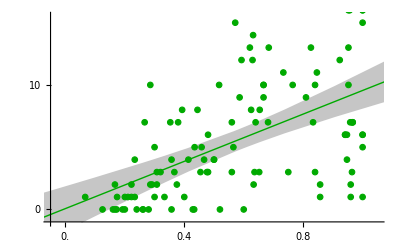

```mathematica
ECUIExpansion5Jacc=Partition[Riffle[#[[10]]&/@gk5KJaccK,#[[7]]&/@gk5KJaccK],{2}];

lmECUIExpansion5Jacc=LinearModelFit[ECUIExpansion5Jacc,x,x];

bands90EClmECUIExpansion5Jacc[x_]=lmECUIExpansion5Jacc["MeanPredictionBands",ConfidenceLevel->.95];


Exp1=Plot[{lmECUIExpansion5Jacc[x],bands90EClmECUIExpansion5Jacc[x]},{x,-2,30},PlotStyle-> {Directive[Darker[Green],Thick],Lighter[Lighter[Gray]]},Filling->{2->{{1},Lighter[Lighter[Gray]]}},PlotRange-> {{-0.05,1.05},{-1,15.5}},
Ticks->fuk[{{0.0,0.2, 0.4, 0.6, 0.8,1.0},{0,5,10,15,20,25,30},"Arial",Plain,20,0.02}],TicksStyle->Thickness[0.004],AxesStyle->Thickness[0.004],AxesOrigin->{-0.05,-1}];

grN=Graphics[{EdgeForm[{Darker[Green]}],FaceForm[Darker[Green]],Disk[]}];
grG=Graphics[{EdgeForm[{Gray}],FaceForm[Darker[Green]],Disk[]}];
grB=Graphics[{EdgeForm[{Black}],FaceForm[Darker[Green]],Disk[]}];

Exp2=ListPlot[ECUIExpansion5Jacc,PlotMarkers->{grN,Scaled[0.035]}];
Show[Exp1,Exp2]
```

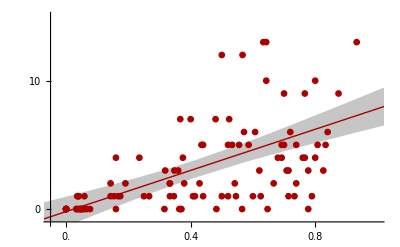

```mathematica
ECIntersContraction5Jacc=Partition[Riffle[#[[9]]&/@gk5KJaccK,#[[6]]&/@gk5KJaccK],{2}];

lmECIntersContraction5Jacc=LinearModelFit[ECIntersContraction5Jacc,x,x];

bands90EClmECIntersContraction5Jacc[x_]=lmECIntersContraction5Jacc["MeanPredictionBands",ConfidenceLevel->.95];

Contr1=Plot[{lmECIntersContraction5Jacc[x],bands90EClmECIntersContraction5Jacc[x]},{x,-2,30},PlotStyle-> {Directive[Darker[Red],Thick],Lighter[Lighter[Gray]]},Filling->{2->{{1},Lighter[Lighter[Gray]]}},PlotRange-> {{-0.05,1.0},{-1,15}},
Ticks->fuk[{{0.0,0.2, 0.4, 0.6, 0.8,1.0},{0,5,10,15,20,25,30},"Arial",Plain,20,0.02}],TicksStyle->Thickness[0.004],AxesStyle->Thickness[0.004],AxesOrigin->{-0.05,-1}];

rdN=Graphics[{EdgeForm[{Darker[Red]}],FaceForm[Darker[Red]],Disk[]}];
rdG=Graphics[{EdgeForm[{Gray}],FaceForm[Darker[Red]],Disk[]}];
rdB=Graphics[{EdgeForm[{Black}],FaceForm[Darker[Red]],Disk[]}];

Contr2=ListPlot[ECIntersContraction5Jacc,PlotMarkers->{rdN,Scaled[0.035]}];
Show[Contr1,Contr2]
```

## Niche Expansion and contraction in specialists vs. generalists

#### Specialists - Generalists

```mathematica
genspeDat5={{#[[1]],#[[2]]},{#[[7]]}}&/@gk5
```

{{{25,15},{1}},{{25,1},{1}},{{25,23},{1}},{{25,12},{12}},{{1,15},{17}},{{1,1},{1}},{{1,23},{16}},{{1,12},{16}},{{24,15},{2}},{{24,1},{7}},{{24,23},{0}},{{24,12},{10}},{{25,15},{15}},{{25,1},{2}},{{25,23},{10}},{{25,12},{0}},{{15,17},{2}},{{15,21},{2}},{{15,11},{14}},{{15,28},{10}},{{1,17},{6}},{{1,21},{16}},{{1,11},{6}},{{1,28},{3}},{{23,17},{0}},{{23,21},{0}},{{23,11},{7}},{{23,28},{5}},{{12,17},{7}},{{12,21},{8}},{{12,11},{4}},{{12,28},{13}},{{17,25},{3}},{{17,1},{6}},{{17,24},{2}},{{17,25},{4}},{{21,25},{0}},{{21,1},{10}},{{21,24},{0}},{{21,25},{4}},{{11,25},{9}},{{11,1},{15}},{{11,24},{8}},{{11,25},{3}},{{28,25},{4}},{{28,1},{7}},{{28,24},{7}},{{28,25},{0}},{{17,13},{1}},{{17,4},{10}},{{17,19},{0}},{{17,21},{3}},{{17,30},{0}},{{21,13},{3}},{{21,4},{9}},{{21,19},{0}},{{21,21},{8}},{{21,30},{1}},{{11,13},{10}},{{11,4},{11}},{{11,19},{3}},{{11,21},{3}},{{11,30},{2}},{{28,13},{9}},{{28,4},{2}},{{28,19},{7}},{{28,21},{3}},{{28,30},{1}},{{13,25},{6}},{{13,1},{12}},{{13,24},{5}},{{13,25},{12}},{{4,25},{10}},{{4,1},{6}},{{4,24},{7}},{{4,25},{3}},{{19,25},{2}},{{19,1},{6}},{{19,24},{0}},{{19,25},{0}},{{21,25},{4}},{{21,1},{13}},{{21,24},{8}},{{21,25},{0}},{{30,25},{0}},{{30,1},{7}},{{30,24},{1}},{{30,25},{2}},{{15,13},{7}},{{15,4},{11}},{{15,19},{1}},{{15,21},{7}},{{15,30},{4}},{{1,13},{16}},{{1,4},{3}},{{1,19},{4}},{{1,21},{5}},{{1,30},{7}},{{23,13},{5}},{{23,4},{13}},{{23,19},{1}},{{23,21},{3}},{{23,30},{1}},{{12,13},{13}},{{12,4},{1}},{{12,19},{3}},{{12,21},{5}},{{12,30},{0}}}

```mathematica
genspeDatSimple5=Partition[Flatten[genspeDat5],{3}];
```

```mathematica
Length[genspeDatSimple5]
```

108

#### Niche Expansion and Contraction Nonlinear model Fit

```mathematica
(*Niche Expansion*)
```

```mathematica
genspeDat25=Partition[Flatten[genspeDat5],{3}]
```

{{25,15,1},{25,1,1},{25,23,1},{25,12,12},{1,15,17},{1,1,1},{1,23,16},{1,12,16},{24,15,2},{24,1,7},{24,23,0},{24,12,10},{25,15,15},{25,1,2},{25,23,10},{25,12,0},{15,17,2},{15,21,2},{15,11,14},{15,28,10},{1,17,6},{1,21,16},{1,11,6},{1,28,3},{23,17,0},{23,21,0},{23,11,7},{23,28,5},{12,17,7},{12,21,8},{12,11,4},{12,28,13},{17,25,3},{17,1,6},{17,24,2},{17,25,4},{21,25,0},{21,1,10},{21,24,0},{21,25,4},{11,25,9},{11,1,15},{11,24,8},{11,25,3},{28,25,4},{28,1,7},{28,24,7},{28,25,0},{17,13,1},{17,4,10},{17,19,0},{17,21,3},{17,30,0},{21,13,3},{21,4,9},{21,19,0},{21,21,8},{21,30,1},{11,13,10},{11,4,11},{11,19,3},{11,21,3},{11,30,2},{28,13,9},{28,4,2},{28,19,7},{28,21,3},{28,30,1},{13,25,6},{13,1,12},{13,24,5},{13,25,12},{4,25,10},{4,1,6},{4,24,7},{4,25,3},{19,25,2},{19,1,6},{19,24,0},{19,25,0},{21,25,4},{21,1,13},{21,24,8},{21,25,0},{30,25,0},{30,1,7},{30,24,1},{30,25,2},{15,13,7},{15,4,11},{15,19,1},{15,21,7},{15,30,4},{1,13,16},{1,4,3},{1,19,4},{1,21,5},{1,30,7},{23,13,5},{23,4,13},{23,19,1},{23,21,3},{23,30,1},{12,13,13},{12,4,1},{12,19,3},{12,21,5},{12,30,0}}

```mathematica
nlmExpansion5=NonlinearModelFit[genspeDat25, A Exp[-((x-xm)^2/(2 vx^2)+(y-ym)^2/(2 vy^2))],{A,xm,ym,vx,vy},{x,y},MaxIterations->∞(*,WorkingPrecision->5*)]
```

FittedModel[22.7068 ⅇ^(-0.00017715 (63.1307+x)^2-0.00166552 (-«17»+y)^2)]

```mathematica
{fitExpansion5 = nlmExpansion5["BestFit"],Show[Plot3D[fitExpansion5,{x,1,30},{y,1,30},ColorFunction->"DarkRainbow", PlotStyle->Directive[Opacity[0.8],Red],Mesh->None,PlotRange->All], Graphics3D[{PointSize[0.025],Point[genspeDat25]}]]}
```

{22.7068 ⅇ^(-0.00017715 (63.1307+x)^2-0.00166552 (-6.63495+y)^2),-Graphics3D-}

```mathematica
nlmExpansion5["ANOVATable"]
```

| DF | SS | MS
Model | 5 | 3762.15 | 752.43
Error | 103 | 1893.85 | 18.3869
Uncorrected Total | 108 | 5656. | 
Corrected Total | 107 | 2366.96 |

```mathematica
anovaE=nlmExpansion5["ANOVATableEntries"]
```

{{5,3762.15,752.43},{103,1893.85,18.3869},{108,5656.},{107,2366.96}}

```mathematica
fRatioE=anovaE[[1,3]]/anovaE[[2,3]]
```

40.9221

```mathematica
pValueE=1-CDF[FRatioDistribution[anovaE[[1,1]],anovaE[[2,1]]],fRatioE]
```

0.

```mathematica
(*Niche Contraction*)
```

```mathematica
genContrDat5={{#[[1]],#[[2]]},{#[[6]]}}&/@gk5
```

{{{25,15},{1}},{{25,1},{1}},{{25,23},{3}},{{25,12},{0}},{{1,15},{0}},{{1,1},{0}},{{1,23},{0}},{{1,12},{0}},{{24,15},{1}},{{24,1},{0}},{{24,23},{5}},{{24,12},{2}},{{25,15},{2}},{{25,1},{1}},{{25,23},{3}},{{25,12},{7}},{{15,17},{0}},{{15,21},{1}},{{15,11},{0}},{{15,28},{0}},{{1,17},{1}},{{1,21},{0}},{{1,11},{0}},{{1,28},{0}},{{23,17},{2}},{{23,21},{4}},{{23,11},{3}},{{23,28},{5}},{{12,17},{3}},{{12,21},{4}},{{12,11},{5}},{{12,28},{2}},{{17,25},{4}},{{17,1},{0}},{{17,24},{3}},{{17,25},{12}},{{21,25},{6}},{{21,1},{0}},{{21,24},{9}},{{21,25},{10}},{{11,25},{2}},{{11,1},{0}},{{11,24},{1}},{{11,25},{5}},{{28,25},{4}},{{28,1},{1}},{{28,24},{1}},{{28,25},{16}},{{17,13},{2}},{{17,4},{4}},{{17,19},{4}},{{17,21},{5}},{{17,30},{12}},{{21,13},{1}},{{21,4},{2}},{{21,19},{5}},{{21,21},{5}},{{21,30},{9}},{{11,13},{1}},{{11,4},{1}},{{11,19},{0}},{{11,21},{7}},{{11,30},{7}},{{28,13},{1}},{{28,4},{1}},{{28,19},{3}},{{28,21},{13}},{{28,30},{13}},{{13,25},{1}},{{13,1},{0}},{{13,24},{2}},{{13,25},{1}},{{4,25},{0}},{{4,1},{0}},{{4,24},{1}},{{4,25},{4}},{{19,25},{4}},{{19,1},{0}},{{19,24},{6}},{{19,25},{6}},{{21,25},{5}},{{21,1},{0}},{{21,24},{6}},{{21,25},{13}},{{30,25},{5}},{{30,1},{0}},{{30,24},{10}},{{30,25},{17}},{{15,13},{0}},{{15,4},{1}},{{15,19},{1}},{{15,21},{1}},{{15,30},{1}},{{1,13},{0}},{{1,4},{1}},{{1,19},{0}},{{1,21},{0}},{{1,30},{0}},{{23,13},{0}},{{23,4},{1}},{{23,19},{3}},{{23,21},{5}},{{23,30},{9}},{{12,13},{0}},{{12,4},{2}},{{12,19},{3}},{{12,21},{5}},{{12,30},{7}}}

```mathematica
genContrDatSimple5=Partition[Flatten[genContrDat5],{3}]
```

{{25,15,1},{25,1,1},{25,23,3},{25,12,0},{1,15,0},{1,1,0},{1,23,0},{1,12,0},{24,15,1},{24,1,0},{24,23,5},{24,12,2},{25,15,2},{25,1,1},{25,23,3},{25,12,7},{15,17,0},{15,21,1},{15,11,0},{15,28,0},{1,17,1},{1,21,0},{1,11,0},{1,28,0},{23,17,2},{23,21,4},{23,11,3},{23,28,5},{12,17,3},{12,21,4},{12,11,5},{12,28,2},{17,25,4},{17,1,0},{17,24,3},{17,25,12},{21,25,6},{21,1,0},{21,24,9},{21,25,10},{11,25,2},{11,1,0},{11,24,1},{11,25,5},{28,25,4},{28,1,1},{28,24,1},{28,25,16},{17,13,2},{17,4,4},{17,19,4},{17,21,5},{17,30,12},{21,13,1},{21,4,2},{21,19,5},{21,21,5},{21,30,9},{11,13,1},{11,4,1},{11,19,0},{11,21,7},{11,30,7},{28,13,1},{28,4,1},{28,19,3},{28,21,13},{28,30,13},{13,25,1},{13,1,0},{13,24,2},{13,25,1},{4,25,0},{4,1,0},{4,24,1},{4,25,4},{19,25,4},{19,1,0},{19,24,6},{19,25,6},{21,25,5},{21,1,0},{21,24,6},{21,25,13},{30,25,5},{30,1,0},{30,24,10},{30,25,17},{15,13,0},{15,4,1},{15,19,1},{15,21,1},{15,30,1},{1,13,0},{1,4,1},{1,19,0},{1,21,0},{1,30,0},{23,13,0},{23,4,1},{23,19,3},{23,21,5},{23,30,9},{12,13,0},{12,4,2},{12,19,3},{12,21,5},{12,30,7}}

```mathematica
nlmContraction5=NonlinearModelFit[genContrDatSimple5, A Exp[-((x-xm)^2/(2 vx^2)+(y-ym)^2/(2 vy^2))],{A,xm,ym,vx,vy},{x,y}(*,MaxIterations->∞,WorkingPrecision->5*)]
```

FittedModel[32.1539 ⅇ^(-0.00148502 (-41.528+x)^2-0.00161335 (-«18»+y)^2)]

```mathematica
{fitContraction5 = nlmContraction5["BestFit"],Show[Plot3D[fitContraction5,{x,1,30},{y,1,30},ColorFunction->"DarkRainbow", PlotStyle->Directive[Opacity[0.8],Red],Mesh->None,PlotRange->All], Graphics3D[{PointSize[0.028],Point[genContrDatSimple5]}]]}
```

{32.1539 ⅇ^(-0.00148502 (-41.528+x)^2-0.00161335 (-50.0887+y)^2),-Graphics3D-}

```mathematica
nlmContraction5["ANOVATable"]
```

| DF | SS | MS
Model | 5 | 1944.79 | 388.959
Error | 103 | 712.205 | 6.91461
Uncorrected Total | 108 | 2657. | 
Corrected Total | 107 | 1542.1 |

```mathematica
anovaC=nlmContraction5["ANOVATableEntries"]
```

{{5,1944.79,388.959},{103,712.205,6.91461},{108,2657.},{107,1542.1}}

```mathematica
fRatioC=anovaC[[1,3]]/anovaC[[2,3]]
```

56.2517

```mathematica
pValueC=1-CDF[FRatioDistribution[anovaC[[1,1]],anovaC[[2,1]]],fRatioC]
```

0.

## Niche Expansion and contraction vs. phylogenetic distance between partners

#### Phylogeny

```mathematica
ki5=StringReplace[#,{"-"->" ", " "-> ""}]&/@comType[[40;;147]]
```

{ABR ABH,ABR BSH,ABR ECH,ABR SOH,BSR ABH,BSR BSH,BSR ECH,BSR SOH,ECR ABH,ECR BSH,ECR ECH,ECR SOH,SOR ABH,SOR BSH,SOR ECH,SOR SOH,ABH ABW,ABH ECW,ABH SOW,ABH PFW,BSH ABW,BSH ECW,BSH SOW,BSH PFW,ECH ABW,ECH ECW,ECH SOW,ECH PFW,SOH ABW,SOH ECW,SOH SOW,SOH PFW,ABW ABR,ABW BSR,ABW ECR,ABW SOR,ECW ABR,ECW BSR,ECW ECR,ECW SOR,SOW ABR,SOW BSR,SOW ECR,SOW SOR,PFW ABR,PFW BSR,PFW ECR,PFW SOR,ABW ABL,ABW BSL,ABW ECL,ABW SOL,ABW PFL,ECW ABL,ECW BSL,ECW ECL,ECW SOL,ECW PFL,SOW ABL,SOW BSL,SOW ECL,SOW SOL,SOW PFL,PFW ABL,PFW BSL,PFW ECL,PFW SOL,PFW PFL,ABL ABR,ABL BSR,ABL ECR,ABL SOR,BSL ABR,BSL BSR,BSL ECR,BSL SOR,ECL ABR,ECL BSR,ECL ECR,ECL SOR,SOL ABR,SOL BSR,SOL ECR,SOL SOR,PFL ABR,PFL BSR,PFL ECR,PFL SOR,ABH ABL,ABH BSL,ABH ECL,ABH SOL,ABH PFL,BSH ABL,BSH BS L,BSH ECL,BSH SOL,BSH PFL,ECH ABL,ECH BSL,ECH ECL,ECH SOL,ECH PFL,SOH ABL,SOH BSL,SOH ECL,SOH SOL,SOH PFL}

```mathematica
pai5=StringSplit/@ki5
```

{{ABR,ABH},{ABR,BSH},{ABR,ECH},{ABR,SOH},{BSR,ABH},{BSR,BSH},{BSR,ECH},{BSR,SOH},{ECR,ABH},{ECR,BSH},{ECR,ECH},{ECR,SOH},{SOR,ABH},{SOR,BSH},{SOR,ECH},{SOR,SOH},{ABH,ABW},{ABH,ECW},{ABH,SOW},{ABH,PFW},{BSH,ABW},{BSH,ECW},{BSH,SOW},{BSH,PFW},{ECH,ABW},{ECH,ECW},{ECH,SOW},{ECH,PFW},{SOH,ABW},{SOH,ECW},{SOH,SOW},{SOH,PFW},{ABW,ABR},{ABW,BSR},{ABW,ECR},{ABW,SOR},{ECW,ABR},{ECW,BSR},{ECW,ECR},{ECW,SOR},{SOW,ABR},{SOW,BSR},{SOW,ECR},{SOW,SOR},{PFW,ABR},{PFW,BSR},{PFW,ECR},{PFW,SOR},{ABW,ABL},{ABW,BSL},{ABW,ECL},{ABW,SOL},{ABW,PFL},{ECW,ABL},{ECW,BSL},{ECW,ECL},{ECW,SOL},{ECW,PFL},{SOW,ABL},{SOW,BSL},{SOW,ECL},{SOW,SOL},{SOW,PFL},{PFW,ABL},{PFW,BSL},{PFW,ECL},{PFW,SOL},{PFW,PFL},{ABL,ABR},{ABL,BSR},{ABL,ECR},{ABL,SOR},{BSL,ABR},{BSL,BSR},{BSL,ECR},{BSL,SOR},{ECL,ABR},{ECL,BSR},{ECL,ECR},{ECL,SOR},{SOL,ABR},{SOL,BSR},{SOL,ECR},{SOL,SOR},{PFL,ABR},{PFL,BSR},{PFL,ECR},{PFL,SOR},{ABH,ABL},{ABH,BSL},{ABH,ECL},{ABH,SOL},{ABH,PFL},{BSH,ABL},{BSH,BS,L},{BSH,ECL},{BSH,SOL},{BSH,PFL},{ECH,ABL},{ECH,BSL},{ECH,ECL},{ECH,SOL},{ECH,PFL},{SOH,ABL},{SOH,BSL},{SOH,ECL},{SOH,SOL},{SOH,PFL}}

```mathematica
qz5=MapAt[(#<>"5"&),pai5,{All,All}]
```

{{ABR5,ABH5},{ABR5,BSH5},{ABR5,ECH5},{ABR5,SOH5},{BSR5,ABH5},{BSR5,BSH5},{BSR5,ECH5},{BSR5,SOH5},{ECR5,ABH5},{ECR5,BSH5},{ECR5,ECH5},{ECR5,SOH5},{SOR5,ABH5},{SOR5,BSH5},{SOR5,ECH5},{SOR5,SOH5},{ABH5,ABW5},{ABH5,ECW5},{ABH5,SOW5},{ABH5,PFW5},{BSH5,ABW5},{BSH5,ECW5},{BSH5,SOW5},{BSH5,PFW5},{ECH5,ABW5},{ECH5,ECW5},{ECH5,SOW5},{ECH5,PFW5},{SOH5,ABW5},{SOH5,ECW5},{SOH5,SOW5},{SOH5,PFW5},{ABW5,ABR5},{ABW5,BSR5},{ABW5,ECR5},{ABW5,SOR5},{ECW5,ABR5},{ECW5,BSR5},{ECW5,ECR5},{ECW5,SOR5},{SOW5,ABR5},{SOW5,BSR5},{SOW5,ECR5},{SOW5,SOR5},{PFW5,ABR5},{PFW5,BSR5},{PFW5,ECR5},{PFW5,SOR5},{ABW5,ABL5},{ABW5,BSL5},{ABW5,ECL5},{ABW5,SOL5},{ABW5,PFL5},{ECW5,ABL5},{ECW5,BSL5},{ECW5,ECL5},{ECW5,SOL5},{ECW5,PFL5},{SOW5,ABL5},{SOW5,BSL5},{SOW5,ECL5},{SOW5,SOL5},{SOW5,PFL5},{PFW5,ABL5},{PFW5,BSL5},{PFW5,ECL5},{PFW5,SOL5},{PFW5,PFL5},{ABL5,ABR5},{ABL5,BSR5},{ABL5,ECR5},{ABL5,SOR5},{BSL5,ABR5},{BSL5,BSR5},{BSL5,ECR5},{BSL5,SOR5},{ECL5,ABR5},{ECL5,BSR5},{ECL5,ECR5},{ECL5,SOR5},{SOL5,ABR5},{SOL5,BSR5},{SOL5,ECR5},{SOL5,SOR5},{PFL5,ABR5},{PFL5,BSR5},{PFL5,ECR5},{PFL5,SOR5},{ABH5,ABL5},{ABH5,BSL5},{ABH5,ECL5},{ABH5,SOL5},{ABH5,PFL5},{BSH5,ABL5},{BSH5,BS5,L5},{BSH5,ECL5},{BSH5,SOL5},{BSH5,PFL5},{ECH5,ABL5},{ECH5,BSL5},{ECH5,ECL5},{ECH5,SOL5},{ECH5,PFL5},{SOH5,ABL5},{SOH5,BSL5},{SOH5,ECL5},{SOH5,SOL5},{SOH5,PFL5}}

```mathematica
qzK5={{"ABR5","ABH5"},{"ABR5","BSH5"},{"ABR5","ECH5"},{"ABR5","SOH5"},{"BSR5","ABH5"},{"BSR5","BSH5"},{"BSR5","ECH5"},{"BSR5","SOH5"},{"ECR5","ABH5"},{"ECR5","BSH5"},{"ECR5","ECH5"},{"ECR5","SOH5"},{"SOR5","ABH5"},{"SOR5","BSH5"},{"SOR5","ECH5"},{"SOR5","SOH5"},{"ABH5","ABW5"},{"ABH5","ECW5"},{"ABH5","SOW5"},{"ABH5","PFW5"},{"BSH5","ABW5"},{"BSH5","ECW5"},{"BSH5","SOW5"},{"BSH5","PFW5"},{"ECH5","ABW5"},{"ECH5","ECW5"},{"ECH5","SOW5"},{"ECH5","PFW5"},{"SOH5","ABW5"},{"SOH5","ECW5"},{"SOH5","SOW5"},{"SOH5","PFW5"},{"ABW5","ABR5"},{"ABW5","BSR5"},{"ABW5","ECR5"},{"ABW5","SOR5"},{"ECW5","ABR5"},{"ECW5","BSR5"},{"ECW5","ECR5"},{"ECW5","SOR5"},{"SOW5","ABR5"},{"SOW5","BSR5"},{"SOW5","ECR5"},{"SOW5","SOR5"},{"PFW5","ABR5"},{"PFW5","BSR5"},{"PFW5","ECR5"},{"PFW5","SOR5"},{"ABW5","ABL5"},{"ABW5","BSL5"},{"ABW5","ECL5"},{"ABW5","SOL5"},{"ABW5","PFL5"},{"ECW5","ABL5"},{"ECW5","BSL5"},{"ECW5","ECL5"},{"ECW5","SOL5"},{"ECW5","PFL5"},{"SOW5","ABL5"},{"SOW5","BSL5"},{"SOW5","ECL5"},{"SOW5","SOL5"},{"SOW5","PFL5"},{"PFW5","ABL5"},{"PFW5","BSL5"},{"PFW5","ECL5"},{"PFW5","SOL5"},{"PFW5","PFL5"},{"ABL5","ABR5"},{"ABL5","BSR5"},{"ABL5","ECR5"},{"ABL5","SOR5"},{"BSL5","ABR5"},{"BSL5","BSR5"},{"BSL5","ECR5"},{"BSL5","SOR5"},{"ECL5","ABR5"},{"ECL5","BSR5"},{"ECL5","ECR5"},{"ECL5","SOR5"},{"SOL5","ABR5"},{"SOL5","BSR5"},{"SOL5","ECR5"},{"SOL5","SOR5"},{"PFL5","ABR5"},{"PFL5","BSR5"},{"PFL5","ECR5"},{"PFL5","SOR5"},{"ABH5","ABL5"},{"ABH5","BSL5"},{"ABH5","ECL5"},{"ABH5","SOL5"},{"ABH5","PFL5"},{"BSH5","ABL5"},{"BSH5","BSL5"},{"BSH5","ECL5"},{"BSH5","SOL5"},{"BSH5","PFL5"},{"ECH5","ABL5"},{"ECH5","BSL5"},{"ECH5","ECL5"},{"ECH5","SOL5"},{"ECH5","PFL5"},{"SOH5","ABL5"},{"SOH5","BSL5"},{"SOH5","ECL5"},{"SOH5","SOL5"},{"SOH5","PFL5"}};
```

```mathematica
mondef5=MapAt[ToExpression,qzK5,{All,All}];
```

```mathematica
jop5=Table[Join[qzK5[[i]],{poStingHour5[[i]]}],{i,1,Length[poStingHour5]}]
```

{{ABR5,ABH5,ABRABH5},{ABR5,BSH5,ABRBSH5},{ABR5,ECH5,ABRECH5},{ABR5,SOH5,ABRSOH5},{BSR5,ABH5,BSRABH5},{BSR5,BSH5,BSRBSH5},{BSR5,ECH5,BSRECH5},{BSR5,SOH5,BSRSOH5},{ECR5,ABH5,ECRABH5},{ECR5,BSH5,ECRBSH5},{ECR5,ECH5,ECRECH5},{ECR5,SOH5,ECRSOH5},{SOR5,ABH5,SORABH5},{SOR5,BSH5,SORBSH5},{SOR5,ECH5,SORECH5},{SOR5,SOH5,SORSOH5},{ABH5,ABW5,ABHABW5},{ABH5,ECW5,ABHECW5},{ABH5,SOW5,ABHSOW5},{ABH5,PFW5,ABHPFW5},{BSH5,ABW5,BSHABW5},{BSH5,ECW5,BSHECW5},{BSH5,SOW5,BSHSOW5},{BSH5,PFW5,BSHPFW5},{ECH5,ABW5,ECHABW5},{ECH5,ECW5,ECHECW5},{ECH5,SOW5,ECHSOW5},{ECH5,PFW5,ECHPFW5},{SOH5,ABW5,SOHABW5},{SOH5,ECW5,SOHECW5},{SOH5,SOW5,SOHSOW5},{SOH5,PFW5,SOHPFW5},{ABW5,ABR5,ABWABR5},{ABW5,BSR5,ABWBSR5},{ABW5,ECR5,ABWECR5},{ABW5,SOR5,ABWSOR5},{ECW5,ABR5,ECWABR5},{ECW5,BSR5,ECWBSR5},{ECW5,ECR5,ECWECR5},{ECW5,SOR5,ECWSOR5},{SOW5,ABR5,SOWABR5},{SOW5,BSR5,SOWBSR5},{SOW5,ECR5,SOWECR5},{SOW5,SOR5,SOWSOR5},{PFW5,ABR5,PFWABR5},{PFW5,BSR5,PFWBSR5},{PFW5,ECR5,PFWECR5},{PFW5,SOR5,PFWSOR5},{ABW5,ABL5,ABWABL5},{ABW5,BSL5,ABWBSL5},{ABW5,ECL5,ABWECL5},{ABW5,SOL5,ABWSOL5},{ABW5,PFL5,ABWPFL5},{ECW5,ABL5,ECWABL5},{ECW5,BSL5,ECWBSL5},{ECW5,ECL5,ECWECL5},{ECW5,SOL5,ECWSOL5},{ECW5,PFL5,ECWPFL5},{SOW5,ABL5,SOWABL5},{SOW5,BSL5,SOWBSL5},{SOW5,ECL5,SOWECL5},{SOW5,SOL5,SOWSOL5},{SOW5,PFL5,SOWPFL5},{PFW5,ABL5,PFWABL5},{PFW5,BSL5,PFWBSL5},{PFW5,ECL5,PFWECL5},{PFW5,SOL5,PFWSOL5},{PFW5,PFL5,PFWPFL5},{ABL5,ABR5,ABLABR5},{ABL5,BSR5,ABLBSR5},{ABL5,ECR5,ABLECR5},{ABL5,SOR5,ABLSOR5},{BSL5,ABR5,BSLABR5},{BSL5,BSR5,BSLBSR5},{BSL5,ECR5,BSLECR5},{BSL5,SOR5,BSLSOR5},{ECL5,ABR5,ECLABR5},{ECL5,BSR5,ECLBSR5},{ECL5,ECR5,ECLECR5},{ECL5,SOR5,ECLSOR5},{SOL5,ABR5,SOLABR5},{SOL5,BSR5,SOLBSR5},{SOL5,ECR5,SOLECR5},{SOL5,SOR5,SOLSOR5},{PFL5,ABR5,PFLABR5},{PFL5,BSR5,PFLBSR5},{PFL5,ECR5,PFLECR5},{PFL5,SOR5,PFLSOR5},{ABH5,ABL5,ABHABL5},{ABH5,BSL5,ABHBSL5},{ABH5,ECL5,ABHECL5},{ABH5,SOL5,ABHSOL5},{ABH5,PFL5,ABHPFL5},{BSH5,ABL5,BSHABL5},{BSH5,BSL5,BSHBSL5},{BSH5,ECL5,BSHECL5},{BSH5,SOL5,BSHSOL5},{BSH5,PFL5,BSHPFL5},{ECH5,ABL5,ECHABL5},{ECH5,BSL5,ECHBSL5},{ECH5,ECL5,ECHECL5},{ECH5,SOL5,ECHSOL5},{ECH5,PFL5,ECHPFL5},{SOH5,ABL5,SOHABL5},{SOH5,BSL5,SOHBSL5},{SOH5,ECL5,SOHECL5},{SOH5,SOL5,SOHSOL5},{SOH5,PFL5,SOHPFL5}}

```mathematica
gjk5=Drop[#,-1]&/@jop5
```

{{ABR5,ABH5},{ABR5,BSH5},{ABR5,ECH5},{ABR5,SOH5},{BSR5,ABH5},{BSR5,BSH5},{BSR5,ECH5},{BSR5,SOH5},{ECR5,ABH5},{ECR5,BSH5},{ECR5,ECH5},{ECR5,SOH5},{SOR5,ABH5},{SOR5,BSH5},{SOR5,ECH5},{SOR5,SOH5},{ABH5,ABW5},{ABH5,ECW5},{ABH5,SOW5},{ABH5,PFW5},{BSH5,ABW5},{BSH5,ECW5},{BSH5,SOW5},{BSH5,PFW5},{ECH5,ABW5},{ECH5,ECW5},{ECH5,SOW5},{ECH5,PFW5},{SOH5,ABW5},{SOH5,ECW5},{SOH5,SOW5},{SOH5,PFW5},{ABW5,ABR5},{ABW5,BSR5},{ABW5,ECR5},{ABW5,SOR5},{ECW5,ABR5},{ECW5,BSR5},{ECW5,ECR5},{ECW5,SOR5},{SOW5,ABR5},{SOW5,BSR5},{SOW5,ECR5},{SOW5,SOR5},{PFW5,ABR5},{PFW5,BSR5},{PFW5,ECR5},{PFW5,SOR5},{ABW5,ABL5},{ABW5,BSL5},{ABW5,ECL5},{ABW5,SOL5},{ABW5,PFL5},{ECW5,ABL5},{ECW5,BSL5},{ECW5,ECL5},{ECW5,SOL5},{ECW5,PFL5},{SOW5,ABL5},{SOW5,BSL5},{SOW5,ECL5},{SOW5,SOL5},{SOW5,PFL5},{PFW5,ABL5},{PFW5,BSL5},{PFW5,ECL5},{PFW5,SOL5},{PFW5,PFL5},{ABL5,ABR5},{ABL5,BSR5},{ABL5,ECR5},{ABL5,SOR5},{BSL5,ABR5},{BSL5,BSR5},{BSL5,ECR5},{BSL5,SOR5},{ECL5,ABR5},{ECL5,BSR5},{ECL5,ECR5},{ECL5,SOR5},{SOL5,ABR5},{SOL5,BSR5},{SOL5,ECR5},{SOL5,SOR5},{PFL5,ABR5},{PFL5,BSR5},{PFL5,ECR5},{PFL5,SOR5},{ABH5,ABL5},{ABH5,BSL5},{ABH5,ECL5},{ABH5,SOL5},{ABH5,PFL5},{BSH5,ABL5},{BSH5,BSL5},{BSH5,ECL5},{BSH5,SOL5},{BSH5,PFL5},{ECH5,ABL5},{ECH5,BSL5},{ECH5,ECL5},{ECH5,SOL5},{ECH5,PFL5},{SOH5,ABL5},{SOH5,BSL5},{SOH5,ECL5},{SOH5,SOL5},{SOH5,PFL5}}

```mathematica
stk5=StringTake[#,1]&;
```

```mathematica
hio5={{"A","A"},{"A","B"},{"A","E"},{"A","S"},{"B","A"},{"B","B"},{"B","E"},{"B","S"},{"E","A"},{"E","B"},{"E","E"},{"E","S"},{"S","A"},{"S","B"},{"S","E"},{"S","S"},{"A","A"},{"A","E"},{"A","S"},{"A","P"},{"B","A"},{"B","E"},{"B","S"},{"B","P"},{"E","A"},{"E","E"},{"E","S"},{"E","P"},{"S","A"},{"S","E"},{"S","S"},{"S","P"},{"A","A"},{"A","B"},{"A","E"},{"A","S"},{"E","A"},{"E","B"},{"E","E"},{"E","S"},{"S","A"},{"S","B"},{"S","E"},{"S","S"},{"P","A"},{"P","B"},{"P","E"},{"P","S"},{"A","A"},{"A","B"},{"A","E"},{"A","S"},{"A","P"},{"E","A"},{"E","B"},{"E","E"},{"E","S"},{"E","P"},{"S","A"},{"S","B"},{"S","E"},{"S","S"},{"S","P"},{"P","A"},{"P","B"},{"P","E"},{"P","S"},{"P","P"},{"A","A"},{"A","B"},{"A","E"},{"A","S"},{"B","A"},{"B","B"},{"B","E"},{"B","S"},{"E","A"},{"E","B"},{"E","E"},{"E","S"},{"S","A"},{"S","B"},{"S","E"},{"S","S"},{"P","A"},{"P","B"},{"P","E"},{"P","S"},{"A","A"},{"A","B"},{"A","E"},{"A","S"},{"A","P"},{"B","A"},{"B","B"},{"B","E"},{"B","S"},{"B","P"},{"E","A"},{"E","B"},{"E","E"},{"E","S"},{"E","P"},{"S","A"},{"S","B"},{"S","E"},{"S","S"},{"S","P"}};
```

```mathematica
PhyDiCorr5=hio5/.{{"A","A"}-> 0,{"A","B"}-> 0.323,{"A","E"}-> 0.197,{"A","S"}-> 0.2,{"B","A"}-> 0.323,{"B","B"}-> 0,{"B","E"}-> 0.287,{"B","S"}-> 0.294,{"E","A"}-> 0.197,{"E","B"}-> 0.287,{"E","E"}-> 0,{"E","S"}-> 0.14,{"S","A"}-> 0.2,{"S","B"}-> 0.294,{"S","E"}-> 0.14,{"S","S"}-> 0,{"A","A"}-> 0,{"A","E"}-> 0.197,{"A","S"}-> 0.2,{"A","P"}-> 0.161,{"B","A"}-> 0.323,{"B","E"}-> 0.287,{"B","S"}-> 0.294,{"B","P"}-> 0.279,{"E","A"}-> 0.197,{"E","E"}-> 0,{"E","S"}-> 0.14,{"E","P"}-> 0.161,{"S","A"}-> 0.2,{"S","E"}-> 0.14,{"S","S"}-> 0,{"S","P"}-> 0.151,{"A","A"}-> 0,{"A","B"}-> 0.323,{"A","E"}-> 0.197,{"A","S"}-> 0.2,{"E","A"}-> 0.197,{"E","B"}-> 0.287,{"E","E"}-> 0,{"E","S"}-> 0.14,{"S","A"}-> 0.2,{"S","B"}-> 0.294,{"S","E"}-> 0.14,{"S","S"}-> 0,{"P","A"}-> 0.161,{"P","B"}-> 0.279,{"P","E"}-> 0.161,{"P","S"}-> 0.151,{"A","A"}-> 0,{"A","B"}-> 0.323,{"A","E"}-> 0.197,{"A","S"}-> 0.2,{"A","P"}-> 0.161,{"E","A"}-> 0.197,{"E","B"}-> 0.287,{"E","E"}-> 0,{"E","S"}-> 0.14,{"E","P"}-> 0.161,{"S","A"}-> 0.2,{"S","B"}-> 0.294,{"S","E"}-> 0.14,{"S","S"}-> 0,{"S","P"}-> 0.151,{"P","A"}-> 0.161,{"P","B"}-> 0.279,{"P","E"}-> 0.161,{"P","S"}-> 0.151,{"P","P"}-> 0,{"A","A"}-> 0,{"A","B"}-> 0.323,{"A","E"}-> 0.197,{"A","S"}-> 0.2,{"B","A"}-> 0.323,{"B","B"}-> 0,{"B","E"}-> 0.287,{"B","S"}-> 0.294,{"E","A"}-> 0.197,{"E","B"}-> 0.287,{"E","E"}-> 0,{"E","S"}-> 0.14,{"S","A"}-> 0.2,{"S","B"}-> 0.294,{"S","E"}-> 0.14,{"S","S"}-> 0,{"P","A"}-> 0.161,{"P","B"}-> 0.279,{"P","E"}-> 0.161,{"P","S"}-> 0.151,{"A","A"}-> 0,{"A","B"}-> 0.323,{"A","E"}-> 0.197,{"A","S"}-> 0.2,{"A","P"}-> 0.161,{"B","A"}-> 0.323,{"B","B"}-> 0,{"B","E"}-> 0.287,{"B","S"}-> 0.294,{"B","P"}-> 0.279,{"E","A"}-> 0.197,{"E","B"}-> 0.287,{"E","E"}-> 0,{"E","S"}-> 0.14,{"E","P"}-> 0.161,{"S","A"}-> 0.2,{"S","B"}-> 0.294,{"S","E"}-> 0.14,{"S","S"}-> 0,{"S","P"}-> 0.151};
```

```mathematica
expPo5=#[[7]]&/@gk5
```

{1,1,1,12,17,1,16,16,2,7,0,10,15,2,10,0,2,2,14,10,6,16,6,3,0,0,7,5,7,8,4,13,3,6,2,4,0,10,0,4,9,15,8,3,4,7,7,0,1,10,0,3,0,3,9,0,8,1,10,11,3,3,2,9,2,7,3,1,6,12,5,12,10,6,7,3,2,6,0,0,4,13,8,0,0,7,1,2,7,11,1,7,4,16,3,4,5,7,5,13,1,3,1,13,1,3,5,0}

```mathematica
contrPo5=#[[6]]&/@gk5
```

{1,1,3,0,0,0,0,0,1,0,5,2,2,1,3,7,0,1,0,0,1,0,0,0,2,4,3,5,3,4,5,2,4,0,3,12,6,0,9,10,2,0,1,5,4,1,1,16,2,4,4,5,12,1,2,5,5,9,1,1,0,7,7,1,1,3,13,13,1,0,2,1,0,0,1,4,4,0,6,6,5,0,6,13,5,0,10,17,0,1,1,1,1,0,1,0,0,0,0,1,3,5,9,0,2,3,5,7}

```mathematica
PhyloExp5Days=Partition[Riffle[PhyDiCorr5,expPo5],{2}];
```

```mathematica
lmPhyloExp5Days=LinearModelFit[PhyloExp5Days,x,x]
```

FittedModel[1.72316+21.788 x]

```mathematica
bands90PhyloExp5Days[x_]=lmPhyloExp5Days["MeanPredictionBands",ConfidenceLevel->.95];
```

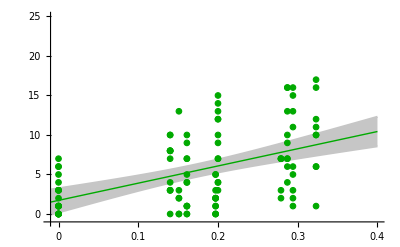

```mathematica
PhyloExp1=Plot[{lmPhyloExp5Days[x],bands90PhyloExp5Days[x]},{x,-0.01,0.4},PlotStyle-> {Directive[Darker[Green],Thick],Lighter[Lighter[Gray]]},Filling->{2->{{1},Lighter[Lighter[Gray]]}},PlotRange-> {{-0.01,0.4},{-1,25}},Ticks->fuk[{{0,0.1,0.2,0.3,0.4},{0,5,10,15,20,25},"Arial",Plain,20,0.02}],TicksStyle->Thickness[0.004],AxesStyle->Thickness[0.004],AxesOrigin->{-0.01,-1}];

grN=Graphics[{EdgeForm[{Darker[Green]}],FaceForm[Darker[Green]],Disk[]}];
grG=Graphics[{EdgeForm[{Gray}],FaceForm[Darker[Green]],Disk[]}];
grB=Graphics[{EdgeForm[{Black}],FaceForm[Darker[Green]],Disk[]}];

PhyloExp2=ListPlot[PhyloExp5Days,PlotMarkers->{grN,Scaled[0.035]}];
Show[PhyloExp1,PhyloExp2]
```

```mathematica
SpearmanRankTest[PhyDiCorr5,expPo5,"TestDataTable"]
```

| Statistic | P-Value
Spearman Rank | 0.49334 | 5.8047×10^-8

```mathematica
PhyloContr5Days=Partition[Riffle[PhyDiCorr5,contrPo5],{2}];
```

```mathematica
lmPhyloContr5Days=LinearModelFit[PhyloContr5Days,x,x]
```

FittedModel[5.60544-13.7345 x]

```mathematica
bands90PhyloContr5Days[x_]=lmPhyloContr5Days["MeanPredictionBands",ConfidenceLevel->.95];
```

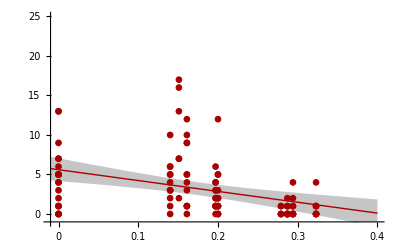

```mathematica
ConPhyl1=Plot[{lmPhyloContr5Days[x],bands90PhyloContr5Days[x]},{x,-0.01,0.4},PlotStyle-> {Directive[Darker[Red],Thick],Lighter[Lighter[Gray]]},Filling->{2->{{1},Lighter[Lighter[Gray]]}},PlotRange-> {{-0.01,0.4},{-1,25}},Ticks->fuk[{{0,0.1,0.2,0.3,0.4},{0,5,10,15,20,25},"Arial",Plain,20,0.02}],TicksStyle->Thickness[0.004],AxesStyle->Thickness[0.004],AxesOrigin->{-0.01,-1}];

rdN=Graphics[{EdgeForm[{Darker[Red]}],FaceForm[Darker[Red]],Disk[]}];
rdG=Graphics[{EdgeForm[{Gray}],FaceForm[Darker[Red]],Disk[]}];
rdB=Graphics[{EdgeForm[{Black}],FaceForm[Darker[Red]],Disk[]}];

ConPhyl2=ListPlot[PhyloContr5Days,PlotMarkers->{rdN,Scaled[0.035]}];
Show[ConPhyl1,ConPhyl2]
```

```mathematica
SpearmanRankTest[PhyDiCorr5,contrPo5,"TestDataTable"]
```

| Statistic | P-Value
Spearman Rank | -0.513351 | 1.3381×10^-8

```mathematica
(*Phylogeny and Intersection between Niches - Niche Overlap*)
```

```mathematica
Intersect5=#[[3]]&/@gk5
```

{15,1,21,10,1,0,1,0,15,1,21,9,12,1,20,12,14,15,7,14,1,1,0,1,17,19,9,21,7,9,8,11,17,1,17,14,21,1,21,18,9,0,9,11,23,1,22,24,12,4,16,13,17,12,4,17,15,21,6,2,8,11,11,12,4,18,19,28,13,1,13,11,4,0,4,4,18,1,18,16,17,1,17,18,25,1,24,25,11,4,15,11,15,0,1,1,0,1,13,4,19,18,23,6,2,8,10,12}

```mathematica
PhyloInter5Days=Partition[Riffle[PhyDiCorr5,Intersect5],{2}];
```

```mathematica
lmPhyloInter5Days=LinearModelFit[PhyloInter5Days,x,x]
```

FittedModel[17.7231-40.1901 x]

```mathematica
bands90PhyloInter5Days[x_]=lmPhyloInter5Days["MeanPredictionBands",ConfidenceLevel->.95];
```

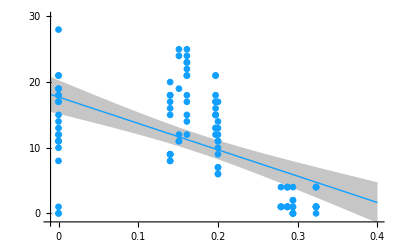

```mathematica
InterPhylo1=Plot[{lmPhyloInter5Days[x],bands90PhyloInter5Days[x]},{x,-0.01,0.4},PlotStyle-> {Directive[RGBColor[18/(255),160/(255),255/(255)],Thick],Lighter[Lighter[Gray]]},Filling->{2->{{1},Lighter[Lighter[Gray]]}},PlotRange-> {{-0.01,0.4},{-1.3,30}},Ticks->fuk[{{0,0.1,0.2,0.3,0.4},{0,5,10,15,20,25,30},"Arial",Plain,20,0.02}],TicksStyle->Thickness[0.004],AxesStyle->Thickness[0.004],AxesOrigin->{-0.01,-1.3}];

blN=Graphics[{EdgeForm[{RGBColor[18/(255),160/(255),255/(255)]}],FaceForm[RGBColor[18/(255),160/(255),255/(255)]],Disk[]}];
blG=Graphics[{EdgeForm[{Gray}],FaceForm[RGBColor[18/(255),160/(255),255/(255)]],Disk[]}];
blB=Graphics[{EdgeForm[{Black}],FaceForm[RGBColor[18/(255),160/(255),255/(255)]],Disk[]}];


InterPhylo2=ListPlot[PhyloInter5Days,PlotMarkers->{blN,Scaled[0.035]}];
Show[InterPhylo1,InterPhylo2]
```

```mathematica
wi5={1,6,11,16,17,26,31,33,39,44,49,56,62,68,69,74,79,84,89,95,101,107};
```

```mathematica
be5=Complement[Range[108],wi5];
```

```mathematica
expPo5=#[[7]]&/@gk5
```

{1,1,1,12,17,1,16,16,2,7,0,10,15,2,10,0,2,2,14,10,6,16,6,3,0,0,7,5,7,8,4,13,3,6,2,4,0,10,0,4,9,15,8,3,4,7,7,0,1,10,0,3,0,3,9,0,8,1,10,11,3,3,2,9,2,7,3,1,6,12,5,12,10,6,7,3,2,6,0,0,4,13,8,0,0,7,1,2,7,11,1,7,4,16,3,4,5,7,5,13,1,3,1,13,1,3,5,0}

```mathematica
contrPo5=#[[6]]&/@gk5
```

{1,1,3,0,0,0,0,0,1,0,5,2,2,1,3,7,0,1,0,0,1,0,0,0,2,4,3,5,3,4,5,2,4,0,3,12,6,0,9,10,2,0,1,5,4,1,1,16,2,4,4,5,12,1,2,5,5,9,1,1,0,7,7,1,1,3,13,13,1,0,2,1,0,0,1,4,4,0,6,6,5,0,6,13,5,0,10,17,0,1,1,1,1,0,1,0,0,0,0,1,3,5,9,0,2,3,5,7}

```mathematica
ExpansionWithin5=expPo5[[#]]&/@wi5
```

{1,1,0,0,2,0,4,3,0,3,1,0,3,1,6,6,0,0,7,3,1,5}

```mathematica
ExpansionBetween5=expPo5[[#]]&/@be5
```

{1,1,12,17,16,16,2,7,10,15,2,10,2,14,10,6,16,6,3,0,7,5,7,8,13,6,2,4,0,10,4,9,15,8,4,7,7,0,10,0,3,0,3,9,8,1,10,11,3,2,9,2,7,3,12,5,12,10,7,3,2,6,0,4,13,8,0,7,1,2,11,1,7,4,16,4,5,7,5,13,3,1,13,1,3,0}

```mathematica
ℋE=MannWhitneyTest[{ExpansionWithin5,ExpansionBetween5},0,"HypothesisTestData"];
ℋE["TestDataTable"]
```

| Statistic | P-Value
Mann-Whitney | 421.5 | 0.0000598989

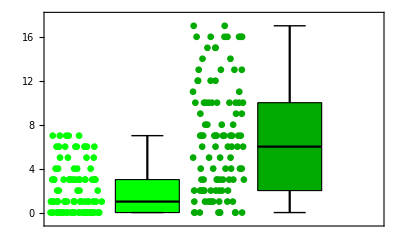

```mathematica
A1=BoxWhiskerChart[{ExpansionWithin5,ExpansionBetween5},{{"MedianMarker",1,Thickness[0.004]},{"Whiskers",Thickness[0.004]},{"Fences", Thick}},ChartBaseStyle->EdgeForm[Black],ChartStyle->{Thick,{Green,Darker[Green]}},Frame-> True,FrameTicks-> {None,{5,10,20},None,None}];

wq2:=RandomReal[{-0.18,0.18}]
jjA1=Table[0.5+wq2,Length[#[[5]]&/@gk5]];
jjA2=Table[1.5+wq2,Length[#[[7]]&/@gk5]];

grNBri=Graphics[{EdgeForm[{Green}],FaceForm[Green],Disk[]}];

A2=ListPlot[Partition[Riffle[jjA1,ExpansionWithin5],{2}],PlotMarkers->{grNBri,Scaled[0.035]},PlotStyle-> Black,PlotRange-> {{0,4},{0,25}}];
A3=ListPlot[Partition[Riffle[jjA2,ExpansionBetween5],{2}],PlotMarkers->{grN,Scaled[0.035]},PlotStyle-> Black,PlotRange-> {{0,4},{0,25}}];

Show[A1,A2,A3]
```

```mathematica
expPo5=#[[7]]&/@gk5
```

{1,1,1,12,17,1,16,16,2,7,0,10,15,2,10,0,2,2,14,10,6,16,6,3,0,0,7,5,7,8,4,13,3,6,2,4,0,10,0,4,9,15,8,3,4,7,7,0,1,10,0,3,0,3,9,0,8,1,10,11,3,3,2,9,2,7,3,1,6,12,5,12,10,6,7,3,2,6,0,0,4,13,8,0,0,7,1,2,7,11,1,7,4,16,3,4,5,7,5,13,1,3,1,13,1,3,5,0}

```mathematica
contrPo5=#[[6]]&/@gk5
```

{1,1,3,0,0,0,0,0,1,0,5,2,2,1,3,7,0,1,0,0,1,0,0,0,2,4,3,5,3,4,5,2,4,0,3,12,6,0,9,10,2,0,1,5,4,1,1,16,2,4,4,5,12,1,2,5,5,9,1,1,0,7,7,1,1,3,13,13,1,0,2,1,0,0,1,4,4,0,6,6,5,0,6,13,5,0,10,17,0,1,1,1,1,0,1,0,0,0,0,1,3,5,9,0,2,3,5,7}

```mathematica
ContractionWithin5=contrPo5[[#]]&/@wi5
```

{1,0,5,7,0,4,5,4,9,5,2,5,7,13,1,0,6,13,0,1,3,5}

```mathematica
ContractionBetween5=contrPo5[[#]]&/@be5
```

{1,3,0,0,0,0,1,0,2,2,1,3,1,0,0,1,0,0,0,2,3,5,3,4,2,0,3,12,6,0,10,2,0,1,4,1,1,16,4,4,5,12,1,2,5,9,1,1,0,7,1,1,3,13,0,2,1,0,1,4,4,0,6,5,0,6,5,0,10,17,1,1,1,1,0,0,0,0,0,1,5,9,0,2,3,7}

```mathematica
ℋC=MannWhitneyTest[{ContractionWithin5,ContractionBetween5},0,"HypothesisTestData"];
ℋC["TestDataTable"]
```

| Statistic | P-Value
Mann-Whitney | 1202. | 0.0467876

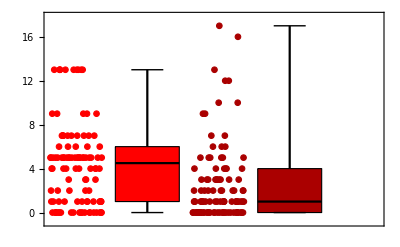

```mathematica
B1=BoxWhiskerChart[{ContractionWithin5,ContractionBetween5},{{"MedianMarker",1,Thickness[0.004]},{"Whiskers",Thickness[0.004]},{"Fences", Thick}},ChartBaseStyle->EdgeForm[Black],ChartStyle->{Thick,{Red,Darker[Red]}},Frame-> True,FrameTicks-> {None,{5,10,20},None,None}];

wq2:=RandomReal[{-0.18,0.18}]
jjB1=Table[0.5+wq2,Length[#[[5]]&/@gk5]];
jjB2=Table[1.5+wq2,Length[#[[7]]&/@gk5]];

rdNBri=Graphics[{EdgeForm[{Red}],FaceForm[Red],Disk[]}];

B2=ListPlot[Partition[Riffle[jjB1,ContractionWithin5],{2}],PlotMarkers->{rdNBri,Scaled[0.035]},PlotStyle-> Black,PlotRange-> {{0,4},{0,25}}];
B3=ListPlot[Partition[Riffle[jjB2,ContractionBetween5],{2}],PlotMarkers->{rdN,Scaled[0.035]},PlotStyle-> Black,PlotRange-> {{0,4},{0,25}}];

Show[B1,B2,B3]
```

## The role of Species and Auxotrophy type on Niche Expansion and Contraction

#### Species

```mathematica
(*Expansion*)
```

```mathematica
(*Expansion*)
```

```mathematica
expan=#[[7]]&/@gk5KJaccK
```

{1,1,1,12,17,1,16,16,2,7,0,10,15,2,10,0,2,2,14,10,6,16,6,3,0,0,7,5,7,8,4,13,3,6,2,4,0,10,0,4,9,15,8,3,4,7,7,0,1,10,0,3,0,3,9,0,8,1,10,11,3,3,2,9,2,7,3,1,6,12,5,12,10,6,7,3,2,6,0,0,4,13,8,0,0,7,1,2,7,11,1,7,4,16,3,4,5,7,5,13,1,3,1,13,1,3,5,0}

```mathematica
(*Contraction*)
```

```mathematica
contrac=#[[6]]&/@gk5KJaccK
```

{1,1,3,0,0,0,0,0,1,0,5,2,2,1,3,7,0,1,0,0,1,0,0,0,2,4,3,5,3,4,5,2,4,0,3,12,6,0,9,10,2,0,1,5,4,1,1,16,2,4,4,5,12,1,2,5,5,9,1,1,0,7,7,1,1,3,13,13,1,0,2,1,0,0,1,4,4,0,6,6,5,0,6,13,5,0,10,17,0,1,1,1,1,0,1,0,0,0,0,1,3,5,9,0,2,3,5,7}

```mathematica
(*Super-Expansion*)
```

```mathematica
supexp=#[[8]]&/@gk5KJaccK
```

{0,0,0,0,5,1,1,8,0,1,0,0,1,0,2,0,1,0,5,1,1,3,2,0,0,0,0,0,1,1,2,0,0,0,0,0,0,1,0,0,0,7,1,0,0,0,0,0,0,3,0,0,0,0,0,0,1,0,3,3,1,1,0,1,0,1,0,0,1,3,1,1,1,5,1,0,0,1,0,0,0,2,1,0,0,0,0,0,3,2,1,2,0,2,2,1,1,0,2,0,0,1,0,3,0,0,1,0}

```mathematica
jko={#[[1]],#[[2]]}&/@jop5
```

{{ABR5,ABH5},{ABR5,BSH5},{ABR5,ECH5},{ABR5,SOH5},{BSR5,ABH5},{BSR5,BSH5},{BSR5,ECH5},{BSR5,SOH5},{ECR5,ABH5},{ECR5,BSH5},{ECR5,ECH5},{ECR5,SOH5},{SOR5,ABH5},{SOR5,BSH5},{SOR5,ECH5},{SOR5,SOH5},{ABH5,ABW5},{ABH5,ECW5},{ABH5,SOW5},{ABH5,PFW5},{BSH5,ABW5},{BSH5,ECW5},{BSH5,SOW5},{BSH5,PFW5},{ECH5,ABW5},{ECH5,ECW5},{ECH5,SOW5},{ECH5,PFW5},{SOH5,ABW5},{SOH5,ECW5},{SOH5,SOW5},{SOH5,PFW5},{ABW5,ABR5},{ABW5,BSR5},{ABW5,ECR5},{ABW5,SOR5},{ECW5,ABR5},{ECW5,BSR5},{ECW5,ECR5},{ECW5,SOR5},{SOW5,ABR5},{SOW5,BSR5},{SOW5,ECR5},{SOW5,SOR5},{PFW5,ABR5},{PFW5,BSR5},{PFW5,ECR5},{PFW5,SOR5},{ABW5,ABL5},{ABW5,BSL5},{ABW5,ECL5},{ABW5,SOL5},{ABW5,PFL5},{ECW5,ABL5},{ECW5,BSL5},{ECW5,ECL5},{ECW5,SOL5},{ECW5,PFL5},{SOW5,ABL5},{SOW5,BSL5},{SOW5,ECL5},{SOW5,SOL5},{SOW5,PFL5},{PFW5,ABL5},{PFW5,BSL5},{PFW5,ECL5},{PFW5,SOL5},{PFW5,PFL5},{ABL5,ABR5},{ABL5,BSR5},{ABL5,ECR5},{ABL5,SOR5},{BSL5,ABR5},{BSL5,BSR5},{BSL5,ECR5},{BSL5,SOR5},{ECL5,ABR5},{ECL5,BSR5},{ECL5,ECR5},{ECL5,SOR5},{SOL5,ABR5},{SOL5,BSR5},{SOL5,ECR5},{SOL5,SOR5},{PFL5,ABR5},{PFL5,BSR5},{PFL5,ECR5},{PFL5,SOR5},{ABH5,ABL5},{ABH5,BSL5},{ABH5,ECL5},{ABH5,SOL5},{ABH5,PFL5},{BSH5,ABL5},{BSH5,BSL5},{BSH5,ECL5},{BSH5,SOL5},{BSH5,PFL5},{ECH5,ABL5},{ECH5,BSL5},{ECH5,ECL5},{ECH5,SOL5},{ECH5,PFL5},{SOH5,ABL5},{SOH5,BSL5},{SOH5,ECL5},{SOH5,SOL5},{SOH5,PFL5}}

```mathematica
hkk={StringTake[jko[[#]][[1]],1],StringTake[jko[[#]][[2]],1]}&/@Range[Length[jko]]
```

{{A,A},{A,B},{A,E},{A,S},{B,A},{B,B},{B,E},{B,S},{E,A},{E,B},{E,E},{E,S},{S,A},{S,B},{S,E},{S,S},{A,A},{A,E},{A,S},{A,P},{B,A},{B,E},{B,S},{B,P},{E,A},{E,E},{E,S},{E,P},{S,A},{S,E},{S,S},{S,P},{A,A},{A,B},{A,E},{A,S},{E,A},{E,B},{E,E},{E,S},{S,A},{S,B},{S,E},{S,S},{P,A},{P,B},{P,E},{P,S},{A,A},{A,B},{A,E},{A,S},{A,P},{E,A},{E,B},{E,E},{E,S},{E,P},{S,A},{S,B},{S,E},{S,S},{S,P},{P,A},{P,B},{P,E},{P,S},{P,P},{A,A},{A,B},{A,E},{A,S},{B,A},{B,B},{B,E},{B,S},{E,A},{E,B},{E,E},{E,S},{S,A},{S,B},{S,E},{S,S},{P,A},{P,B},{P,E},{P,S},{A,A},{A,B},{A,E},{A,S},{A,P},{B,A},{B,B},{B,E},{B,S},{B,P},{E,A},{E,B},{E,E},{E,S},{E,P},{S,A},{S,B},{S,E},{S,S},{S,P}}

```mathematica
PosA=MemberQ[hkk[[#]],"A"]&/@Range[Length[hkk]]
```

{True,True,True,True,True,False,False,False,True,False,False,False,True,False,False,False,True,True,True,True,True,False,False,False,True,False,False,False,True,False,False,False,True,True,True,True,True,False,False,False,True,False,False,False,True,False,False,False,True,True,True,True,True,True,False,False,False,False,True,False,False,False,False,True,False,False,False,False,True,True,True,True,True,False,False,False,True,False,False,False,True,False,False,False,True,False,False,False,True,True,True,True,True,True,False,False,False,False,True,False,False,False,False,True,False,False,False,False}

```mathematica
PosB=MemberQ[hkk[[#]],"B"]&/@Range[Length[hkk]];
```

```mathematica
PosE=MemberQ[hkk[[#]],"E"]&/@Range[Length[hkk]];
```

```mathematica
PosS=MemberQ[hkk[[#]],"S"]&/@Range[Length[hkk]];
```

```mathematica
PosP=MemberQ[hkk[[#]],"P"]&/@Range[Length[hkk]];
```

```mathematica
(***)
```

```mathematica
(***)
```

```mathematica
Count[PosA,True]/Length[PosA]//N
```

0.416667

```mathematica
Count[PosB,True]/Length[PosA]//N
```

0.324074

```mathematica
Count[PosE,True]/Length[PosA]//N
```

0.416667

```mathematica
Count[PosS,True]/Length[PosA]//N
```

0.416667

```mathematica
Count[PosP,True]/Length[PosA]//N
```

0.222222

```mathematica
jooA=PosA/.{True-> 1,False-> 0}
```

{1,1,1,1,1,0,0,0,1,0,0,0,1,0,0,0,1,1,1,1,1,0,0,0,1,0,0,0,1,0,0,0,1,1,1,1,1,0,0,0,1,0,0,0,1,0,0,0,1,1,1,1,1,1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1,1,1,1,1,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,1,1,1,1,1,1,0,0,0,0,1,0,0,0,0,1,0,0,0,0}

```mathematica
jooB=PosB/.{True-> 1,False-> 0};
jooE=PosE/.{True-> 1,False-> 0};
jooS=PosS/.{True-> 1,False-> 0};
jooP=PosP/.{True-> 1,False-> 0};
```

```mathematica
(*Observed*)
```

```mathematica
Total[expan jooA]
```

269

```mathematica
Total[expan jooB]
```

285

```mathematica
Total[expan jooE]
```

206

```mathematica
Total[expan jooS]
```

289

```mathematica
Total[expan jooP]
```

96

```mathematica
N[{Total[expan jooA],Total[expan jooB],Total[expan jooE],Total[expan jooS],Total[expan jooP]}/(Total[expan jooA]+Total[expan jooB]+Total[expan jooE]+Total[expan jooS]+Total[expan jooP])]
```

{0.234934,0.248908,0.179913,0.252402,0.0838428}

```mathematica
(** A: 269  *)
```

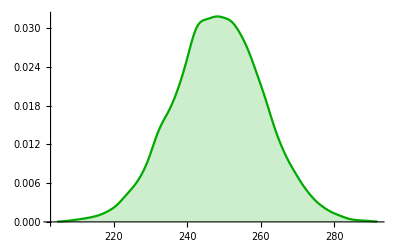

```mathematica
PermuExpanA=Table[(
hoz=Tally[Sort[RandomInteger[{1,Length[expan]},Total[expan]]]];
guq=ConstantArray[0,Length[expan]];
hoz1=#[[1]]-> #[[2]]&/@hoz;
expanSimul=ReplacePart[guq,hoz1];
Total[expanSimul jooA]),{10000}];

SmoothHistogram[PermuExpanA,PlotStyle-> Darker[Green],Filling->Axis]
```

```mathematica
(#≥ 269)&/@PermuExpanA
```

{False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,True,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,True,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True}

```mathematica
Count[(#≥ 269)&/@PermuExpanA,True]
```

6

```mathematica
N[Count[(#≥ 269)&/@PermuExpanA,True]/Length[PermuExpanA]]
```

0.0491

```mathematica
(** B: 285  *)
```

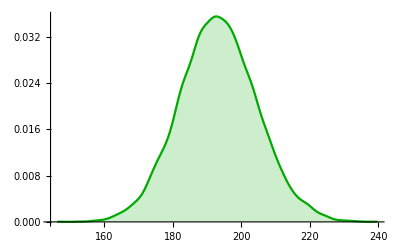

```mathematica
PermuExpanB=Table[(
hoz=Tally[Sort[RandomInteger[{1,Length[expan]},Total[expan]]]];
guq=ConstantArray[0,Length[expan]];
hoz1=#[[1]]-> #[[2]]&/@hoz;
expanSimul=ReplacePart[guq,hoz1];
Total[expanSimul jooB]),{10000}];

SmoothHistogram[PermuExpanB,PlotStyle-> Darker[Green],Filling->Axis]
```

```mathematica
N[Count[(#≥  285)&/@PermuExpanB,True]/Length[PermuExpanB]]
```

0.

```mathematica
Mean[PermuExpanB]//N
```

193.048

```mathematica
(** E: 206  *)
```

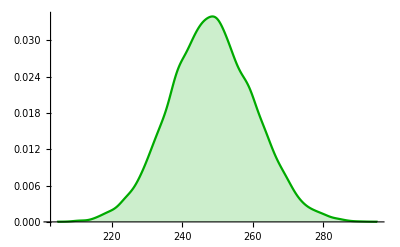

```mathematica
PermuExpanE=Table[(
hoz=Tally[Sort[RandomInteger[{1,Length[expan]},Total[expan]]]];
guq=ConstantArray[0,Length[expan]];
hoz1=#[[1]]-> #[[2]]&/@hoz;
expanSimul=ReplacePart[guq,hoz1];
Total[expanSimul jooE]),{10000}];

SmoothHistogram[PermuExpanE,PlotStyle-> Darker[Green],Filling->Axis]
```

```mathematica
N[Count[(#≤   206)&/@PermuExpanE,True]/Length[PermuExpanE]]
```

0.0003

```mathematica
Mean[PermuExpanE]//N
```

248.118

```mathematica
(** S: 289  *)
```

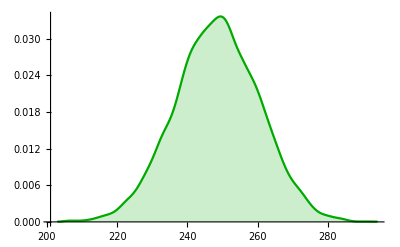

```mathematica
PermuExpanS=Table[(
hoz=Tally[Sort[RandomInteger[{1,Length[expan]},Total[expan]]]];
guq=ConstantArray[0,Length[expan]];
hoz1=#[[1]]-> #[[2]]&/@hoz;
expanSimul=ReplacePart[guq,hoz1];
Total[expanSimul jooS]),{10000}];

SmoothHistogram[PermuExpanS,PlotStyle-> Darker[Green],Filling->Axis]
```

```mathematica
N[Count[(#≥  289)&/@PermuExpanS,True]/Length[PermuExpanS]]
```

0.0007

```mathematica
(** P: 96  *)
```

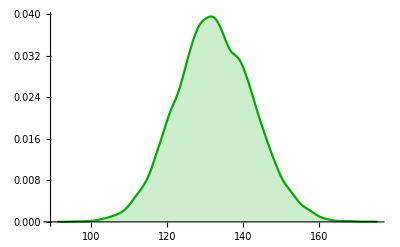

```mathematica
PermuExpanP=Table[(
hoz=Tally[Sort[RandomInteger[{1,Length[expan]},Total[expan]]]];
guq=ConstantArray[0,Length[expan]];
hoz1=#[[1]]-> #[[2]]&/@hoz;
expanSimul=ReplacePart[guq,hoz1];
Total[expanSimul jooP]),{10000}];

SmoothHistogram[PermuExpanP,PlotStyle-> Darker[Green],Filling->Axis]
```

```mathematica
N[Count[(#≤   96)&/@PermuExpanP,True]/Length[PermuExpanP]]
```

0.0001

```mathematica
(****)
```

```mathematica
Spec3={{Around[248,293-248],200},{Around[193,239-193],200},{Around[248,295-248],200},{Around[132,174-132],200},{Around[249,293-249],200}};
```

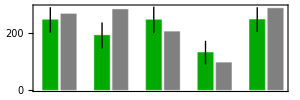

```mathematica
BarChart[Spec3,ChartStyle-> {Darker[Green],Gray},PlotTheme->"Web",BarSpacing->{0.2,1.2},ImageSize->300,AspectRatio->1/3]
```

```mathematica
(*Contraction*)
```

```mathematica
(** A: 98  *)
```

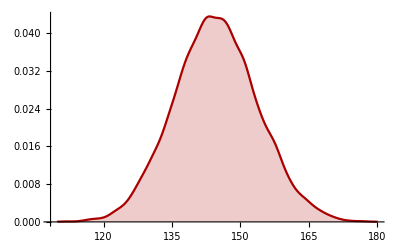

```mathematica
PermuContracA=Table[(
hoz=Tally[Sort[RandomInteger[{1,Length[contrac]},Total[contrac]]]];
guq=ConstantArray[0,Length[contrac]];
hoz1=#[[1]]-> #[[2]]&/@hoz;
contracSimul=ReplacePart[guq,hoz1];
Total[contracSimul jooA]),{10000}];

SmoothHistogram[PermuContracA,PlotStyle-> Darker[Red],Filling->Axis]
```

```mathematica
(#≤  98)&/@PermuContracA
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
Count[(#≤  98)&/@PermuContracA,True]
```

0

```mathematica
(** B: 22  *)
```

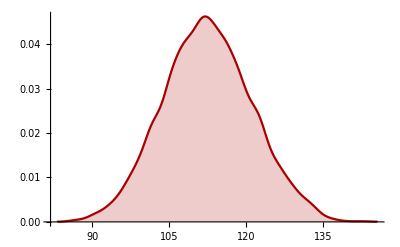

```mathematica
PermuContracB=Table[(
hoz=Tally[Sort[RandomInteger[{1,Length[contrac]},Total[contrac]]]];
guq=ConstantArray[0,Length[contrac]];
hoz1=#[[1]]-> #[[2]]&/@hoz;
contracSimul=ReplacePart[guq,hoz1];
Total[contracSimul jooB]),{10000}];

SmoothHistogram[PermuContracB,PlotStyle-> Darker[Red],Filling->Axis]
```

```mathematica
N[Count[(#≤   22)&/@PermuContracB,True]/Length[PermuContracB]]
```

0.

```mathematica
(** E: 149  *)
```

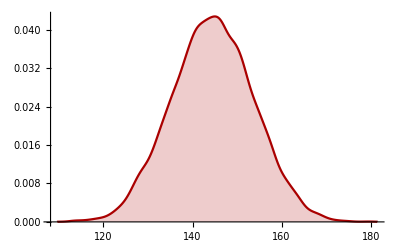

```mathematica
PermuContracE=Table[(
hoz=Tally[Sort[RandomInteger[{1,Length[contrac]},Total[contrac]]]];
guq=ConstantArray[0,Length[contrac]];
hoz1=#[[1]]-> #[[2]]&/@hoz;
contracSimul=ReplacePart[guq,hoz1];
Total[contracSimul jooE]),{10000}];

SmoothHistogram[PermuContracE,PlotStyle-> Darker[Red],Filling->Axis]
```

```mathematica
N[Count[(#≤   149)&/@PermuContracE,True]/Length[PermuContracE]]
N[Count[(#≥    149)&/@PermuContracE,True]/Length[PermuContracE]]
```

0.7111

0.3266

```mathematica
(** S: 192  *)
```

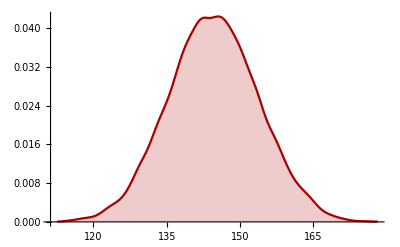

```mathematica
PermuContracS=Table[(
hoz=Tally[Sort[RandomInteger[{1,Length[contrac]},Total[contrac]]]];
guq=ConstantArray[0,Length[contrac]];
hoz1=#[[1]]-> #[[2]]&/@hoz;
contracSimul=ReplacePart[guq,hoz1];
Total[contracSimul jooS]),{10000}];

SmoothHistogram[PermuContracS,PlotStyle-> Darker[Red],Filling->Axis]
```

```mathematica
N[Count[(#≥  192)&/@PermuContracS,True]/Length[PermuContracS]]
```

0.

```mathematica
(** P: 137  *)
```

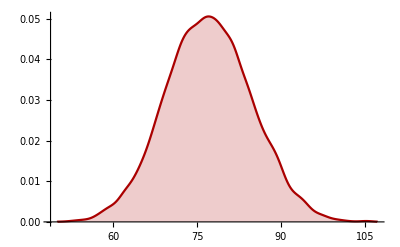

```mathematica
PermuContracP=Table[(
hoz=Tally[Sort[RandomInteger[{1,Length[contrac]},Total[contrac]]]];
guq=ConstantArray[0,Length[contrac]];
hoz1=#[[1]]-> #[[2]]&/@hoz;
contracSimul=ReplacePart[guq,hoz1];
Total[contracSimul jooP]),{10000}];

SmoothHistogram[PermuContracP,PlotStyle-> Darker[Red],Filling->Axis]
```

```mathematica
N[Count[(#≥    137)&/@PermuContracP,True]/Length[PermuContracP]]
```

0.

```mathematica
Spec3Con={{Around[145,181-145],98},{Around[112,147-112],22},{Around[144,187-144],149},{Around[77,105-77],137},{Around[145,183-145],192}};
```

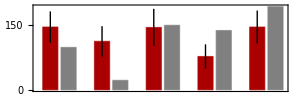

```mathematica
BarChart[Spec3Con,ChartStyle-> {Darker[Red],Gray},PlotTheme->"Web",BarSpacing->{0.2,1.2},ImageSize->300,AspectRatio->1/3]
```

```mathematica
(*Double Expansion*)
```

```mathematica
(** A: 44  *)
```

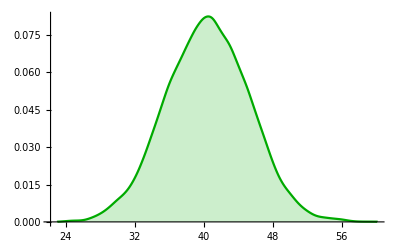

```mathematica
PermuSuperExpanA=Table[(
hoz=Tally[Sort[RandomInteger[{1,Length[supexp]},Total[supexp]]]];
guq=ConstantArray[0,Length[supexp]];
hoz1=#[[1]]-> #[[2]]&/@hoz;
SuperexpanSimul=ReplacePart[guq,hoz1];
Total[SuperexpanSimul jooA]),{10000}];

SmoothHistogram[PermuSuperExpanA,PlotStyle-> Darker[Green],Filling->Axis]
```

```mathematica
(#≥ 44)&/@PermuSuperExpanA
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,True,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,True,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,True,False,False,True,False,False,True,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,True,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,True,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,True,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,True,False,False,True,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
Count[(#≥ 44)&/@PermuSuperExpanA,True]
```

6

```mathematica
N[Count[(#≥ 44)&/@PermuSuperExpanA,True]/Length[PermuSuperExpanA]]
N[Count[(#≤  44)&/@PermuSuperExpanA,True]/Length[PermuSuperExpanA]]
```

0.259

0.8029

```mathematica
(** B: 57  *)
```

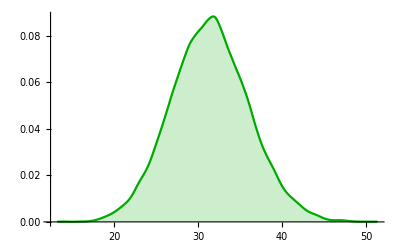

```mathematica
PermuSuperExpanB=Table[(
hoz=Tally[Sort[RandomInteger[{1,Length[supexp]},Total[supexp]]]];
guq=ConstantArray[0,Length[supexp]];
hoz1=#[[1]]-> #[[2]]&/@hoz;
SuperexpanSimul=ReplacePart[guq,hoz1];
Total[SuperexpanSimul jooB]),{10000}];

SmoothHistogram[PermuSuperExpanB,PlotStyle-> Darker[Green],Filling->Axis]
```

```mathematica
N[Count[(#≥  57)&/@PermuSuperExpanB,True]/Length[PermuSuperExpanB]]
```

0.

```mathematica
Mean[PermuSuperExpanB]//N
```

31.481

```mathematica
(** E: 22  *)
```

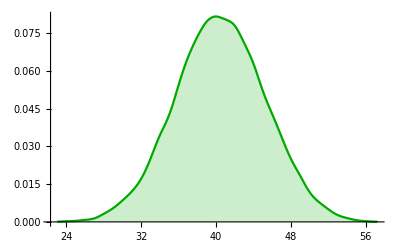

```mathematica
PermuSuperExpanE=Table[(
hoz=Tally[Sort[RandomInteger[{1,Length[supexp]},Total[supexp]]]];
guq=ConstantArray[0,Length[supexp]];
hoz1=#[[1]]-> #[[2]]&/@hoz;
SuperexpanSimul=ReplacePart[guq,hoz1];
Total[SuperexpanSimul jooE]),{10000}];

SmoothHistogram[PermuSuperExpanE,PlotStyle-> Darker[Green],Filling->Axis]
```

```mathematica
N[Count[(#≤  22)&/@PermuSuperExpanE,True]/Length[PermuSuperExpanE]]
```

0.

```mathematica
Mean[PermuSuperExpanE]//N
```

40.2534

```mathematica
(** S: 51  *)
```

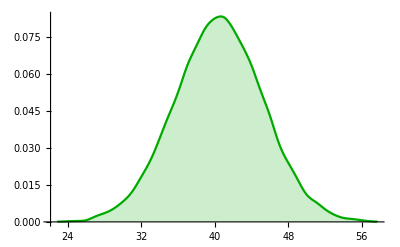

```mathematica
PermuSuperExpanS=Table[(
hoz=Tally[Sort[RandomInteger[{1,Length[supexp]},Total[supexp]]]];
guq=ConstantArray[0,Length[supexp]];
hoz1=#[[1]]-> #[[2]]&/@hoz;
SuperexpanSimul=ReplacePart[guq,hoz1];
Total[SuperexpanSimul jooS]),{10000}];

SmoothHistogram[PermuSuperExpanS,PlotStyle-> Darker[Green],Filling->Axis]
```

```mathematica
N[Count[(#≥  51)&/@PermuSuperExpanS,True]/Length[PermuSuperExpanS]]
```

0.0206

```mathematica
Mean[PermuSuperExpanS]//N
```

40.3703

```mathematica
(** P: 3  *)
```

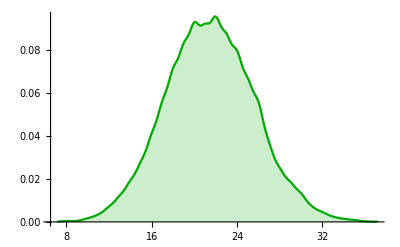

```mathematica
PermuSuperExpanP=Table[(
hoz=Tally[Sort[RandomInteger[{1,Length[supexp]},Total[supexp]]]];
guq=ConstantArray[0,Length[supexp]];
hoz1=#[[1]]-> #[[2]]&/@hoz;
SuperexpanSimul=ReplacePart[guq,hoz1];
Total[SuperexpanSimul jooP]),{10000}];

SmoothHistogram[PermuSuperExpanP,PlotStyle-> Darker[Green],Filling->Axis]
```

```mathematica
N[Count[(#≤     3)&/@PermuSuperExpanP,True]/Length[PermuSuperExpanP]]
```

0.

```mathematica
N[Mean[PermuSuperExpanP]]
```

21.5339

```mathematica
Spec3NE={{Around[40,60-40],44},{Around[31,51-31],57},{Around[40,58-40],22},{Around[21,38-21],3},{Around[40,57-40],51}};
```

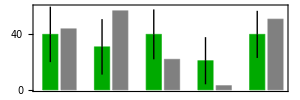

```mathematica
BarChart[Spec3NE,ChartStyle-> {Darker[Green],Gray},PlotTheme->"Web",BarSpacing->{0.2,1.2},ImageSize->300,AspectRatio->1/3]
```

#### Auxotrophy

```mathematica
hkkF={StringTake[jko[[#]][[1]],{3}],StringTake[jko[[#]][[2]],{3}]}&/@Range[Length[jko]]
```

{{R,H},{R,H},{R,H},{R,H},{R,H},{R,H},{R,H},{R,H},{R,H},{R,H},{R,H},{R,H},{R,H},{R,H},{R,H},{R,H},{H,W},{H,W},{H,W},{H,W},{H,W},{H,W},{H,W},{H,W},{H,W},{H,W},{H,W},{H,W},{H,W},{H,W},{H,W},{H,W},{W,R},{W,R},{W,R},{W,R},{W,R},{W,R},{W,R},{W,R},{W,R},{W,R},{W,R},{W,R},{W,R},{W,R},{W,R},{W,R},{W,L},{W,L},{W,L},{W,L},{W,L},{W,L},{W,L},{W,L},{W,L},{W,L},{W,L},{W,L},{W,L},{W,L},{W,L},{W,L},{W,L},{W,L},{W,L},{W,L},{L,R},{L,R},{L,R},{L,R},{L,R},{L,R},{L,R},{L,R},{L,R},{L,R},{L,R},{L,R},{L,R},{L,R},{L,R},{L,R},{L,R},{L,R},{L,R},{L,R},{H,L},{H,L},{H,L},{H,L},{H,L},{H,L},{H,L},{H,L},{H,L},{H,L},{H,L},{H,L},{H,L},{H,L},{H,L},{H,L},{H,L},{H,L},{H,L},{H,L}}

```mathematica
DeleteDuplicates[Flatten[hkkF]]
```

{R,H,W,L}

```mathematica
PosR=MemberQ[hkkF[[#]],"R"]&/@Range[Length[hkkF]]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
PosH=MemberQ[hkkF[[#]],"H"]&/@Range[Length[hkkF]];
```

```mathematica
PosW=MemberQ[hkkF[[#]],"W"]&/@Range[Length[hkkF]];
```

```mathematica
PosL=MemberQ[hkkF[[#]],"L"]&/@Range[Length[hkkF]];
```

```mathematica
(***)
```

```mathematica
Count[PosR,True]
```

52

```mathematica
Count[PosH,True]
```

52

```mathematica
Count[PosW,True]
```

52

```mathematica
Count[PosL,True]
```

60

```mathematica
Length[PosR]
```

108

```mathematica
(***)
```

```mathematica
Count[PosR,True]/Length[PosR]//N
```

0.481481

```mathematica
Count[PosH,True]/Length[PosH]//N
```

0.481481

```mathematica
Count[PosW,True]/Length[PosW]//N
```

0.481481

```mathematica
Count[PosL,True]/Length[PosL]//N
```

0.555556

```mathematica
jooR=PosR/.{True-> 1,False-> 0}
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
jooH=PosH/.{True-> 1,False-> 0};
jooW=PosW/.{True-> 1,False-> 0};
jooL=PosL/.{True-> 1,False-> 0};
```

```mathematica
(*Expansion*)
```

```mathematica
(** R: 297  *)
```

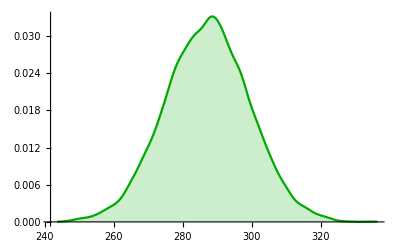

```mathematica
PermuExpanR=Table[(
hoz=Tally[Sort[RandomInteger[{1,Length[expan]},Total[expan]]]];
guq=ConstantArray[0,Length[expan]];
hoz1=#[[1]]-> #[[2]]&/@hoz;
expanSimul=ReplacePart[guq,hoz1];
Total[expanSimul jooR]),{10000}];

SmoothHistogram[PermuExpanR,PlotStyle-> Darker[Green],Filling->Axis]
```

```mathematica
(#≥ 297)&/@PermuExpanR
```

```mathematica
Count[(#≤  297)&/@PermuExpanR,True]
```

8062

```mathematica
(** H: 324  *)
```

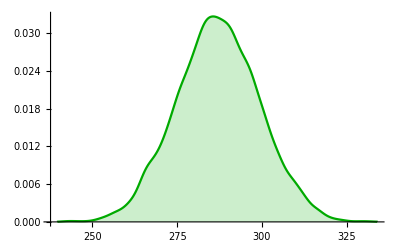

```mathematica
PermuExpanH=Table[(
hoz=Tally[Sort[RandomInteger[{1,Length[expan]},Total[expan]]]];
guq=ConstantArray[0,Length[expan]];
hoz1=#[[1]]-> #[[2]]&/@hoz;
expanSimul=ReplacePart[guq,hoz1];
Total[expanSimul jooH]),{10000}];

SmoothHistogram[PermuExpanH,PlotStyle-> Darker[Green],Filling->Axis]
```

```mathematica
N[Count[(#≥  324)&/@PermuExpanH,True]/Length[PermuExpanH]]
```

0.0013

```mathematica
Mean[PermuExpanH]//N
```

287.011

```mathematica
(** W: 271  *)
```

```mathematica
Floor[N[Mean[PermuExpanW]]]
```

286

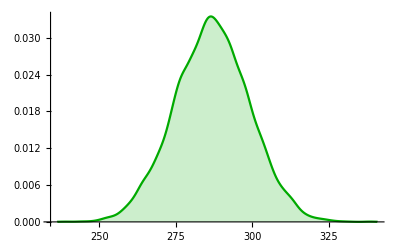

```mathematica
PermuExpanW=Table[(
hoz=Tally[Sort[RandomInteger[{1,Length[expan]},Total[expan]]]];
guq=ConstantArray[0,Length[expan]];
hoz1=#[[1]]-> #[[2]]&/@hoz;
expanSimul=ReplacePart[guq,hoz1];
Total[expanSimul jooW]),{10000}];

SmoothHistogram[PermuExpanW,PlotStyle-> Darker[Green],Filling->Axis]
```

```mathematica
N[Count[(#≤   271)&/@PermuExpanW,True]/Length[PermuExpanW]]
```

0.1038

```mathematica
Mean[PermuExpanW]//N
```

286.861

```mathematica
(** L: 300  *)
```

```mathematica
Floor[N[Mean[PermuExpanL]]]
```

330

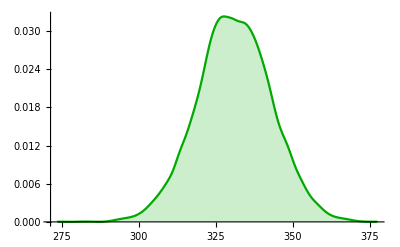

```mathematica
PermuExpanL=Table[(
hoz=Tally[Sort[RandomInteger[{1,Length[expan]},Total[expan]]]];
guq=ConstantArray[0,Length[expan]];
hoz1=#[[1]]-> #[[2]]&/@hoz;
expanSimul=ReplacePart[guq,hoz1];
Total[expanSimul jooL]),{10000}];

SmoothHistogram[PermuExpanL,PlotStyle-> Darker[Green],Filling->Axis]
```

```mathematica
N[Count[(#≤ 300)&/@PermuExpanL,True]/Length[PermuExpanL]]
```

0.0064

```mathematica
Spec3F={{Around[287,335-287],297},{Around[287,239-287],324},{Around[287,339-287],271},{Around[331,376-331],300}};
```

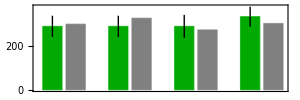

```mathematica
BarChart[Spec3F,ChartStyle-> {Darker[Green],Gray},PlotTheme->"Web",BarSpacing->{0.2,1.2},ImageSize->300,AspectRatio->1/3]
```

```mathematica
(*Contraction*)
```

```mathematica
(** R: 181  *)
```

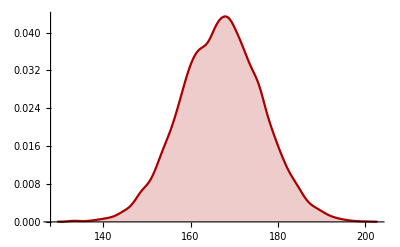

```mathematica
PermuContracR=Table[(
hoz=Tally[Sort[RandomInteger[{1,Length[contrac]},Total[contrac]]]];
guq=ConstantArray[0,Length[contrac]];
hoz1=#[[1]]-> #[[2]]&/@hoz;
contracSimul=ReplacePart[guq,hoz1];
Total[contracSimul jooR]),{10000}];

SmoothHistogram[PermuContracR,PlotStyle-> Darker[Red],Filling->Axis]
```

```mathematica
(#≥   181)&/@PermuContracR
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
Count[(#≥   181)&/@PermuContracR,True]
```

741

```mathematica
N[Count[(#≥   181)&/@PermuContracR,True]/Length[PermuContracR]]
```

0.0741

```mathematica
(** H: 96  *)
```

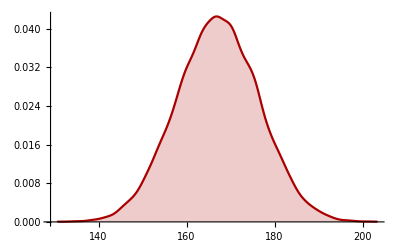

```mathematica
PermuContracH=Table[(
hoz=Tally[Sort[RandomInteger[{1,Length[contrac]},Total[contrac]]]];
guq=ConstantArray[0,Length[contrac]];
hoz1=#[[1]]-> #[[2]]&/@hoz;
contracSimul=ReplacePart[guq,hoz1];
Total[contracSimul jooH]),{10000}];

SmoothHistogram[PermuContracH,PlotStyle-> Darker[Red],Filling->Axis]
```

```mathematica
N[Count[(#≤96)&/@PermuContracH,True]/Length[PermuContracH]]
```

0.

```mathematica
(** W: 200  *)
```

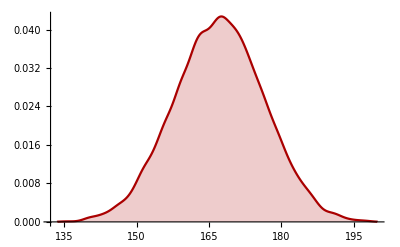

```mathematica
PermuContracW=Table[(
hoz=Tally[Sort[RandomInteger[{1,Length[contrac]},Total[contrac]]]];
guq=ConstantArray[0,Length[contrac]];
hoz1=#[[1]]-> #[[2]]&/@hoz;
contracSimul=ReplacePart[guq,hoz1];
Total[contracSimul jooW]),{10000}];

SmoothHistogram[PermuContracW,PlotStyle-> Darker[Red],Filling->Axis]
```

```mathematica
N[Count[(#≥    200)&/@PermuContracW,True]/Length[PermuContracW]]
```

0.

```mathematica
(** L: 217  *)
```

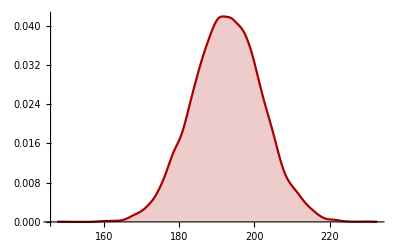

```mathematica
PermuContracL=Table[(
hoz=Tally[Sort[RandomInteger[{1,Length[contrac]},Total[contrac]]]];
guq=ConstantArray[0,Length[contrac]];
hoz1=#[[1]]-> #[[2]]&/@hoz;
contracSimul=ReplacePart[guq,hoz1];
Total[contracSimul jooL]),{10000}];

SmoothHistogram[PermuContracL,PlotStyle-> Darker[Red],Filling->Axis]
```

```mathematica
N[Count[(#≥  217)&/@PermuContracL,True]/Length[PermuContracL]]
```

0.0043

```mathematica
Spec3ConF={{Around[167,202-167],181},{Around[167,202-167],96},{Around[167,198-167],200},{Around[193,231-193],217}};
```

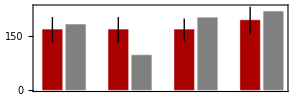

```mathematica
BarChart[Spec3ConF,ChartStyle-> {Darker[Red],Gray},PlotTheme->"Web",BarSpacing->{0.2,1.2},ImageSize->300,AspectRatio->1/3]
```

```mathematica
(*Double Expansion*)
```

```mathematica
(** R: 45  *)
```

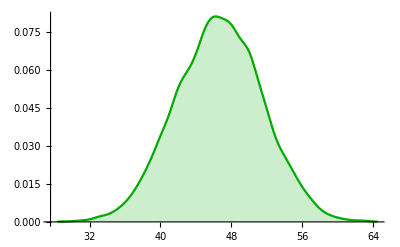

```mathematica
PermuSuperExpanR=Table[(
hoz=Tally[Sort[RandomInteger[{1,Length[supexp]},Total[supexp]]]];
guq=ConstantArray[0,Length[supexp]];
hoz1=#[[1]]-> #[[2]]&/@hoz;
SuperexpanSimul=ReplacePart[guq,hoz1];
Total[SuperexpanSimul jooR]),{10000}];

SmoothHistogram[PermuSuperExpanR,PlotStyle-> Darker[Green],Filling->Axis]
```

```mathematica
(#≥ 45)&/@PermuSuperExpanR
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,True,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,True,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,True,False,False,True,False,False,True,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,True,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,True,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,True,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,True,False,False,True,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
Count[(#≥ 45)&/@PermuSuperExpanR,True]
```

7373

```mathematica
N[Count[(#≥ 45)&/@PermuSuperExpanR,True]/Length[PermuSuperExpanR]]
N[Count[(#≤  45)&/@PermuSuperExpanR,True]/Length[PermuSuperExpanR]]
```

0.6725

0.4055

```mathematica
(** H: 57  *)
```

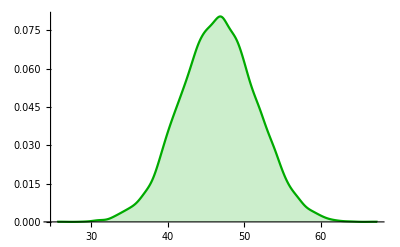

```mathematica
PermuSuperExpanH=Table[(
hoz=Tally[Sort[RandomInteger[{1,Length[supexp]},Total[supexp]]]];
guq=ConstantArray[0,Length[supexp]];
hoz1=#[[1]]-> #[[2]]&/@hoz;
SuperexpanSimul=ReplacePart[guq,hoz1];
Total[SuperexpanSimul jooH]),{10000}];

SmoothHistogram[PermuSuperExpanH,PlotStyle-> Darker[Green],Filling->Axis]
```

```mathematica
N[Count[(#≥  57)&/@PermuSuperExpanH,True]/Length[PermuSuperExpanH]]
```

0.0243

```mathematica
Mean[PermuSuperExpanH]//N
```

46.659

```mathematica
(** W: 40  *)
```

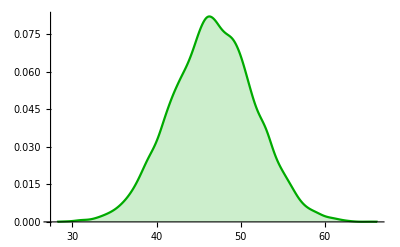

```mathematica
PermuSuperExpanW=Table[(
hoz=Tally[Sort[RandomInteger[{1,Length[supexp]},Total[supexp]]]];
guq=ConstantArray[0,Length[supexp]];
hoz1=#[[1]]-> #[[2]]&/@hoz;
SuperexpanSimul=ReplacePart[guq,hoz1];
Total[SuperexpanSimul jooW]),{10000}];

SmoothHistogram[PermuSuperExpanW,PlotStyle-> Darker[Green],Filling->Axis]
```

```mathematica
N[Count[(#≤  40)&/@PermuSuperExpanW,True]/Length[PermuSuperExpanW]]
```

0.1049

```mathematica
Mean[PermuSuperExpanW]//N
```

46.7115

```mathematica
(** L: 52  *)
```

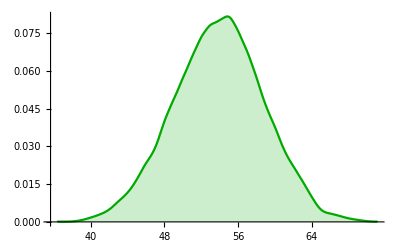

```mathematica
PermuSuperExpanL=Table[(
hoz=Tally[Sort[RandomInteger[{1,Length[supexp]},Total[supexp]]]];
guq=ConstantArray[0,Length[supexp]];
hoz1=#[[1]]-> #[[2]]&/@hoz;
SuperexpanSimul=ReplacePart[guq,hoz1];
Total[SuperexpanSimul jooL]),{10000}];

SmoothHistogram[PermuSuperExpanL,PlotStyle-> Darker[Green],Filling->Axis]
```

```mathematica
N[Count[(#≤   52)&/@PermuSuperExpanL,True]/Length[PermuSuperExpanL]]
```

0.3843

```mathematica
Mean[PermuSuperExpanL]//N
```

53.881

```mathematica
Spec3NEF={{Around[47,64-47],45},{Around[47,67-47],57},{Around[47,66-47],40},{Around[54,71-54],52}};
```

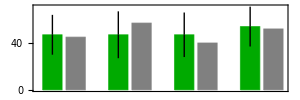

```mathematica
BarChart[Spec3NEF,ChartStyle-> {Darker[Green],Gray},PlotTheme->"Web",BarSpacing->{0.2,1.2},ImageSize->300,AspectRatio->1/3]
```